```mathematica
dataDDIdeg=First[Transpose[Import["C:\Hyperion\4.1\ddi-degrees41.csv"]]]
```

Transpose::nmtx: The first two levels of {} cannot be transposed.

{}

```mathematica
dataFirst =IntegerDigits[dataDDIdeg]
```

{{6,3,7},{1,1,9,7},{1,3,1,0},{1,4,1,6},{8,1,0},{2,8,8},{1,9,4},{4,6,1},{1,0,8},{2,4,3},{5,5,0},{3,6,8},{2,2,4},{1,1,6},{1,0,8},{1,0,8},{5,6,7},{1,0,8},{1,2,7,1},{1,0,4,5},{1,0,1,4},{1,4,3,0},{1,0,9},{4,9,6},{1,0,0,7},{6,9,2},{3,4,0},{1,1,1,0},{5,7,0},{1,6,6,9},{2,1,4,3},{2,4,6,6},{1,4,2,7},{6,1,8},{1,5,8,5},{6,3,7},{8,9,3},{1,2,2,1},{2,4,9},{1,6,2,4},4214,{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,3},{1},{1},{1},{1},{1},{1}}
 |  |  |  |

```mathematica
{{2},{1,4,3},{5,2},{2},{9,7},{2,9},{2},{5},{8},{2},{1,4},{5},{7,9},{3,5},{7,6},{1},{7,2},{3},{4,4},{1,4},{4},{4},{1,4},{1,4},{4},{2},{6},{9,1},{1,1},{8,5},{1,0},{6,1},{7},{4},{1},{6},{1,1},{1,0},{1,1},{5},{1},{7},{5},{4},{1},{2,3},{1},{1},{2,1},{3},{2},{2},{8},{1,8},{1,4},{1,2},{4,1},{5,7},{4,4},{9,9},{1,3},{4,5},{5,6},{1,2},{4,8},{1,5},{9},{1,2},{1,4},{5,0},{3,9},{1,6},{1,9},{2,1},{2,6},{5,3},{6,1},{5,1},{2,7},{6,4},{4,2},{4,6},{4,2},{2,0},{2,2},{2,8},{3,8},{3},{7},{2},{3},{7},{2},{4,0},{5},{2,0},{3,5},{2,0},{3,1},{6,1},{1,1},{1},{2},{9},{9},{9},{1,3},{4},{4},{2,8},{2},{1,8,1},{1,1},{2,7},{8},{4},{3,3},{1},{1},{1},{1},{3},{3},{1},{1,4},{1,3},{3},{3},{1},{2},{1},{1,5,0},{3},{3,0},{2},{6},{1,0},{1},{1,0},{6},{4},{3,6},{8},{8},{3,1},{4},{3},{1},{3,9},{2,8},{2},{1},{1,1},{2,0},{2},{1,8},{1,0},{3,3},{1,7},{3},{7,5},{3,6},{5,3},{3,9},{6},{3,9},{9},{1},{4,3},{4,3},{1,1},{6},{2},{2},{5,2},{1,4,7},{2,0},{1},{1},{1,2},{1,9},{1},{2},{2,0},{7},{2},{6},{2},{3,6},{1,8},{2},{3},{1,5},{1,6},{1},{7},{3},{1},{3},{1,8},{5,2},{1,5},{2,8},{1},{4},{1,1},{1,0},{1,8},{4,9},{1,0},{2,9},{7,9},{9,2},{1,0},{3,2},{1,0},{2,6},{4,2},{1},{5},{1},{1},{2,2},{1},{9},{1,3,2},{7,8},{4},{1,1,0},{1,3},{8,1},{8,6},{4,4},{4,9},{4,9},{1,4,7},{2,9},{4,0},{4,6},{4,0},{1},{4,8},{1,1},{7,7},{3,7},{3,4},{8},{8},{1,7},{2,0},{1,5},{1,2},{3,3},{1,1,4},{3},{1,5},{6,5},{3,8},{4,1},{2,6},{1,0,6},{1,6},{2,5,0},{2,2},{3,2},{2,5},{1,7},{2,0},{7,0},{3,6},{6},{3,5},{3,8},{1,1,7},{3},{4},{6,1},{6,5},{7,9},{2,2},{1,0},{1,5},{6,6},{1,4},{1},{1,8},{2,0},{6,0},{7},{9},{3,1},{6,0},{3},{2,9},{9,8},{1,2},{3},{1,9,8},{8,4},{1,5},{7},{1,6,1},{1,5,7},{4,5},{3,7},{9,8},{4,2},{9},{1,6},{6},{3,9},{3,4},{6,9},{3},{7,3},{1,3},{1,2,8},{8,0},{4,3},{1,5},{1,1,4},{6,8},{9},{4,4},{6,2},{1,2,6},{3,8},{5,7},{4,7},{5,8},{3,5},{2,9},{2,9},{2,9},{2,9},{4,9},{2,0},{6,4},{1,7},{1,8},{8},{4},{3},{1,2},{2},{2},{1,1},{2,5},{2,6},{2,8},{9},{1},{2},{3,4},{2},{1},{9,2},{7,5},{1,7,4},{9,3},{1,0,0},{7,4},{9,9},{7,8},{4},{8},{2},{2,6},{6},{6},{4},{4},{1},{1,1},{9,6},{5,9},{1,1,2},{6,1},{2},{1},{4},{1,1},{5,6},{4},{8,6},{2},{2,0},{5},{1,7},{1,0},{9},{2},{2,1},{2,1},{2},{2,7},{3},{5},{4},{3,0},{2,0},{8,6},{1,8},{3,0},{2,9},{1,2,2},{7},{1},{6,3},{7,6},{5,5},{1,0},{7,0},{4,8},{5,8},{2,3},{1,9},{1,2,9},{1,1},{4,6},{1,9,8},{7,7},{2,4},{9},{7,2},{6,4},{3,0},{2,7},{3,9},{3,3},{2,0},{8,8},{6,3},{4,6},{2,1},{8,5},{2,4},{2,7},{7,2},{2,7},{2,4},{2,0},{1,2},{2,1},{2,3},{1,1,8},{7,2},{7,5},{1,6},{6,1},{3,0},{7,0},{8,0},{7,3},{1,3,2},{2,1},{2,2},{2,1},{3,2},{5,8},{2,0},{2,7},{2,8},{1,0},{2,8},{2,3},{2,7},{9},{2},{1},{2,9},{5,0},{2,8},{6,4},{3,0},{3,1},{3,7},{5,7},{4,5},{1,8},{2},{6,7},{4},{1,8},{1,3},{1,8},{3,9},{2,8},{2,2},{2,5},{3,0},{3,9},{3,9},{1,7},{1,9},{2,6},{2,8},{2,2},{3,9},{1,7},{2,7},{2,5},{1,6},{4},{4},{1,3},{1,2},{1,5},{1,5},{1,3},{1,2},{1,5},{1,7},{5},{4,8},{2,2},{4,7},{8},{1,4},{2,3},{1,0},{2,3},{3,0},{1,7},{9,3},{5,8},{2,3},{9},{4,6},{6,7},{5,6},{1,4},{1,1,4},{3,1},{1,1},{2,8},{4,2},{1,2},{1,0},{1,3},{4,2},{2,9},{3,9},{1,5},{3,6},{2,2},{4},{1,8},{3,2},{3,4},{1,3},{3,4},{1},{3,1},{2,5},{2,9},{1,9},{1,8},{1,8},{3},{8,5},{2,1},{7,8},{4,0},{2,1},{2,3},{8},{1,1},{2,2},{2,9},{3,5},{1,7},{4,9},{1,4},{3,7},{1,0},{1,1},{5},{1,7},{2,1},{3},{1,7},{3,7},{2,1},{2,9},{3,4},{4,9},{2,0},{3,8},{3,4},{4,8},{1,1},{2,6},{3,4},{2,7},{1,4},{2,5},{1,1},{2,4},{6},{1,3},{6},{4},{2,1},{1,3},{2,0},{3,4},{3,4},{3,2},{1},{1,4},{1,4},{9},{1,0},{8},{8},{1,9},{1,0},{2,5},{2,0},{1,6},{1,8},{1,7},{2,6},{2,0},{1,7},{2,1},{1,7},{5,0},{1,0},{1,1},{1},{1,6},{4,5},{1,0},{3},{8},{7},{4},{7},{7},{6},{1,9},{8},{8},{2,3},{5},{7},{2},{3},{1,0},{8},{9,9},{5},{2,4},{7},{8},{8},{8},{7},{8},{8},{7},{9,7},{1,8},{4},{5},{5},{3},{7},{3},{7},{8},{6,1},{8},{1,3},{7},{9},{7},{4},{1,3},{7},{6},{5},{3,4},{8},{1,2},{1,6},{9},{1,7},{2,0},{1,8},{1,1},{9},{3,1},{1,6},{3,0},{3,5},{2,5},{3,7},{1,4},{3,8},{2,5},{2,6},{1,5},{2,3},{6},{8},{1,1},{2,0},{1,9},{1,8},{1},{1,3},{9},{1,1},{9},{1,1},{2,1},{3},{4},{1,1},{2},{1,0},{1},{6},{4},{9},{7,2},{2,4},{2,4},{1,9},{2,7},{1,8},{2,8},{2,4},{2,3},{1,5},{1,5},{1,4},{2,0},{1,4},{4},{4},{3,2},{9},{3},{1,5},{2,2},{7},{1,0},{1,1},{9},{8},{3,8},{1,2},{8},{2,2},{2,0},{1,3},{1,0},{2,0},{4},{3},{1,1},{8},{1,2},{9},{7},{4},{4},{8},{2,2},{1,8},{1,9},{1,9},{1,2},{5},{3},{6},{9},{1,5},{1,5},{1,5},{1,7},{1,8},{2,9},{9},{2},{8},{8},{7},{4},{7},{5},{6},{1,2},{5},{2,7},{1,0},{5},{1,1},{1,0},{1,4},{9},{5},{5},{1,0},{8},{6},{5},{1,1},{1,0},{5},{1,0},{1,7},{8},{6},{3},{1,0},{7},{5},{1,4},{1,3},{8},{6},{1,4},{4,6},{2,0},{1,6},{9},{1,1},{5},{5},{4},{4,9},{9},{4},{9},{2,1},{1,3},{5},{4},{2},{3},{9},{8},{2,3},{5},{5},{6},{1,7},{5},{7},{1,5},{4},{1,8},{1,4},{4},{1,0},{1,2},{1,2},{8},{7},{1,2},{6},{5},{1},{3,7},{4},{6},{5},{8},{4},{4},{2},{2},{1,4},{2,6},{1},{5},{2},{6},{5},{1},{1},{5},{4},{3},{8},{1,2},{2,1},{1,9},{1,6},{7},{2},{6},{6},{3},{8},{1,3},{8},{1},{4},{1},{7},{7},{8},{7},{1,0},{1},{1},{3},{1,7},{1,8},{3},{5},{2},{1,0},{1,2},{2},{1},{3},{2},{3},{1},{1},{1},{3,4},{1,1},{1,1},{1,1},{4},{3},{3},{9},{4},{9},{1,0},{1},{4},{1,1},{9},{3},{8},{1,3},{4},{2},{6},{2},{1,0},{6},{2},{4},{1,3},{1},{1},{2},{4},{8},{1,8},{1},{1},{2},{1},{1},{3},{1},{1},{2},{1},{8},{1},{1},{5},{8},{1,2},{1},{1},{4},{8},{4},{5},{4},{7},{7},{1,0},{2},{2},{2},{3},{2},{5},{5},{1},{3},{1},{3},{3},{2},{6},{1},{6},{3},{3},{1},{6},{2},{1,5},{3},{4},{3},{2},{2},{1},{6},{1},{1,3},{1,0},{7},{8},{1,1},{1,0},{2},{1,1},{1,6},{1,7},{1,3},{1,5},{1},{6},{1},{5},{5},{6},{1},{8},{4},{1,3},{5},{4},{5},{5},{5},{4},{5},{5},{1},{1},{3},{4},{4},{3},{4},{2},{1},{1},{3},{9},{5},{2},{3},{1},{1},{1},{1},{7},{4},{2},{2},{2},{2},{3},{1},{1},{1},{1},{4},{5},{2},{3},{4},{1},{1},{5},{6},{1},{1},{1},{1},{1},{3},{2},{3},{2},{4},{2},{2},{2},{3},{2},{2},{1},{1},{3},{1},{3},{4},{4},{1},{6},{4},{1},{3},{1},{1},{1},{1},{2},{1},{1},{3},{1},{2},{1},{1},{1},{3},{7},{1},{2},{5},{1},{2},{1},{1},{2},{1},{6},{2},{2},{1},{1},{1},{1},{1},{1},{1},{1},{1},{2},{3},{1},{1},{1},{3},{1},{1},{1},{1},{1},{1},{3},{2},{1},{1},{1}}

dataFirst = {{2},{1,4,3},{5,2},{2},{9,7},{2,9},{2},{5},{8},{2},{1,4},{5},{7,9},{3,5},{7,6},{1},{7,2},{3},{4,4},{1,4},{4},{4},{1,4},{1,4},{4},{2},{6},{9,1},{1,1},{8,5},{1,0},{6,1},{7},{4},{1},{6},{1,1},{1,0},{1,1},{5},{1},{7},{5},{4},{1},{2,3},{1},{1},{2,1},{3},{2},{2},{8},{1,8},{1,4},{1,2},{4,1},{5,7},{4,4},{9,9},{1,3},{4,5},{5,6},{1,2},{4,8},{1,5},{9},{1,2},{1,4},{5,0},{3,9},{1,6},{1,9},{2,1},{2,6},{5,3},{6,1},{5,1},{2,7},{6,4},{4,2},{4,6},{4,2},{2,0},{2,2},{2,8},{3,8},{3},{7},{2},{3},{7},{2},{4,0},{5},{2,0},{3,5},{2,0},{3,1},{6,1},{1,1},{1},{2},{9},{9},{9},{1,3},{4},{4},{2,8},{2},{1,8,1},{1,1},{2,7},{8},{4},{3,3},{1},{1},{1},{1},{3},{3},{1},{1,4},{1,3},{3},{3},{1},{2},{1},{1,5,0},{3},{3,0},{2},{6},{1,0},{1},{1,0},{6},{4},{3,6},{8},{8},{3,1},{4},{3},{1},{3,9},{2,8},{2},{1},{1,1},{2,0},{2},{1,8},{1,0},{3,3},{1,7},{3},{7,5},{3,6},{5,3},{3,9},{6},{3,9},{9},{1},{4,3},{4,3},{1,1},{6},{2},{2},{5,2},{1,4,7},{2,0},{1},{1},{1,2},{1,9},{1},{2},{2,0},{7},{2},{6},{2},{3,6},{1,8},{2},{3},{1,5},{1,6},{1},{7},{3},{1},{3},{1,8},{5,2},{1,5},{2,8},{1},{4},{1,1},{1,0},{1,8},{4,9},{1,0},{2,9},{7,9},{9,2},{1,0},{3,2},{1,0},{2,6},{4,2},{1},{5},{1},{1},{2,2},{1},{9},{1,3,2},{7,8},{4},{1,1,0},{1,3},{8,1},{8,6},{4,4},{4,9},{4,9},{1,4,7},{2,9},{4,0},{4,6},{4,0},{1},{4,8},{1,1},{7,7},{3,7},{3,4},{8},{8},{1,7},{2,0},{1,5},{1,2},{3,3},{1,1,4},{3},{1,5},{6,5},{3,8},{4,1},{2,6},{1,0,6},{1,6},{2,5,0},{2,2},{3,2},{2,5},{1,7},{2,0},{7,0},{3,6},{6},{3,5},{3,8},{1,1,7},{3},{4},{6,1},{6,5},{7,9},{2,2},{1,0},{1,5},{6,6},{1,4},{1},{1,8},{2,0},{6,0},{7},{9},{3,1},{6,0},{3},{2,9},{9,8},{1,2},{3},{1,9,8},{8,4},{1,5},{7},{1,6,1},{1,5,7},{4,5},{3,7},{9,8},{4,2},{9},{1,6},{6},{3,9},{3,4},{6,9},{3},{7,3},{1,3},{1,2,8},{8,0},{4,3},{1,5},{1,1,4},{6,8},{9},{4,4},{6,2},{1,2,6},{3,8},{5,7},{4,7},{5,8},{3,5},{2,9},{2,9},{2,9},{2,9},{4,9},{2,0},{6,4},{1,7},{1,8},{8},{4},{3},{1,2},{2},{2},{1,1},{2,5},{2,6},{2,8},{9},{1},{2},{3,4},{2},{1},{9,2},{7,5},{1,7,4},{9,3},{1,0,0},{7,4},{9,9},{7,8},{4},{8},{2},{2,6},{6},{6},{4},{4},{1},{1,1},{9,6},{5,9},{1,1,2},{6,1},{2},{1},{4},{1,1},{5,6},{4},{8,6},{2},{2,0},{5},{1,7},{1,0},{9},{2},{2,1},{2,1},{2},{2,7},{3},{5},{4},{3,0},{2,0},{8,6},{1,8},{3,0},{2,9},{1,2,2},{7},{1},{6,3},{7,6},{5,5},{1,0},{7,0},{4,8},{5,8},{2,3},{1,9},{1,2,9},{1,1},{4,6},{1,9,8},{7,7},{2,4},{9},{7,2},{6,4},{3,0},{2,7},{3,9},{3,3},{2,0},{8,8},{6,3},{4,6},{2,1},{8,5},{2,4},{2,7},{7,2},{2,7},{2,4},{2,0},{1,2},{2,1},{2,3},{1,1,8},{7,2},{7,5},{1,6},{6,1},{3,0},{7,0},{8,0},{7,3},{1,3,2},{2,1},{2,2},{2,1},{3,2},{5,8},{2,0},{2,7},{2,8},{1,0},{2,8},{2,3},{2,7},{9},{2},{1},{2,9},{5,0},{2,8},{6,4},{3,0},{3,1},{3,7},{5,7},{4,5},{1,8},{2},{6,7},{4},{1,8},{1,3},{1,8},{3,9},{2,8},{2,2},{2,5},{3,0},{3,9},{3,9},{1,7},{1,9},{2,6},{2,8},{2,2},{3,9},{1,7},{2,7},{2,5},{1,6},{4},{4},{1,3},{1,2},{1,5},{1,5},{1,3},{1,2},{1,5},{1,7},{5},{4,8},{2,2},{4,7},{8},{1,4},{2,3},{1,0},{2,3},{3,0},{1,7},{9,3},{5,8},{2,3},{9},{4,6},{6,7},{5,6},{1,4},{1,1,4},{3,1},{1,1},{2,8},{4,2},{1,2},{1,0},{1,3},{4,2},{2,9},{3,9},{1,5},{3,6},{2,2},{4},{1,8},{3,2},{3,4},{1,3},{3,4},{1},{3,1},{2,5},{2,9},{1,9},{1,8},{1,8},{3},{8,5},{2,1},{7,8},{4,0},{2,1},{2,3},{8},{1,1},{2,2},{2,9},{3,5},{1,7},{4,9},{1,4},{3,7},{1,0},{1,1},{5},{1,7},{2,1},{3},{1,7},{3,7},{2,1},{2,9},{3,4},{4,9},{2,0},{3,8},{3,4},{4,8},{1,1},{2,6},{3,4},{2,7},{1,4},{2,5},{1,1},{2,4},{6},{1,3},{6},{4},{2,1},{1,3},{2,0},{3,4},{3,4},{3,2},{1},{1,4},{1,4},{9},{1,0},{8},{8},{1,9},{1,0},{2,5},{2,0},{1,6},{1,8},{1,7},{2,6},{2,0},{1,7},{2,1},{1,7},{5,0},{1,0},{1,1},{1},{1,6},{4,5},{1,0},{3},{8},{7},{4},{7},{7},{6},{1,9},{8},{8},{2,3},{5},{7},{2},{3},{1,0},{8},{9,9},{5},{2,4},{7},{8},{8},{8},{7},{8},{8},{7},{9,7},{1,8},{4},{5},{5},{3},{7},{3},{7},{8},{6,1},{8},{1,3},{7},{9},{7},{4},{1,3},{7},{6},{5},{3,4},{8},{1,2},{1,6},{9},{1,7},{2,0},{1,8},{1,1},{9},{3,1},{1,6},{3,0},{3,5},{2,5},{3,7},{1,4},{3,8},{2,5},{2,6},{1,5},{2,3},{6},{8},{1,1},{2,0},{1,9},{1,8},{1},{1,3},{9},{1,1},{9},{1,1},{2,1},{3},{4},{1,1},{2},{1,0},{1},{6},{4},{9},{7,2},{2,4},{2,4},{1,9},{2,7},{1,8},{2,8},{2,4},{2,3},{1,5},{1,5},{1,4},{2,0},{1,4},{4},{4},{3,2},{9},{3},{1,5},{2,2},{7},{1,0},{1,1},{9},{8},{3,8},{1,2},{8},{2,2},{2,0},{1,3},{1,0},{2,0},{4},{3},{1,1},{8},{1,2},{9},{7},{4},{4},{8},{2,2},{1,8},{1,9},{1,9},{1,2},{5},{3},{6},{9},{1,5},{1,5},{1,5},{1,7},{1,8},{2,9},{9},{2},{8},{8},{7},{4},{7},{5},{6},{1,2},{5},{2,7},{1,0},{5},{1,1},{1,0},{1,4},{9},{5},{5},{1,0},{8},{6},{5},{1,1},{1,0},{5},{1,0},{1,7},{8},{6},{3},{1,0},{7},{5},{1,4},{1,3},{8},{6},{1,4},{4,6},{2,0},{1,6},{9},{1,1},{5},{5},{4},{4,9},{9},{4},{9},{2,1},{1,3},{5},{4},{2},{3},{9},{8},{2,3},{5},{5},{6},{1,7},{5},{7},{1,5},{4},{1,8},{1,4},{4},{1,0},{1,2},{1,2},{8},{7},{1,2},{6},{5},{1},{3,7},{4},{6},{5},{8},{4},{4},{2},{2},{1,4},{2,6},{1},{5},{2},{6},{5},{1},{1},{5},{4},{3},{8},{1,2},{2,1},{1,9},{1,6},{7},{2},{6},{6},{3},{8},{1,3},{8},{1},{4},{1},{7},{7},{8},{7},{1,0},{1},{1},{3},{1,7},{1,8},{3},{5},{2},{1,0},{1,2},{2},{1},{3},{2},{3},{1},{1},{1},{3,4},{1,1},{1,1},{1,1},{4},{3},{3},{9},{4},{9},{1,0},{1},{4},{1,1},{9},{3},{8},{1,3},{4},{2},{6},{2},{1,0},{6},{2},{4},{1,3},{1},{1},{2},{4},{8},{1,8},{1},{1},{2},{1},{1},{3},{1},{1},{2},{1},{8},{1},{1},{5},{8},{1,2},{1},{1},{4},{8},{4},{5},{4},{7},{7},{1,0},{2},{2},{2},{3},{2},{5},{5},{1},{3},{1},{3},{3},{2},{6},{1},{6},{3},{3},{1},{6},{2},{1,5},{3},{4},{3},{2},{2},{1},{6},{1},{1,3},{1,0},{7},{8},{1,1},{1,0},{2},{1,1},{1,6},{1,7},{1,3},{1,5},{1},{6},{1},{5},{5},{6},{1},{8},{4},{1,3},{5},{4},{5},{5},{5},{4},{5},{5},{1},{1},{3},{4},{4},{3},{4},{2},{1},{1},{3},{9},{5},{2},{3},{1},{1},{1},{1},{7},{4},{2},{2},{2},{2},{3},{1},{1},{1},{1},{4},{5},{2},{3},{4},{1},{1},{5},{6},{1},{1},{1},{1},{1},{3},{2},{3},{2},{4},{2},{2},{2},{3},{2},{2},{1},{1},{3},{1},{3},{4},{4},{1},{6},{4},{1},{3},{1},{1},{1},{1},{2},{1},{1},{3},{1},{2},{1},{1},{1},{3},{7},{1},{2},{5},{1},{2},{1},{1},{2},{1},{6},{2},{2},{1},{1},{1},{1},{1},{1},{1},{1},{1},{2},{3},{1},{1},{1},{3},{1},{1},{1},{1},{1},{1},{3},{2},{1},{1},{1}}
```

{{2},{1,4,3},{5,2},{2},{9,7},{2,9},{2},{5},{8},{2},{1,4},{5},{7,9},{3,5},{7,6},{1},{7,2},{3},{4,4},{1,4},{4},{4},{1,4},{1,4},{4},{2},{6},{9,1},{1,1},{8,5},{1,0},{6,1},{7},{4},{1},{6},{1,1},{1,0},{1,1},{5},{1},{7},{5},{4},{1},{2,3},{1},{1},{2,1},{3},{2},{2},{8},{1,8},{1,4},{1,2},{4,1},{5,7},{4,4},{9,9},{1,3},{4,5},{5,6},{1,2},{4,8},{1,5},{9},{1,2},{1,4},{5,0},{3,9},{1,6},{1,9},{2,1},{2,6},{5,3},{6,1},{5,1},{2,7},{6,4},{4,2},{4,6},{4,2},{2,0},{2,2},{2,8},{3,8},{3},{7},{2},{3},{7},{2},{4,0},{5},{2,0},{3,5},{2,0},{3,1},{6,1},{1,1},{1},{2},{9},{9},{9},{1,3},{4},{4},{2,8},{2},{1,8,1},{1,1},{2,7},{8},{4},{3,3},{1},{1},{1},{1},{3},{3},{1},{1,4},{1,3},{3},{3},{1},{2},{1},{1,5,0},{3},{3,0},{2},{6},{1,0},{1},{1,0},{6},{4},{3,6},{8},{8},{3,1},{4},{3},{1},{3,9},{2,8},{2},{1},{1,1},{2,0},{2},{1,8},{1,0},{3,3},{1,7},{3},{7,5},{3,6},{5,3},{3,9},{6},{3,9},{9},{1},{4,3},{4,3},{1,1},{6},{2},{2},{5,2},{1,4,7},{2,0},{1},{1},{1,2},{1,9},{1},{2},{2,0},{7},{2},{6},{2},{3,6},{1,8},{2},{3},{1,5},{1,6},{1},{7},{3},{1},{3},{1,8},{5,2},{1,5},{2,8},{1},{4},{1,1},{1,0},{1,8},{4,9},{1,0},{2,9},{7,9},{9,2},{1,0},{3,2},{1,0},{2,6},{4,2},{1},{5},{1},{1},{2,2},{1},{9},{1,3,2},{7,8},{4},{1,1,0},{1,3},{8,1},{8,6},{4,4},{4,9},{4,9},{1,4,7},{2,9},{4,0},{4,6},{4,0},{1},{4,8},{1,1},{7,7},{3,7},{3,4},{8},{8},{1,7},{2,0},{1,5},{1,2},{3,3},{1,1,4},{3},{1,5},{6,5},{3,8},{4,1},{2,6},{1,0,6},{1,6},{2,5,0},{2,2},{3,2},{2,5},{1,7},{2,0},{7,0},{3,6},{6},{3,5},{3,8},{1,1,7},{3},{4},{6,1},{6,5},{7,9},{2,2},{1,0},{1,5},{6,6},{1,4},{1},{1,8},{2,0},{6,0},{7},{9},{3,1},{6,0},{3},{2,9},{9,8},{1,2},{3},{1,9,8},{8,4},{1,5},{7},{1,6,1},{1,5,7},{4,5},{3,7},{9,8},{4,2},{9},{1,6},{6},{3,9},{3,4},{6,9},{3},{7,3},{1,3},{1,2,8},{8,0},{4,3},{1,5},{1,1,4},{6,8},{9},{4,4},{6,2},{1,2,6},{3,8},{5,7},{4,7},{5,8},{3,5},{2,9},{2,9},{2,9},{2,9},{4,9},{2,0},{6,4},{1,7},{1,8},{8},{4},{3},{1,2},{2},{2},{1,1},{2,5},{2,6},{2,8},{9},{1},{2},{3,4},{2},{1},{9,2},{7,5},{1,7,4},{9,3},{1,0,0},{7,4},{9,9},{7,8},{4},{8},{2},{2,6},{6},{6},{4},{4},{1},{1,1},{9,6},{5,9},{1,1,2},{6,1},{2},{1},{4},{1,1},{5,6},{4},{8,6},{2},{2,0},{5},{1,7},{1,0},{9},{2},{2,1},{2,1},{2},{2,7},{3},{5},{4},{3,0},{2,0},{8,6},{1,8},{3,0},{2,9},{1,2,2},{7},{1},{6,3},{7,6},{5,5},{1,0},{7,0},{4,8},{5,8},{2,3},{1,9},{1,2,9},{1,1},{4,6},{1,9,8},{7,7},{2,4},{9},{7,2},{6,4},{3,0},{2,7},{3,9},{3,3},{2,0},{8,8},{6,3},{4,6},{2,1},{8,5},{2,4},{2,7},{7,2},{2,7},{2,4},{2,0},{1,2},{2,1},{2,3},{1,1,8},{7,2},{7,5},{1,6},{6,1},{3,0},{7,0},{8,0},{7,3},{1,3,2},{2,1},{2,2},{2,1},{3,2},{5,8},{2,0},{2,7},{2,8},{1,0},{2,8},{2,3},{2,7},{9},{2},{1},{2,9},{5,0},{2,8},{6,4},{3,0},{3,1},{3,7},{5,7},{4,5},{1,8},{2},{6,7},{4},{1,8},{1,3},{1,8},{3,9},{2,8},{2,2},{2,5},{3,0},{3,9},{3,9},{1,7},{1,9},{2,6},{2,8},{2,2},{3,9},{1,7},{2,7},{2,5},{1,6},{4},{4},{1,3},{1,2},{1,5},{1,5},{1,3},{1,2},{1,5},{1,7},{5},{4,8},{2,2},{4,7},{8},{1,4},{2,3},{1,0},{2,3},{3,0},{1,7},{9,3},{5,8},{2,3},{9},{4,6},{6,7},{5,6},{1,4},{1,1,4},{3,1},{1,1},{2,8},{4,2},{1,2},{1,0},{1,3},{4,2},{2,9},{3,9},{1,5},{3,6},{2,2},{4},{1,8},{3,2},{3,4},{1,3},{3,4},{1},{3,1},{2,5},{2,9},{1,9},{1,8},{1,8},{3},{8,5},{2,1},{7,8},{4,0},{2,1},{2,3},{8},{1,1},{2,2},{2,9},{3,5},{1,7},{4,9},{1,4},{3,7},{1,0},{1,1},{5},{1,7},{2,1},{3},{1,7},{3,7},{2,1},{2,9},{3,4},{4,9},{2,0},{3,8},{3,4},{4,8},{1,1},{2,6},{3,4},{2,7},{1,4},{2,5},{1,1},{2,4},{6},{1,3},{6},{4},{2,1},{1,3},{2,0},{3,4},{3,4},{3,2},{1},{1,4},{1,4},{9},{1,0},{8},{8},{1,9},{1,0},{2,5},{2,0},{1,6},{1,8},{1,7},{2,6},{2,0},{1,7},{2,1},{1,7},{5,0},{1,0},{1,1},{1},{1,6},{4,5},{1,0},{3},{8},{7},{4},{7},{7},{6},{1,9},{8},{8},{2,3},{5},{7},{2},{3},{1,0},{8},{9,9},{5},{2,4},{7},{8},{8},{8},{7},{8},{8},{7},{9,7},{1,8},{4},{5},{5},{3},{7},{3},{7},{8},{6,1},{8},{1,3},{7},{9},{7},{4},{1,3},{7},{6},{5},{3,4},{8},{1,2},{1,6},{9},{1,7},{2,0},{1,8},{1,1},{9},{3,1},{1,6},{3,0},{3,5},{2,5},{3,7},{1,4},{3,8},{2,5},{2,6},{1,5},{2,3},{6},{8},{1,1},{2,0},{1,9},{1,8},{1},{1,3},{9},{1,1},{9},{1,1},{2,1},{3},{4},{1,1},{2},{1,0},{1},{6},{4},{9},{7,2},{2,4},{2,4},{1,9},{2,7},{1,8},{2,8},{2,4},{2,3},{1,5},{1,5},{1,4},{2,0},{1,4},{4},{4},{3,2},{9},{3},{1,5},{2,2},{7},{1,0},{1,1},{9},{8},{3,8},{1,2},{8},{2,2},{2,0},{1,3},{1,0},{2,0},{4},{3},{1,1},{8},{1,2},{9},{7},{4},{4},{8},{2,2},{1,8},{1,9},{1,9},{1,2},{5},{3},{6},{9},{1,5},{1,5},{1,5},{1,7},{1,8},{2,9},{9},{2},{8},{8},{7},{4},{7},{5},{6},{1,2},{5},{2,7},{1,0},{5},{1,1},{1,0},{1,4},{9},{5},{5},{1,0},{8},{6},{5},{1,1},{1,0},{5},{1,0},{1,7},{8},{6},{3},{1,0},{7},{5},{1,4},{1,3},{8},{6},{1,4},{4,6},{2,0},{1,6},{9},{1,1},{5},{5},{4},{4,9},{9},{4},{9},{2,1},{1,3},{5},{4},{2},{3},{9},{8},{2,3},{5},{5},{6},{1,7},{5},{7},{1,5},{4},{1,8},{1,4},{4},{1,0},{1,2},{1,2},{8},{7},{1,2},{6},{5},{1},{3,7},{4},{6},{5},{8},{4},{4},{2},{2},{1,4},{2,6},{1},{5},{2},{6},{5},{1},{1},{5},{4},{3},{8},{1,2},{2,1},{1,9},{1,6},{7},{2},{6},{6},{3},{8},{1,3},{8},{1},{4},{1},{7},{7},{8},{7},{1,0},{1},{1},{3},{1,7},{1,8},{3},{5},{2},{1,0},{1,2},{2},{1},{3},{2},{3},{1},{1},{1},{3,4},{1,1},{1,1},{1,1},{4},{3},{3},{9},{4},{9},{1,0},{1},{4},{1,1},{9},{3},{8},{1,3},{4},{2},{6},{2},{1,0},{6},{2},{4},{1,3},{1},{1},{2},{4},{8},{1,8},{1},{1},{2},{1},{1},{3},{1},{1},{2},{1},{8},{1},{1},{5},{8},{1,2},{1},{1},{4},{8},{4},{5},{4},{7},{7},{1,0},{2},{2},{2},{3},{2},{5},{5},{1},{3},{1},{3},{3},{2},{6},{1},{6},{3},{3},{1},{6},{2},{1,5},{3},{4},{3},{2},{2},{1},{6},{1},{1,3},{1,0},{7},{8},{1,1},{1,0},{2},{1,1},{1,6},{1,7},{1,3},{1,5},{1},{6},{1},{5},{5},{6},{1},{8},{4},{1,3},{5},{4},{5},{5},{5},{4},{5},{5},{1},{1},{3},{4},{4},{3},{4},{2},{1},{1},{3},{9},{5},{2},{3},{1},{1},{1},{1},{7},{4},{2},{2},{2},{2},{3},{1},{1},{1},{1},{4},{5},{2},{3},{4},{1},{1},{5},{6},{1},{1},{1},{1},{1},{3},{2},{3},{2},{4},{2},{2},{2},{3},{2},{2},{1},{1},{3},{1},{3},{4},{4},{1},{6},{4},{1},{3},{1},{1},{1},{1},{2},{1},{1},{3},{1},{2},{1},{1},{1},{3},{7},{1},{2},{5},{1},{2},{1},{1},{2},{1},{6},{2},{2},{1},{1},{1},{1},{1},{1},{1},{1},{1},{2},{3},{1},{1},{1},{3},{1},{1},{1},{1},{1},{1},{3},{2},{1},{1},{1}}

{{2},{1,4,3},{5,2},{2},{9,7},{2,9},{2},{5},{8},{2},{1,4},{5},{7,9},{3,5},{7,6},{1},{7,2},{3},{4,4},{1,4},{4},{4},{1,4},{1,4},{4},{2},{6},{9,1},{1,1},{8,5},{1,0},{6,1},{7},{4},{1},{6},{1,1},{1,0},{1,1},{5},{1},{7},{5},{4},{1},{2,3},{1},{1},{2,1},{3},{2},{2},{8},{1,8},{1,4},{1,2},{4,1},{5,7},{4,4},{9,9},{1,3},{4,5},{5,6},{1,2},{4,8},{1,5},{9},{1,2},{1,4},{5,0},{3,9},{1,6},{1,9},{2,1},{2,6},{5,3},{6,1},{5,1},{2,7},{6,4},{4,2},{4,6},{4,2},{2,0},{2,2},{2,8},{3,8},{3},{7},{2},{3},{7},{2},{4,0},{5},{2,0},{3,5},{2,0},{3,1},{6,1},{1,1},{1},{2},{9},{9},{9},{1,3},{4},{4},{2,8},{2},{1,8,1},{1,1},{2,7},{8},{4},{3,3},{1},{1},{1},{1},{3},{3},{1},{1,4},{1,3},{3},{3},{1},{2},{1},{1,5,0},{3},{3,0},{2},{6},{1,0},{1},{1,0},{6},{4},{3,6},{8},{8},{3,1},{4},{3},{1},{3,9},{2,8},{2},{1},{1,1},{2,0},{2},{1,8},{1,0},{3,3},{1,7},{3},{7,5},{3,6},{5,3},{3,9},{6},{3,9},{9},{1},{4,3},{4,3},{1,1},{6},{2},{2},{5,2},{1,4,7},{2,0},{1},{1},{1,2},{1,9},{1},{2},{2,0},{7},{2},{6},{2},{3,6},{1,8},{2},{3},{1,5},{1,6},{1},{7},{3},{1},{3},{1,8},{5,2},{1,5},{2,8},{1},{4},{1,1},{1,0},{1,8},{4,9},{1,0},{2,9},{7,9},{9,2},{1,0},{3,2},{1,0},{2,6},{4,2},{1},{5},{1},{1},{2,2},{1},{9},{1,3,2},{7,8},{4},{1,1,0},{1,3},{8,1},{8,6},{4,4},{4,9},{4,9},{1,4,7},{2,9},{4,0},{4,6},{4,0},{1},{4,8},{1,1},{7,7},{3,7},{3,4},{8},{8},{1,7},{2,0},{1,5},{1,2},{3,3},{1,1,4},{3},{1,5},{6,5},{3,8},{4,1},{2,6},{1,0,6},{1,6},{2,5,0},{2,2},{3,2},{2,5},{1,7},{2,0},{7,0},{3,6},{6},{3,5},{3,8},{1,1,7},{3},{4},{6,1},{6,5},{7,9},{2,2},{1,0},{1,5},{6,6},{1,4},{1},{1,8},{2,0},{6,0},{7},{9},{3,1},{6,0},{3},{2,9},{9,8},{1,2},{3},{1,9,8},{8,4},{1,5},{7},{1,6,1},{1,5,7},{4,5},{3,7},{9,8},{4,2},{9},{1,6},{6},{3,9},{3,4},{6,9},{3},{7,3},{1,3},{1,2,8},{8,0},{4,3},{1,5},{1,1,4},{6,8},{9},{4,4},{6,2},{1,2,6},{3,8},{5,7},{4,7},{5,8},{3,5},{2,9},{2,9},{2,9},{2,9},{4,9},{2,0},{6,4},{1,7},{1,8},{8},{4},{3},{1,2},{2},{2},{1,1},{2,5},{2,6},{2,8},{9},{1},{2},{3,4},{2},{1},{9,2},{7,5},{1,7,4},{9,3},{1,0,0},{7,4},{9,9},{7,8},{4},{8},{2},{2,6},{6},{6},{4},{4},{1},{1,1},{9,6},{5,9},{1,1,2},{6,1},{2},{1},{4},{1,1},{5,6},{4},{8,6},{2},{2,0},{5},{1,7},{1,0},{9},{2},{2,1},{2,1},{2},{2,7},{3},{5},{4},{3,0},{2,0},{8,6},{1,8},{3,0},{2,9},{1,2,2},{7},{1},{6,3},{7,6},{5,5},{1,0},{7,0},{4,8},{5,8},{2,3},{1,9},{1,2,9},{1,1},{4,6},{1,9,8},{7,7},{2,4},{9},{7,2},{6,4},{3,0},{2,7},{3,9},{3,3},{2,0},{8,8},{6,3},{4,6},{2,1},{8,5},{2,4},{2,7},{7,2},{2,7},{2,4},{2,0},{1,2},{2,1},{2,3},{1,1,8},{7,2},{7,5},{1,6},{6,1},{3,0},{7,0},{8,0},{7,3},{1,3,2},{2,1},{2,2},{2,1},{3,2},{5,8},{2,0},{2,7},{2,8},{1,0},{2,8},{2,3},{2,7},{9},{2},{1},{2,9},{5,0},{2,8},{6,4},{3,0},{3,1},{3,7},{5,7},{4,5},{1,8},{2},{6,7},{4},{1,8},{1,3},{1,8},{3,9},{2,8},{2,2},{2,5},{3,0},{3,9},{3,9},{1,7},{1,9},{2,6},{2,8},{2,2},{3,9},{1,7},{2,7},{2,5},{1,6},{4},{4},{1,3},{1,2},{1,5},{1,5},{1,3},{1,2},{1,5},{1,7},{5},{4,8},{2,2},{4,7},{8},{1,4},{2,3},{1,0},{2,3},{3,0},{1,7},{9,3},{5,8},{2,3},{9},{4,6},{6,7},{5,6},{1,4},{1,1,4},{3,1},{1,1},{2,8},{4,2},{1,2},{1,0},{1,3},{4,2},{2,9},{3,9},{1,5},{3,6},{2,2},{4},{1,8},{3,2},{3,4},{1,3},{3,4},{1},{3,1},{2,5},{2,9},{1,9},{1,8},{1,8},{3},{8,5},{2,1},{7,8},{4,0},{2,1},{2,3},{8},{1,1},{2,2},{2,9},{3,5},{1,7},{4,9},{1,4},{3,7},{1,0},{1,1},{5},{1,7},{2,1},{3},{1,7},{3,7},{2,1},{2,9},{3,4},{4,9},{2,0},{3,8},{3,4},{4,8},{1,1},{2,6},{3,4},{2,7},{1,4},{2,5},{1,1},{2,4},{6},{1,3},{6},{4},{2,1},{1,3},{2,0},{3,4},{3,4},{3,2},{1},{1,4},{1,4},{9},{1,0},{8},{8},{1,9},{1,0},{2,5},{2,0},{1,6},{1,8},{1,7},{2,6},{2,0},{1,7},{2,1},{1,7},{5,0},{1,0},{1,1},{1},{1,6},{4,5},{1,0},{3},{8},{7},{4},{7},{7},{6},{1,9},{8},{8},{2,3},{5},{7},{2},{3},{1,0},{8},{9,9},{5},{2,4},{7},{8},{8},{8},{7},{8},{8},{7},{9,7},{1,8},{4},{5},{5},{3},{7},{3},{7},{8},{6,1},{8},{1,3},{7},{9},{7},{4},{1,3},{7},{6},{5},{3,4},{8},{1,2},{1,6},{9},{1,7},{2,0},{1,8},{1,1},{9},{3,1},{1,6},{3,0},{3,5},{2,5},{3,7},{1,4},{3,8},{2,5},{2,6},{1,5},{2,3},{6},{8},{1,1},{2,0},{1,9},{1,8},{1},{1,3},{9},{1,1},{9},{1,1},{2,1},{3},{4},{1,1},{2},{1,0},{1},{6},{4},{9},{7,2},{2,4},{2,4},{1,9},{2,7},{1,8},{2,8},{2,4},{2,3},{1,5},{1,5},{1,4},{2,0},{1,4},{4},{4},{3,2},{9},{3},{1,5},{2,2},{7},{1,0},{1,1},{9},{8},{3,8},{1,2},{8},{2,2},{2,0},{1,3},{1,0},{2,0},{4},{3},{1,1},{8},{1,2},{9},{7},{4},{4},{8},{2,2},{1,8},{1,9},{1,9},{1,2},{5},{3},{6},{9},{1,5},{1,5},{1,5},{1,7},{1,8},{2,9},{9},{2},{8},{8},{7},{4},{7},{5},{6},{1,2},{5},{2,7},{1,0},{5},{1,1},{1,0},{1,4},{9},{5},{5},{1,0},{8},{6},{5},{1,1},{1,0},{5},{1,0},{1,7},{8},{6},{3},{1,0},{7},{5},{1,4},{1,3},{8},{6},{1,4},{4,6},{2,0},{1,6},{9},{1,1},{5},{5},{4},{4,9},{9},{4},{9},{2,1},{1,3},{5},{4},{2},{3},{9},{8},{2,3},{5},{5},{6},{1,7},{5},{7},{1,5},{4},{1,8},{1,4},{4},{1,0},{1,2},{1,2},{8},{7},{1,2},{6},{5},{1},{3,7},{4},{6},{5},{8},{4},{4},{2},{2},{1,4},{2,6},{1},{5},{2},{6},{5},{1},{1},{5},{4},{3},{8},{1,2},{2,1},{1,9},{1,6},{7},{2},{6},{6},{3},{8},{1,3},{8},{1},{4},{1},{7},{7},{8},{7},{1,0},{1},{1},{3},{1,7},{1,8},{3},{5},{2},{1,0},{1,2},{2},{1},{3},{2},{3},{1},{1},{1},{3,4},{1,1},{1,1},{1,1},{4},{3},{3},{9},{4},{9},{1,0},{1},{4},{1,1},{9},{3},{8},{1,3},{4},{2},{6},{2},{1,0},{6},{2},{4},{1,3},{1},{1},{2},{4},{8},{1,8},{1},{1},{2},{1},{1},{3},{1},{1},{2},{1},{8},{1},{1},{5},{8},{1,2},{1},{1},{4},{8},{4},{5},{4},{7},{7},{1,0},{2},{2},{2},{3},{2},{5},{5},{1},{3},{1},{3},{3},{2},{6},{1},{6},{3},{3},{1},{6},{2},{1,5},{3},{4},{3},{2},{2},{1},{6},{1},{1,3},{1,0},{7},{8},{1,1},{1,0},{2},{1,1},{1,6},{1,7},{1,3},{1,5},{1},{6},{1},{5},{5},{6},{1},{8},{4},{1,3},{5},{4},{5},{5},{5},{4},{5},{5},{1},{1},{3},{4},{4},{3},{4},{2},{1},{1},{3},{9},{5},{2},{3},{1},{1},{1},{1},{7},{4},{2},{2},{2},{2},{3},{1},{1},{1},{1},{4},{5},{2},{3},{4},{1},{1},{5},{6},{1},{1},{1},{1},{1},{3},{2},{3},{2},{4},{2},{2},{2},{3},{2},{2},{1},{1},{3},{1},{3},{4},{4},{1},{6},{4},{1},{3},{1},{1},{1},{1},{2},{1},{1},{3},{1},{2},{1},{1},{1},{3},{7},{1},{2},{5},{1},{2},{1},{1},{2},{1},{6},{2},{2},{1},{1},{1},{1},{1},{1},{1},{1},{1},{2},{3},{1},{1},{1},{3},{1},{1},{1},{1},{1},{1},{3},{2},{1},{1},{1}}

```mathematica
dataF = dataFirst[[All,1]]
```

{6,1,1,1,8,2,1,4,1,2,5,3,2,1,1,1,5,1,1,1,1,1,1,4,1,6,3,1,5,1,2,2,1,6,1,6,8,1,2,1,1,1,1,1,5,2,1,1,4,5,2,2,2,2,2,1,1,1,1,2,2,1,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,5,1,7,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,1,1,1,1,1,4,7,1,1,5,1,1,1,1,1,3,3,3,3,4,1,5,5,3,3,1,7,1,6,1,1,1,9,5,9,1,1,8,4,5,6,1,1,4,4,1,4,4,7,7,3,7,3,8,3,3,3,4,8,3,7,4,5,2,3,3,3,2,1,2,9,4,1,1,1,9,1,9,8,1,2,1,1,6,1,6,6,6,5,2,7,1,6,8,6,1,4,2,8,6,2,1,9,1,2,2,2,2,2,6,5,2,1,8,1,1,1,1,1,6,1,6,1,6,6,6,1,1,1,1,1,1,6,1,6,9,1,8,9,9,9,3,3,2,9,6,6,4,9,9,9,8,2,3,9,9,9,3,9,4,6,6,9,9,9,9,9,9,9,6,6,8,4,1,9,9,9,1,1,9,2,1,1,1,2,1,9,9,8,7,6,2,1,1,1,1,2,2,1,8,1,1,2,1,1,1,1,1,1,1,8,9,1,1,7,2,8,1,1,8,8,8,8,8,8,8,8,8,7,6,1,6,8,1,1,2,1,6,8,8,1,8,6,8,4,4,8,8,7,8,8,1,6,7,6,1,4,4,5,4,4,1,6,4,1,8,6,6,8,4,4,9,4,4,4,4,8,8,8,8,8,6,6,6,7,4,8,1,1,8,6,4,6,9,4,4,4,8,1,6,6,6,9,6,6,1,7,6,6,8,7,7,6,4,1,6,1,4,5,4,4,9,8,1,4,1,1,1,6,1,1,4,8,1,5,1,1,9,1,1,1,1,2,1,1,1,1,8,1,1,1,1,6,1,1,7,1,1,6,5,1,6,8,1,9,1,4,4,1,1,1,9,6,4,1,1,4,4,1,8,1,8,1,7,1,4,3,1,1,1,8,1,7,1,6,7,1,2,3,7,1,1,1,6,4,8,7,7,7,8,7,8,8,9,1,9,7,9,7,8,8,7,8,7,8,8,8,7,8,8,7,8,1,7,7,9,8,7,7,7,7,8,6,6,6,6,6,6,6,6,6,6,7,6,6,9,1,9,1,1,2,1,1,1,7,1,1,1,1,1,1,1,1,1,1,1,9,1,3,5,5,1,5,3,1,3,3,1,1,1,6,6,6,3,3,6,6,6,3,3,6,1,6,3,3,1,1,8,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,3,1,1,1,1,3,1,1,3,1,1,5,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,3,3,1,1,3,4,1,3,1,1,1,1,1,1,3,1,3,6,6,1,3,1,1,6,3,1,1,6,3,1,3,9,5,3,1,3,3,6,3,3,6,6,3,3,3,1,1,1,1,3,1,1,1,1,7,1,6,3,1,6,1,1,1,1,1,1,3,1,1,1,3,1,1,1,6,3,1,1,1,3,1,1,1,1,1,1,1,1,3,1,1,1,1,1,3,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,3,3,1,5,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,3,1,1,3,3,3,3,3,3,3,3,3,3,1,3,3,1,6,1,1,1,1,3,1,1,3,1,1,1,1,1,1,1,3,1,1,1,3,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,3,3,6,5,1,4,9,9,9,3,3,1,1,1,2,2,2,2,3,3,2,3,1,7,7,3,1,2,2,2,5,2,2,2,2,2,2,8,7,2,5,2,5,8,5,3,1,1,1,1,1,9,1,1,3,1,1,8,6,8,1,9,1,1,9,1,8,7,1,9,1,1,9,1,1,8,8,1,1,7,1,2,9,1,2,1,8,5,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,5,2,2,2,2,2,2,2,2,2,2,2,2,2,4,4,4,4,4,4,4,3,5,4,7,4,6,1,1,2,1,1,1,1,1,1,1,7,6,1,3,2,7,1,9,1,1,1,1,1,1,9,1,1,1,5,4,8,3,1,7,5,7,8,4,1,1,6,4,4,4,4,4,4,1,2,5,1,7,1,2,4,1,1,7,1,1,1,8,6,4,5,7,1,1,4,4,4,7,8,4,4,4,4,4,4,1,4,1,4,3,1,1,1,9,2,3,1,1,1,8,1,2,1,2,8,5,1,9,1,2,1,1,1,1,1,6,1,8,9,8,1,1,1,1,2,1,1,1,1,1,1,1,1,2,1,1,7,8,5,1,1,8,1,8,5,5,1,1,1,6,7,8,8,1,1,8,1,1,1,9,1,8,9,1,9,1,3,1,2,1,5,8,1,9,9,1,2,1,5,5,5,2,6,1,1,1,1,1,1,1,1,7,2,2,4,3,1,1,1,2,8,1,3,2,9,7,5,5,5,9,1,7,5,7,9,1,1,1,1,1,1,1,1,1,1,1,2,8,1,1,1,1,1,1,9,1,5,1,1,1,1,9,1,1,1,1,1,1,1,1,1,1,1,1,1,9,1,1,1,1,1,1,1,6,1,3,6,2,1,1,1,1,4,4,4,6,1,6,9,1,1,1,8,6,6,7,4,1,9,9,1,1,1,1,3,2,1,7,4,1,2,1,1,1,1,1,9,4,8,9,1,8,1,2,6,1,1,1,6,1,1,8,1,2,1,3,9,8,1,1,1,8,7,1,6,3,4,8,7,3,3,7,1,1,1,1,1,1,1,1,6,8,8,7,8,8,7,5,9,7,1,3,9,1,8,1,1,1,7,7,1,1,6,1,1,1,1,8,7,1,1,1,1,1,1,1,1,1,7,8,1,1,1,1,1,1,1,1,1,7,1,1,1,1,1,8,9,1,6,1,1,1,9,2,1,1,2,2,8,1,9,1,1,1,1,1,5,1,1,1,5,1,1,1,1,1,1,5,1,8,6,1,4,5,1,7,1,6,5,8,6,1,1,8,1,1,9,8,1,1,1,1,1,1,9,1,6,8,1,1,6,1,8,1,8,1,1,1,7,6,8,1,5,7,6,6,5,1,1,4,5,8,6,9,8,1,1,9,6,1,1,1,8,1,1,9,1,1,2,1,1,1,1,1,8,1,1,8,1,5,1,7,2,1,7,1,9,7,9,6,5,1,1,3,4,5,1,1,7,4,9,5,5,4,2,2,1,1,8,3,5,6,8,1,1,1,1,2,1,1,1,1,1,9,1,1,9,1,9,5,1,9,6,1,6,1,1,1,1,1,1,1,1,1,1,3,2,2,1,1,1,1,7,4,7,7,7,7,7,1,5,3,6,5,6,5,5,7,5,3,4,6,3,5,3,4,4,5,4,1,3,7,5,1,7,7,5,5,3,4,3,3,1,3,4,4,4,4,4,4,5,3,3,5,3,3,3,3,1,1,1,8,1,1,8,1,7,6,6,1,8,9,1,1,1,1,3,1,6,1,1,6,9,9,1,6,1,9,6,1,8,1,3,7,3,9,1,3,6,6,3,3,1,6,3,4,6,9,1,1,1,4,3,3,3,3,3,5,3,3,6,1,1,3,3,3,9,6,1,3,7,7,3,1,1,1,1,8,1,9,1,1,1,1,1,8,8,1,2,1,1,7,4,1,8,6,1,1,3,7,1,9,1,5,9,1,1,1,1,1,4,3,5,3,1,1,3,1,1,3,6,1,3,4,4,4,3,3,3,6,1,9,6,1,1,9,1,6,5,3,5,8,3,8,8,3,6,3,6,1,1,3,3,3,1,6,3,6,3,6,3,7,3,9,6,6,9,1,1,1,7,1,8,7,6,4,3,8,9,8,8,7,1,7,1,1,7,6,6,6,6,7,9,1,8,8,7,7,7,7,8,8,9,1,8,8,7,9,7,7,1,7,1,9,1,7,1,1,1,7,9,1,1,7,7,7,8,1,1,8,1,1,1,1,1,7,8,7,7,1,1,1,9,1,1,9,1,1,1,8,7,1,7,1,7,9,1,7,1,1,1,7,7,1,1,7,9,8,1,7,1,7,9,9,1,1,7,1,1,1,7,8,1,1,8,1,1,7,1,7,7,1,7,8,1,7,7,6,1,1,8,1,9,7,7,8,7,7,7,1,6,8,7,9,7,7,7,7,7,8,7,8,6,1,1,7,9,1,9,1,9,9,7,7,1,7,7,7,7,7,7,7,7,7,8,8,7,7,7,7,7,1,9,1,7,7,1,1,1,7,1,1,8,1,1,7,8,7,7,6,7,7,7,9,1,1,1,7,7,7,7,8,8,7,7,7,7,7,7,1,7,7,1,7,7,6,6,7,1,7,1,7,6,7,1,7,9,1,7,7,6,6,7,9,8,9,7,8,1,6,7,7,7,7,1,7,7,7,1,7,7,1,1,7,7,7,8,8,8,9,8,8,8,7,7,7,7,7,8,1,8,8,1,8,1,1,7,1,6,1,1,1,9,1,9,9,5,7,8,7,5,6,7,6,6,6,6,6,1,9,8,8,1,1,9,1,8,5,1,1,1,4,4,5,4,4,3,1,7,9,8,4,1,1,9,1,1,1,3,1,2,1,1,1,2,1,9,1,1,1,1,8,1,8,1,2,4,3,7,3,2,2,2,2,2,2,2,2,3,5,4,2,2,2,2,3,2,3,2,2,2,2,2,2,3,2,4,4,5,2,2,2,5,3,3,2,4,4,4,1,1,3,7,8,8,8,9,5,9,8,8,2,5,8,4,5,6,5,8,5,5,5,5,2,2,5,5,4,2,4,4,3,6,4,3,2,4,7,5,5,2,4,4,4,2,1,2,4,4,1,4,8,4,4,4,4,4,4,1,4,4,6,8,9,4,7,2,4,1,1,4,4,4,4,4,1,4,4,5,4,4,2,7,1,4,5,4,4,4,4,5,2,4,4,4,4,4,4,4,4,1,2,4,4,1,4,5,1,4,1,4,2,4,4,4,4,6,4,5,4,1,2,4,3,4,1,5,2,1,4,5,5,7,4,4,4,4,4,4,1,4,1,2,2,4,4,4,1,7,2,4,4,4,4,4,4,2,4,4,4,1,1,4,4,4,4,4,4,1,4,4,4,4,1,5,2,5,4,4,4,4,5,4,2,4,4,4,1,4,4,4,4,4,4,4,1,4,4,4,4,5,4,4,9,4,4,4,4,1,8,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,4,4,4,4,1,4,2,4,8,8,8,4,2,4,4,4,4,4,4,4,4,4,4,4,5,7,9,5,4,4,1,4,8,4,7,5,1,1,1,3,4,1,3,3,3,2,8,9,1,8,7,1,7,8,7,1,8,7,1,8,9,9,1,8,8,7,6,7,7,6,3,1,7,4,8,7,4,1,9,6,4,6,4,1,4,6,4,4,7,1,1,2,1,1,4,1,1,1,1,1,6,1,1,1,4,5,8,8,1,1,1,8,8,9,7,1,1,7,6,5,7,4,6,3,2,1,1,1,1,1,5,8,2,7,1,4,7,9,7,8,4,8,4,8,7,7,8,6,1,6,6,6,8,6,3,3,3,5,5,2,9,5,4,4,1,7,1,5,1,5,3,9,3,1,6,1,1,1,2,2,1,3,5,1,1,1,1,6,2,7,5,1,6,3,2,1,1,1,1,1,6,6,6,1,6,6,6,6,6,6,6,6,8,3,1,1,6,4,1,8,6,7,4,5,4,1,4,8,4,9,6,4,4,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,8,9,1,1,1,7,1,7,2,4,1,3,4,6,8,6,8,4,1,6,6,1,1,6,6,8,7,4,4,4,4,6,4,4,4,4,4,4,4,4,8,9,1,8,8,1,9,8,5,5,9,4,5,5,5,5,5,5,5,5,8,8,8,5,5,5,5,5,5,5,4,7,7,7,5,1,6,4,7,1,7,1,1,7,5,6,1,7,7,3,3,1,4,6,1,4,1,1,6,4,6,4,6,7,4,7,4,6,1,3,6,1,1,7,6,4,4,4,7,6,3,7,4,4,1,4,4,3,3,1,4,7,6,4,6,1,9,9,9,9,9,9,1,9,1,6,1,9,9,9,1,9,6,9,1,1,9,9,1,9,1,1,1,9,1,9,9,9,6,6,9,9,9,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,9,6,6,6,6,6,6,4,1,3,1,9,2,2,3,3,1,1,7,1,3,3,3,3,3,4,6,3,1,1,1,1,1,1,1,1,3,2,8,8,7,1,9,5,8,1,6,1,1,9,3,1,1,6,8,5,2,5,1,7,6,8,7,7,8,7,9,7,7,8,4,8,7,9,7,7,1,7,8,5,8,8,8,8,7,8,7,8,7,7,4,4,4,4,7,7,5,4,4,4,4,4,4,7,4,8,7,7,4,5,4,7,4,5,4,4,4,7,4,4,4,4,4,4,4,4,8,4,4,5,9,4,4,6,6,5,4,5,4,4,4,7,7,7,8,5,4,4,4,4,5,5,4,4,4,1,4,4,4,4,4,4,7,4,1,5,8,7,7,4,4,4,4,8,5,4,4,4,4,4,4,4,4,4,4,4,4,5,4,7,4,4,7,4,4,8,4,4,7,4,4,4,4,4,8,7,7,4,7,7,4,4,4,4,4,4,4,5,4,4,5,4,4,4,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,4,4,4,4,7,4,4,4,4,5,1,4,4,4,4,5,7,8,1,3,2,2,4,3,2,7,4,2,2,2,5,4,9,4,2,1,2,1,7,2,7,4,8,4,4,4,4,4,4,4,1,5,3,1,4,5,1,5,2,2,2,3,3,7,3,4,4,3,4,4,4,4,4,1,3,2,2,9,9,2,9,1,9,2,3,2,9,1,1,1,1,1,1,1,1,1,2,5,5,1,1,3,1,8,8,8,1,8,8,2,4,2,1,1,1,1,1,1,1,1,7,1,1,1,9,4,1,1,1,1,1,9,1,6,3,3,3,2,2,9,3,9,4,2,4,2,6,6,5,3,1,5,4,4,6,2,2,2,7,2,2,3,2,2,2,2,2,2,2,2,2,2,4,2,2,2,2,2,6,1,3,3,1,4,2,3,3,4,1,1,1,9,1,1,1,1,4,2,1,3,4,1,3,3,3,6,6,7,3,1,2,2,1,1,2,1,1,2,1,1,1,1,1,1,8,8,4,2,4,6,3,4,3,2,4,2,3,2,7,1,3,4,2,1,3,3,1,5,5,3,1,1,9,1,2,3,7,5,1,2,4,2,5,1,2,3,2,3,8,6,3,1,8,9,1,1,3,5,5,5,8,2,3,4,2,4,4,2,2,1,6,3,6,3,1,1,1,1,1,3,2,3,1,5,1,2,1,2,1,6,1,2,2,9,4,4,8,1,6,1,1,5,1,1,4,1,1,3,1,1,1,1,1,1,1,1,1,1,8,6,1,2,6,1,6,1,7,6,1,4,2,2,8,1,6,1,1,4,4,4,4,9,9,2,1,3,1,2,1,2,1,6,6,6,2,1,1,6,1,1,1,6,1,1,1,7,7,1,7,1,7,7,5,4,3,3,3,3,3,1,1,8,4,5,8,6,8,8,1,5,5,5,4,1,3,4,2,2,2,2,1,1,5,1,1,1,2,1,9,9,2,1,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,5,4,5,4,4,4,5,4,4,4,4,4,4,4,2,5,2,1,1,3,2,2,1,1,2,2,6,4,4,6,4,1,1,4,2,7,1,9,2,8,2,2,2,6,6,6,6,8,6,8,6,8,1,8,8,8,8,8,3,3,3,1,1,2,2,5,5,3,5,1,2,2,2,4,3,2,3,2,4,4,2,4,3,3,3,4,4,2,4,4,2,4,2,4,4,4,4,2,3,3,4,1,1,2,2,5,3,3,3,3,3,3,5,1,1,1,8,9,4,1,6,5,3,5,3,1,1,7,7,7,1,9,5,5,5,5,5,2,2,2,3,2,1,1,2,3,9,4,4,3,7,2,5,4,4,4,6,6,4,6,4,6,4,6,6,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,2,1,1,1,1,1,1,1,2,3,3,3,6,7,9,2,2,2,2,2,2,2,2,5,4,4,4,4,9,8,7,9,9,7,6,2,2,2,3,4,1,6,5,1,1,2,4,2,2,2,1,1,5,1,1,2,6,2,4,4,4,6,4,6,6,4,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,8,1,1,1,1,6,2,6,6,1,6,6,6,6,6,6,1,6,6,6,6,6,6,6,1,2,8,1,1,3,3,7,1,2,2,3,2,8,6,6,8,6,6,9,6,6,4,4,3,2,6,9,9,7,7,7,7,7,7,7,1,1,1,1,1,1,1,1,1,2,9,1,9,9,9,1,3,3,3,3,4,3,3,1,1,9,4,1,8,8,8,8,9,8,8,8,8,8,8,9,3,1,2,1,1,1,1,1,1,1,1,1,1,1,4,2,3,3,1,3,3,3,1,1,1,5,1,2,2,2,2,2,2,2,2,2,2,2,1,1,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,1,1,2,1,1,1,1,1,1,2,1,2,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

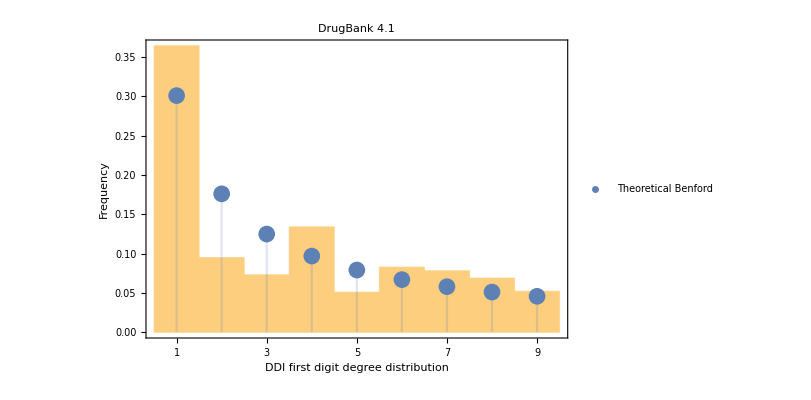

```mathematica
(*Show[Histogram[dataF,"Sturges", "Probability", Frame ->True, FrameLabel->{Style["DDI degree first digit",14],Style["Frequency", 14]}, Ticks->{{1,2,3,4,5,6,7,8,9},{0.00, 0.05, 0.10, 0.15, 0.20, 0.25, 0.30, 0.35}}], DiscretePlot[{Table[PDF[BenfordDistribution[10],x]]}, {x, 1, 9},PlotLegends->Placed[{"Theoretical Benford"}, {0.5,0.9}], PlotMarkers->Style["•", FontSize -> 30]]]*)

Show[Histogram[dataF,"Sturges", "Probability", Frame ->True, ImageSize->600,AspectRatio->1/1.5,  FrameLabel->{Style["DDI first digit degree distribution",16, Black],Style["Frequency", 16, Black]},  FrameStyle->Directive[14,Black],FrameTicks->{{Automatic,Automatic},{{{1,"1"},{2,"2"},{3,"3"}, {4,"4"},{5,"5"},{6,"6"}, {7,"7"},{8,"8"},{9,"9"}},{}}}],DiscretePlot[{Table[PDF[BenfordDistribution[10],x]]}, {x, 1, 9},PlotLegends->Placed[{Style["Theoretical Benford",16]}, {0.5,0.9}],PlotStyle->{AbsolutePointSize[12]}], PlotLabel->Style["DrugBank 4.1",Black,16]]
```

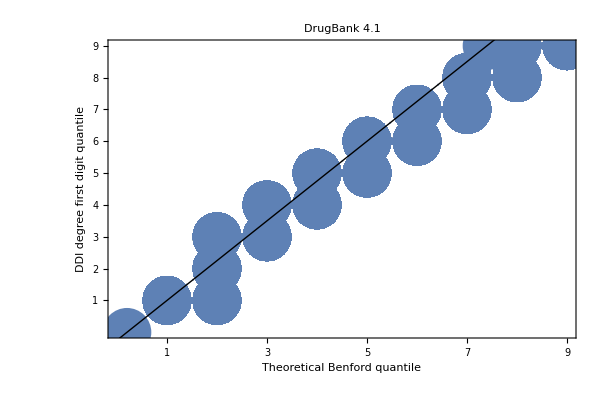

```mathematica
(*Show[QuantilePlot[dataF,BenfordDistribution[10], PlotMarkers->Style["•", FontSize -> 38]],RotateLabel->True, Frame->True,FrameLabel->{Style["Theoretical Benford quantile",14],Style["DDI degree first digit quantile",14]}]*)

Show[QuantilePlot[dataF,BenfordDistribution[10], ImageSize->600,AspectRatio->1/1.5, PlotMarkers->Style["•", FontSize -> 50]],TicksStyle -> Directive[14,Black], RotateLabel->True, Frame->True, FrameStyle->Directive[14,Black],FrameTicks->{{{1,2,3,4,5,6,7,8,9},None},{{1,2,3,4,5,6,7,8,9},None}},FrameLabel->{Style["Theoretical Benford quantile",Black, 16],Style["DDI degree first digit quantile",Black,16]}, PlotLabel->Style["DrugBank 4.1",Black,16]]
```

```mathematica
PearsonChiSquareTest[dataF,BenfordDistribution[10], "TestConclusion"]
WatsonUSquareTest[dataF,BenfordDistribution[10],"TestConclusion"]
chisqDeg=PearsonChiSquareTest[dataF,BenfordDistribution[10]]
wuDeg =WatsonUSquareTest[dataF,BenfordDistribution[10]]
```

The null hypothesis that the data is distributed according to the BenfordDistribution[10] is not rejected at the 5 percent level based on the Pearson χ^2 test.

WatsonUSquareTest::dscrt: The p-value returned by the WatsonUSquare test may not reflect the true size of the test for discrete test distributions.

WatsonUSquareTest::ties: Ties exist in the data and will be ignored for the WatsonUSquare test, which assumes unique values.

WatsonUSquareTest::dscrt: The p-value returned by the WatsonUSquare test may not reflect the true size of the test for discrete test distributions.

WatsonUSquareTest::ties: Ties exist in the data and will be ignored for the WatsonUSquare test, which assumes unique values.

The null hypothesis that the data is distributed according to the BenfordDistribution[10] is rejected at the 5 percent level based on the Watson U^2 test.

0.0731199

WatsonUSquareTest::dscrt: The p-value returned by the WatsonUSquare test may not reflect the true size of the test for discrete test distributions.

WatsonUSquareTest::ties: Ties exist in the data and will be ignored for the WatsonUSquare test, which assumes unique values.

```mathematica
0.0027927605138453222
dfT =Sort[Tally[dataF]]
```

0.00279276

```mathematica
{{1,394},{2,215},{3,142},{4,112},{5,73},{6,62},{7,61},{8,60},{9,48}}
numberDfT = Length[dataF]
```

{{1,394},{2,215},{3,142},{4,112},{5,73},{6,62},{7,61},{8,60},{9,48}}

1167

```mathematica
dfT =Tally[dataF]
```

{{2 ,215 },{,394 },{5 ,73 },{9 ,48 },{8 ,60 },{7 ,61 },{3 ,142 },{4 ,112 },{6 ,62 }}

```mathematica
dataDDIbet = List[1,37169,7803,0,37523,7544,0,294,282,16,478,1160,7255,1742,5945,0,5126,11,6953,424,0,56,4015,429,15,0,8,3418,70,2979,65,3973,43,0,0,103,3088,140,584,34,0,1315,144,0,0,5298,0,0,2069,44,97,97,2428,473,297,191,721,3087,1149,7664,433,1668,3713,346,2102,460,65,594,138,2457,721,1328,86,2566,1612,1658,2378,2673,397,2819,2902,1114,788,97,102,603,495,10,287,38,139,184,1,3181,201,266,1230,254,681,4665,604,0,24,77,77,77,382,949,12,1472,3,34895,367,1257,633,26,2005,0,0,0,0,1,7,0,4328,1219,10,0,0,0,0,33218,82,1861,0,40,395,0,337,40,83,623,177,219,811,2,2,0,1423,454,81,0,620,1273,0,282,720,1173,307,5,16685,1372,1708,1422,40,1422,1723,0,2093,4595,219,73,91,0,2700,30491,696,0,0,277,724,0,59,2411,462,69,302,116,4437,1484,0,68,281,1394,0,315,216,0,84,1210,3130,741,1706,0,61,388,339,453,1922,259,1494,8943,5979,170,804,177,523,2366,0,1266,0,0,1962,0,64,8907,3247,5,6376,115,2215,5136,1406,1517,1551,22019,155,802,4918,1933,0,1356,59,16376,734,621,98,32,58,302,281,295,564,6618,0,47,1756,3268,1995,213,9576,339,34129,2834,1305,827,251,1419,2374,857,19,421,887,6704,90,144,15553,3120,5134,1366,92,322,2406,29,0,425,887,2604,218,1341,191,2309,2,747,5736,252,3,19073,11157,281,184,21599,21288,2698,1993,6897,1436,832,133,51,317,2105,4257,2,2840,155,8964,4451,651,561,6125,1091,101,446,1370,12647,518,3325,1228,2585,723,155,155,155,155,3328,145,4158,420,211,7,13,4,124,134,134,14,834,280,2715,132,0,0,1029,0,0,2725,736,15127,3660,3576,640,8259,2407,0,0,0,654,246,467,15,19,0,111,4039,2016,7834,3478,1160,0,198,292,7490,1,2435,0,23,24,355,98,112,1,2650,536,0,1052,20,32,76,1539,265,7715,97,786,126,9486,40,0,2454,2817,2180,18,2423,845,6793,229,142,27735,76,1083,47570,2880,121,46,2250,1719,600,147,284,221,40,5182,2841,7537,2257,2614,449,130,3002,147,55,20,185,35,224,8279,2292,2761,192,1586,600,2264,13361,1731,13223,221,235,221,646,8537,959,501,1208,52,267,711,1504,18,0,0,270,1365,260,3871,337,313,635,924,1325,49,10,3932,48,1654,38,18,597,664,127,353,329,672,672,130,46,94,225,99,672,53,105,86,48,26,0,22,33,44,44,22,22,75,113,2,1742,91,1165,4,131,226,5,364,1004,131,11452,10240,341,17,1356,1938,5945,123,11571,373,98,254,767,3,14,52,1546,538,1160,16,977,233,58,63,213,361,78,5459,0,487,416,2954,150,472,130,8,5640,170,3026,610,170,1405,7,122,673,500,412,163,1227,105,346,37,211,8,1929,1367,0,173,835,300,1222,934,1820,66,743,606,2353,6,164,401,355,464,2250,214,414,8,291,50,29,117,2371,707,3388,2410,2167,0,591,591,100,173,111,108,934,579,1059,52,8,11,28,292,283,123,67,10,1522,38,251,0,880,4068,673,10,6,3,0,8,4,2,173,6,115,689,2,174,0,0,53,194,9620,0,268,3,194,1168,313,4,6,6,3,7575,119,0,0,6,0,678,0,3,6,1860,14,136,3,102,3,0,97,3,2,0,940,42,112,338,28,139,2419,169,37,52,2243,26,2319,2939,1235,2878,178,1046,111,1158,2837,101,0,31,140,95,51,31,0,2394,395,91,59,180,326,15,3,156,11,418,0,76,25,255,7462,100,100,22,199,426,196,100,79,30,53,82,1299,31,0,0,501,14,0,181,204,37,0,372,0,187,1709,13,0,67,155,244,11,199,11,0,129,23,1211,120,19,6,0,5,1579,701,340,762,70,3,18,8,186,288,288,288,377,701,2751,72,0,23,23,3,63,13,12,183,9,12,1540,29,0,207,59,210,28,0,0,29,27,3,0,368,29,0,29,469,86,3,0,29,6,0,762,109,43,75,335,1925,429,1481,20,84,15,4,2,2258,20,9,40,731,741,37,38,1,3,46,116,1623,10,10,18,537,24,18,357,0,1025,272,0,46,635,635,323,29,113,1199,50,0,14752,39,30,29,28,0,20,1,0,295,2345,0,12,1,35,291,0,0,159,10,76,1438,2721,194,116,48,47,7,35,35,14,16,246,124,0,447,0,981,41,45,30,29,0,0,45,849,981,1,63,0,243,34,12,0,0,12,14,0,0,0,1805,158,144,144,17,29,17,145,17,395,101,0,25,144,59,35,12,809,17,10,487,7,132,60,169,171,842,0,0,3,25,28,704,0,0,0,0,0,0,0,0,3,0,1,0,0,12,1,51,0,0,2,159,2,14,2,2,2,10,4,4,17,6,4,142,24,0,9,0,9,19,16,521,0,60,22,45,0,2046,0,193,45,16,22,0,16,0,26,0,11,6,23,238,303,85,1160,44,662,1081,310,473,0,37,0,1193,19,22,0,93,3,1299,46,3,46,46,46,3,46,46,0,0,23,79,36,15,0,4,0,0,2,235,3,0,1160,0,0,0,0,55,0,2,2,2,2,1,0,0,0,0,0,239,0,0,0,0,0,5,1,0,0,0,0,0,0,0,30,0,1,0,0,0,0,0,0,0,0,7,0,152,34,79,0,68,91,0,0,0,0,0,0,0,0,0,1167,0,161,0,0,0,1,65,0,3,13,0,1,0,0,20,0,72,0,0,0,0,0,0,0,0,0,0,0,0,12,0,0,0,10,0,0,0,0,0,0,54,0,0,0,0]
```

{1,37169,7803,0,37523,7544,0,294,282,16,478,1160,7255,1742,5945,0,5126,11,6953,424,0,56,4015,429,15,0,8,3418,70,2979,65,3973,43,0,0,103,3088,140,584,34,0,1315,144,0,0,5298,0,0,2069,44,97,97,2428,473,297,191,721,3087,1149,7664,433,1668,3713,346,2102,460,65,594,138,2457,721,1328,86,2566,1612,1658,2378,2673,397,2819,2902,1114,788,97,102,603,495,10,287,38,139,184,1,3181,201,266,1230,254,681,4665,604,0,24,77,77,77,382,949,12,1472,3,34895,367,1257,633,26,2005,0,0,0,0,1,7,0,4328,1219,10,0,0,0,0,33218,82,1861,0,40,395,0,337,40,83,623,177,219,811,2,2,0,1423,454,81,0,620,1273,0,282,720,1173,307,5,16685,1372,1708,1422,40,1422,1723,0,2093,4595,219,73,91,0,2700,30491,696,0,0,277,724,0,59,2411,462,69,302,116,4437,1484,0,68,281,1394,0,315,216,0,84,1210,3130,741,1706,0,61,388,339,453,1922,259,1494,8943,5979,170,804,177,523,2366,0,1266,0,0,1962,0,64,8907,3247,5,6376,115,2215,5136,1406,1517,1551,22019,155,802,4918,1933,0,1356,59,16376,734,621,98,32,58,302,281,295,564,6618,0,47,1756,3268,1995,213,9576,339,34129,2834,1305,827,251,1419,2374,857,19,421,887,6704,90,144,15553,3120,5134,1366,92,322,2406,29,0,425,887,2604,218,1341,191,2309,2,747,5736,252,3,19073,11157,281,184,21599,21288,2698,1993,6897,1436,832,133,51,317,2105,4257,2,2840,155,8964,4451,651,561,6125,1091,101,446,1370,12647,518,3325,1228,2585,723,155,155,155,155,3328,145,4158,420,211,7,13,4,124,134,134,14,834,280,2715,132,0,0,1029,0,0,2725,736,15127,3660,3576,640,8259,2407,0,0,0,654,246,467,15,19,0,111,4039,2016,7834,3478,1160,0,198,292,7490,1,2435,0,23,24,355,98,112,1,2650,536,0,1052,20,32,76,1539,265,7715,97,786,126,9486,40,0,2454,2817,2180,18,2423,845,6793,229,142,27735,76,1083,47570,2880,121,46,2250,1719,600,147,284,221,40,5182,2841,7537,2257,2614,449,130,3002,147,55,20,185,35,224,8279,2292,2761,192,1586,600,2264,13361,1731,13223,221,235,221,646,8537,959,501,1208,52,267,711,1504,18,0,0,270,1365,260,3871,337,313,635,924,1325,49,10,3932,48,1654,38,18,597,664,127,353,329,672,672,130,46,94,225,99,672,53,105,86,48,26,0,22,33,44,44,22,22,75,113,2,1742,91,1165,4,131,226,5,364,1004,131,11452,10240,341,17,1356,1938,5945,123,11571,373,98,254,767,3,14,52,1546,538,1160,16,977,233,58,63,213,361,78,5459,0,487,416,2954,150,472,130,8,5640,170,3026,610,170,1405,7,122,673,500,412,163,1227,105,346,37,211,8,1929,1367,0,173,835,300,1222,934,1820,66,743,606,2353,6,164,401,355,464,2250,214,414,8,291,50,29,117,2371,707,3388,2410,2167,0,591,591,100,173,111,108,934,579,1059,52,8,11,28,292,283,123,67,10,1522,38,251,0,880,4068,673,10,6,3,0,8,4,2,173,6,115,689,2,174,0,0,53,194,9620,0,268,3,194,1168,313,4,6,6,3,7575,119,0,0,6,0,678,0,3,6,1860,14,136,3,102,3,0,97,3,2,0,940,42,112,338,28,139,2419,169,37,52,2243,26,2319,2939,1235,2878,178,1046,111,1158,2837,101,0,31,140,95,51,31,0,2394,395,91,59,180,326,15,3,156,11,418,0,76,25,255,7462,100,100,22,199,426,196,100,79,30,53,82,1299,31,0,0,501,14,0,181,204,37,0,372,0,187,1709,13,0,67,155,244,11,199,11,0,129,23,1211,120,19,6,0,5,1579,701,340,762,70,3,18,8,186,288,288,288,377,701,2751,72,0,23,23,3,63,13,12,183,9,12,1540,29,0,207,59,210,28,0,0,29,27,3,0,368,29,0,29,469,86,3,0,29,6,0,762,109,43,75,335,1925,429,1481,20,84,15,4,2,2258,20,9,40,731,741,37,38,1,3,46,116,1623,10,10,18,537,24,18,357,0,1025,272,0,46,635,635,323,29,113,1199,50,0,14752,39,30,29,28,0,20,1,0,295,2345,0,12,1,35,291,0,0,159,10,76,1438,2721,194,116,48,47,7,35,35,14,16,246,124,0,447,0,981,41,45,30,29,0,0,45,849,981,1,63,0,243,34,12,0,0,12,14,0,0,0,1805,158,144,144,17,29,17,145,17,395,101,0,25,144,59,35,12,809,17,10,487,7,132,60,169,171,842,0,0,3,25,28,704,0,0,0,0,0,0,0,0,3,0,1,0,0,12,1,51,0,0,2,159,2,14,2,2,2,10,4,4,17,6,4,142,24,0,9,0,9,19,16,521,0,60,22,45,0,2046,0,193,45,16,22,0,16,0,26,0,11,6,23,238,303,85,1160,44,662,1081,310,473,0,37,0,1193,19,22,0,93,3,1299,46,3,46,46,46,3,46,46,0,0,23,79,36,15,0,4,0,0,2,235,3,0,1160,0,0,0,0,55,0,2,2,2,2,1,0,0,0,0,0,239,0,0,0,0,0,5,1,0,0,0,0,0,0,0,30,0,1,0,0,0,0,0,0,0,0,7,0,152,34,79,0,68,91,0,0,0,0,0,0,0,0,0,1167,0,161,0,0,0,1,65,0,3,13,0,1,0,0,20,0,72,0,0,0,0,0,0,0,0,0,0,0,0,12,0,0,0,10,0,0,0,0,0,0,54,0,0,0,0}

```mathematica
dataDDIbet = List[1,37169,7803,0,37523,7544,0,294,282,16,478,1160,7255,1742,5945,0,5126,11,6953,424,0,56,4015,429,15,0,8,3418,70,2979,65,3973,43,0,0,103,3088,140,584,34,0,1315,144,0,0,5298,0,0,2069,44,97,97,2428,473,297,191,721,3087,1149,7664,433,1668,3713,346,2102,460,65,594,138,2457,721,1328,86,2566,1612,1658,2378,2673,397,2819,2902,1114,788,97,102,603,495,10,287,38,139,184,1,3181,201,266,1230,254,681,4665,604,0,24,77,77,77,382,949,12,1472,3,34895,367,1257,633,26,2005,0,0,0,0,1,7,0,4328,1219,10,0,0,0,0,33218,82,1861,0,40,395,0,337,40,83,623,177,219,811,2,2,0,1423,454,81,0,620,1273,0,282,720,1173,307,5,16685,1372,1708,1422,40,1422,1723,0,2093,4595,219,73,91,0,2700,30491,696,0,0,277,724,0,59,2411,462,69,302,116,4437,1484,0,68,281,1394,0,315,216,0,84,1210,3130,741,1706,0,61,388,339,453,1922,259,1494,8943,5979,170,804,177,523,2366,0,1266,0,0,1962,0,64,8907,3247,5,6376,115,2215,5136,1406,1517,1551,22019,155,802,4918,1933,0,1356,59,16376,734,621,98,32,58,302,281,295,564,6618,0,47,1756,3268,1995,213,9576,339,34129,2834,1305,827,251,1419,2374,857,19,421,887,6704,90,144,15553,3120,5134,1366,92,322,2406,29,0,425,887,2604,218,1341,191,2309,2,747,5736,252,3,19073,11157,281,184,21599,21288,2698,1993,6897,1436,832,133,51,317,2105,4257,2,2840,155,8964,4451,651,561,6125,1091,101,446,1370,12647,518,3325,1228,2585,723,155,155,155,155,3328,145,4158,420,211,7,13,4,124,134,134,14,834,280,2715,132,0,0,1029,0,0,2725,736,15127,3660,3576,640,8259,2407,0,0,0,654,246,467,15,19,0,111,4039,2016,7834,3478,1160,0,198,292,7490,1,2435,0,23,24,355,98,112,1,2650,536,0,1052,20,32,76,1539,265,7715,97,786,126,9486,40,0,2454,2817,2180,18,2423,845,6793,229,142,27735,76,1083,47570,2880,121,46,2250,1719,600,147,284,221,40,5182,2841,7537,2257,2614,449,130,3002,147,55,20,185,35,224,8279,2292,2761,192,1586,600,2264,13361,1731,13223,221,235,221,646,8537,959,501,1208,52,267,711,1504,18,0,0,270,1365,260,3871,337,313,635,924,1325,49,10,3932,48,1654,38,18,597,664,127,353,329,672,672,130,46,94,225,99,672,53,105,86,48,26,0,22,33,44,44,22,22,75,113,2,1742,91,1165,4,131,226,5,364,1004,131,11452,10240,341,17,1356,1938,5945,123,11571,373,98,254,767,3,14,52,1546,538,1160,16,977,233,58,63,213,361,78,5459,0,487,416,2954,150,472,130,8,5640,170,3026,610,170,1405,7,122,673,500,412,163,1227,105,346,37,211,8,1929,1367,0,173,835,300,1222,934,1820,66,743,606,2353,6,164,401,355,464,2250,214,414,8,291,50,29,117,2371,707,3388,2410,2167,0,591,591,100,173,111,108,934,579,1059,52,8,11,28,292,283,123,67,10,1522,38,251,0,880,4068,673,10,6,3,0,8,4,2,173,6,115,689,2,174,0,0,53,194,9620,0,268,3,194,1168,313,4,6,6,3,7575,119,0,0,6,0,678,0,3,6,1860,14,136,3,102,3,0,97,3,2,0,940,42,112,338,28,139,2419,169,37,52,2243,26,2319,2939,1235,2878,178,1046,111,1158,2837,101,0,31,140,95,51,31,0,2394,395,91,59,180,326,15,3,156,11,418,0,76,25,255,7462,100,100,22,199,426,196,100,79,30,53,82,1299,31,0,0,501,14,0,181,204,37,0,372,0,187,1709,13,0,67,155,244,11,199,11,0,129,23,1211,120,19,6,0,5,1579,701,340,762,70,3,18,8,186,288,288,288,377,701,2751,72,0,23,23,3,63,13,12,183,9,12,1540,29,0,207,59,210,28,0,0,29,27,3,0,368,29,0,29,469,86,3,0,29,6,0,762,109,43,75,335,1925,429,1481,20,84,15,4,2,2258,20,9,40,731,741,37,38,1,3,46,116,1623,10,10,18,537,24,18,357,0,1025,272,0,46,635,635,323,29,113,1199,50,0,14752,39,30,29,28,0,20,1,0,295,2345,0,12,1,35,291,0,0,159,10,76,1438,2721,194,116,48,47,7,35,35,14,16,246,124,0,447,0,981,41,45,30,29,0,0,45,849,981,1,63,0,243,34,12,0,0,12,14,0,0,0,1805,158,144,144,17,29,17,145,17,395,101,0,25,144,59,35,12,809,17,10,487,7,132,60,169,171,842,0,0,3,25,28,704,0,0,0,0,0,0,0,0,3,0,1,0,0,12,1,51,0,0,2,159,2,14,2,2,2,10,4,4,17,6,4,142,24,0,9,0,9,19,16,521,0,60,22,45,0,2046,0,193,45,16,22,0,16,0,26,0,11,6,23,238,303,85,1160,44,662,1081,310,473,0,37,0,1193,19,22,0,93,3,1299,46,3,46,46,46,3,46,46,0,0,23,79,36,15,0,4,0,0,2,235,3,0,1160,0,0,0,0,55,0,2,2,2,2,1,0,0,0,0,0,239,0,0,0,0,0,5,1,0,0,0,0,0,0,0,30,0,1,0,0,0,0,0,0,0,0,7,0,152,34,79,0,68,91,0,0,0,0,0,0,0,0,0,1167,0,161,0,0,0,1,65,0,3,13,0,1,0,0,20,0,72,0,0,0,0,0,0,0,0,0,0,0,0,12,0,0,0,10,0,0,0,0,0,0,54,0,0,0,0]
```

```mathematica
{1,37169,7803,0,37523,7544,0,294,282,16,478,1160,7255,1742,5945,0,5126,11,6953,424,0,56,4015,429,15,0,8,3418,70,2979,65,3973,43,0,0,103,3088,140,584,34,0,1315,144,0,0,5298,0,0,2069,44,97,97,2428,473,297,191,721,3087,1149,7664,433,1668,3713,346,2102,460,65,594,138,2457,721,1328,86,2566,1612,1658,2378,2673,397,2819,2902,1114,788,97,102,603,495,10,287,38,139,184,1,3181,201,266,1230,254,681,4665,604,0,24,77,77,77,382,949,12,1472,3,34895,367,1257,633,26,2005,0,0,0,0,1,7,0,4328,1219,10,0,0,0,0,33218,82,1861,0,40,395,0,337,40,83,623,177,219,811,2,2,0,1423,454,81,0,620,1273,0,282,720,1173,307,5,16685,1372,1708,1422,40,1422,1723,0,2093,4595,219,73,91,0,2700,30491,696,0,0,277,724,0,59,2411,462,69,302,116,4437,1484,0,68,281,1394,0,315,216,0,84,1210,3130,741,1706,0,61,388,339,453,1922,259,1494,8943,5979,170,804,177,523,2366,0,1266,0,0,1962,0,64,8907,3247,5,6376,115,2215,5136,1406,1517,1551,22019,155,802,4918,1933,0,1356,59,16376,734,621,98,32,58,302,281,295,564,6618,0,47,1756,3268,1995,213,9576,339,34129,2834,1305,827,251,1419,2374,857,19,421,887,6704,90,144,15553,3120,5134,1366,92,322,2406,29,0,425,887,2604,218,1341,191,2309,2,747,5736,252,3,19073,11157,281,184,21599,21288,2698,1993,6897,1436,832,133,51,317,2105,4257,2,2840,155,8964,4451,651,561,6125,1091,101,446,1370,12647,518,3325,1228,2585,723,155,155,155,155,3328,145,4158,420,211,7,13,4,124,134,134,14,834,280,2715,132,0,0,1029,0,0,2725,736,15127,3660,3576,640,8259,2407,0,0,0,654,246,467,15,19,0,111,4039,2016,7834,3478,1160,0,198,292,7490,1,2435,0,23,24,355,98,112,1,2650,536,0,1052,20,32,76,1539,265,7715,97,786,126,9486,40,0,2454,2817,2180,18,2423,845,6793,229,142,27735,76,1083,47570,2880,121,46,2250,1719,600,147,284,221,40,5182,2841,7537,2257,2614,449,130,3002,147,55,20,185,35,224,8279,2292,2761,192,1586,600,2264,13361,1731,13223,221,235,221,646,8537,959,501,1208,52,267,711,1504,18,0,0,270,1365,260,3871,337,313,635,924,1325,49,10,3932,48,1654,38,18,597,664,127,353,329,672,672,130,46,94,225,99,672,53,105,86,48,26,0,22,33,44,44,22,22,75,113,2,1742,91,1165,4,131,226,5,364,1004,131,11452,10240,341,17,1356,1938,5945,123,11571,373,98,254,767,3,14,52,1546,538,1160,16,977,233,58,63,213,361,78,5459,0,487,416,2954,150,472,130,8,5640,170,3026,610,170,1405,7,122,673,500,412,163,1227,105,346,37,211,8,1929,1367,0,173,835,300,1222,934,1820,66,743,606,2353,6,164,401,355,464,2250,214,414,8,291,50,29,117,2371,707,3388,2410,2167,0,591,591,100,173,111,108,934,579,1059,52,8,11,28,292,283,123,67,10,1522,38,251,0,880,4068,673,10,6,3,0,8,4,2,173,6,115,689,2,174,0,0,53,194,9620,0,268,3,194,1168,313,4,6,6,3,7575,119,0,0,6,0,678,0,3,6,1860,14,136,3,102,3,0,97,3,2,0,940,42,112,338,28,139,2419,169,37,52,2243,26,2319,2939,1235,2878,178,1046,111,1158,2837,101,0,31,140,95,51,31,0,2394,395,91,59,180,326,15,3,156,11,418,0,76,25,255,7462,100,100,22,199,426,196,100,79,30,53,82,1299,31,0,0,501,14,0,181,204,37,0,372,0,187,1709,13,0,67,155,244,11,199,11,0,129,23,1211,120,19,6,0,5,1579,701,340,762,70,3,18,8,186,288,288,288,377,701,2751,72,0,23,23,3,63,13,12,183,9,12,1540,29,0,207,59,210,28,0,0,29,27,3,0,368,29,0,29,469,86,3,0,29,6,0,762,109,43,75,335,1925,429,1481,20,84,15,4,2,2258,20,9,40,731,741,37,38,1,3,46,116,1623,10,10,18,537,24,18,357,0,1025,272,0,46,635,635,323,29,113,1199,50,0,14752,39,30,29,28,0,20,1,0,295,2345,0,12,1,35,291,0,0,159,10,76,1438,2721,194,116,48,47,7,35,35,14,16,246,124,0,447,0,981,41,45,30,29,0,0,45,849,981,1,63,0,243,34,12,0,0,12,14,0,0,0,1805,158,144,144,17,29,17,145,17,395,101,0,25,144,59,35,12,809,17,10,487,7,132,60,169,171,842,0,0,3,25,28,704,0,0,0,0,0,0,0,0,3,0,1,0,0,12,1,51,0,0,2,159,2,14,2,2,2,10,4,4,17,6,4,142,24,0,9,0,9,19,16,521,0,60,22,45,0,2046,0,193,45,16,22,0,16,0,26,0,11,6,23,238,303,85,1160,44,662,1081,310,473,0,37,0,1193,19,22,0,93,3,1299,46,3,46,46,46,3,46,46,0,0,23,79,36,15,0,4,0,0,2,235,3,0,1160,0,0,0,0,55,0,2,2,2,2,1,0,0,0,0,0,239,0,0,0,0,0,5,1,0,0,0,0,0,0,0,30,0,1,0,0,0,0,0,0,0,0,7,0,152,34,79,0,68,91,0,0,0,0,0,0,0,0,0,1167,0,161,0,0,0,1,65,0,3,13,0,1,0,0,20,0,72,0,0,0,0,0,0,0,0,0,0,0,0,12,0,0,0,10,0,0,0,0,0,0,54,0,0,0,0}
```

{1,37169,7803,0,37523,7544,0,294,282,16,478,1160,7255,1742,5945,0,5126,11,6953,424,0,56,4015,429,15,0,8,3418,70,2979,65,3973,43,0,0,103,3088,140,584,34,0,1315,144,0,0,5298,0,0,2069,44,97,97,2428,473,297,191,721,3087,1149,7664,433,1668,3713,346,2102,460,65,594,138,2457,721,1328,86,2566,1612,1658,2378,2673,397,2819,2902,1114,788,97,102,603,495,10,287,38,139,184,1,3181,201,266,1230,254,681,4665,604,0,24,77,77,77,382,949,12,1472,3,34895,367,1257,633,26,2005,0,0,0,0,1,7,0,4328,1219,10,0,0,0,0,33218,82,1861,0,40,395,0,337,40,83,623,177,219,811,2,2,0,1423,454,81,0,620,1273,0,282,720,1173,307,5,16685,1372,1708,1422,40,1422,1723,0,2093,4595,219,73,91,0,2700,30491,696,0,0,277,724,0,59,2411,462,69,302,116,4437,1484,0,68,281,1394,0,315,216,0,84,1210,3130,741,1706,0,61,388,339,453,1922,259,1494,8943,5979,170,804,177,523,2366,0,1266,0,0,1962,0,64,8907,3247,5,6376,115,2215,5136,1406,1517,1551,22019,155,802,4918,1933,0,1356,59,16376,734,621,98,32,58,302,281,295,564,6618,0,47,1756,3268,1995,213,9576,339,34129,2834,1305,827,251,1419,2374,857,19,421,887,6704,90,144,15553,3120,5134,1366,92,322,2406,29,0,425,887,2604,218,1341,191,2309,2,747,5736,252,3,19073,11157,281,184,21599,21288,2698,1993,6897,1436,832,133,51,317,2105,4257,2,2840,155,8964,4451,651,561,6125,1091,101,446,1370,12647,518,3325,1228,2585,723,155,155,155,155,3328,145,4158,420,211,7,13,4,124,134,134,14,834,280,2715,132,0,0,1029,0,0,2725,736,15127,3660,3576,640,8259,2407,0,0,0,654,246,467,15,19,0,111,4039,2016,7834,3478,1160,0,198,292,7490,1,2435,0,23,24,355,98,112,1,2650,536,0,1052,20,32,76,1539,265,7715,97,786,126,9486,40,0,2454,2817,2180,18,2423,845,6793,229,142,27735,76,1083,47570,2880,121,46,2250,1719,600,147,284,221,40,5182,2841,7537,2257,2614,449,130,3002,147,55,20,185,35,224,8279,2292,2761,192,1586,600,2264,13361,1731,13223,221,235,221,646,8537,959,501,1208,52,267,711,1504,18,0,0,270,1365,260,3871,337,313,635,924,1325,49,10,3932,48,1654,38,18,597,664,127,353,329,672,672,130,46,94,225,99,672,53,105,86,48,26,0,22,33,44,44,22,22,75,113,2,1742,91,1165,4,131,226,5,364,1004,131,11452,10240,341,17,1356,1938,5945,123,11571,373,98,254,767,3,14,52,1546,538,1160,16,977,233,58,63,213,361,78,5459,0,487,416,2954,150,472,130,8,5640,170,3026,610,170,1405,7,122,673,500,412,163,1227,105,346,37,211,8,1929,1367,0,173,835,300,1222,934,1820,66,743,606,2353,6,164,401,355,464,2250,214,414,8,291,50,29,117,2371,707,3388,2410,2167,0,591,591,100,173,111,108,934,579,1059,52,8,11,28,292,283,123,67,10,1522,38,251,0,880,4068,673,10,6,3,0,8,4,2,173,6,115,689,2,174,0,0,53,194,9620,0,268,3,194,1168,313,4,6,6,3,7575,119,0,0,6,0,678,0,3,6,1860,14,136,3,102,3,0,97,3,2,0,940,42,112,338,28,139,2419,169,37,52,2243,26,2319,2939,1235,2878,178,1046,111,1158,2837,101,0,31,140,95,51,31,0,2394,395,91,59,180,326,15,3,156,11,418,0,76,25,255,7462,100,100,22,199,426,196,100,79,30,53,82,1299,31,0,0,501,14,0,181,204,37,0,372,0,187,1709,13,0,67,155,244,11,199,11,0,129,23,1211,120,19,6,0,5,1579,701,340,762,70,3,18,8,186,288,288,288,377,701,2751,72,0,23,23,3,63,13,12,183,9,12,1540,29,0,207,59,210,28,0,0,29,27,3,0,368,29,0,29,469,86,3,0,29,6,0,762,109,43,75,335,1925,429,1481,20,84,15,4,2,2258,20,9,40,731,741,37,38,1,3,46,116,1623,10,10,18,537,24,18,357,0,1025,272,0,46,635,635,323,29,113,1199,50,0,14752,39,30,29,28,0,20,1,0,295,2345,0,12,1,35,291,0,0,159,10,76,1438,2721,194,116,48,47,7,35,35,14,16,246,124,0,447,0,981,41,45,30,29,0,0,45,849,981,1,63,0,243,34,12,0,0,12,14,0,0,0,1805,158,144,144,17,29,17,145,17,395,101,0,25,144,59,35,12,809,17,10,487,7,132,60,169,171,842,0,0,3,25,28,704,0,0,0,0,0,0,0,0,3,0,1,0,0,12,1,51,0,0,2,159,2,14,2,2,2,10,4,4,17,6,4,142,24,0,9,0,9,19,16,521,0,60,22,45,0,2046,0,193,45,16,22,0,16,0,26,0,11,6,23,238,303,85,1160,44,662,1081,310,473,0,37,0,1193,19,22,0,93,3,1299,46,3,46,46,46,3,46,46,0,0,23,79,36,15,0,4,0,0,2,235,3,0,1160,0,0,0,0,55,0,2,2,2,2,1,0,0,0,0,0,239,0,0,0,0,0,5,1,0,0,0,0,0,0,0,30,0,1,0,0,0,0,0,0,0,0,7,0,152,34,79,0,68,91,0,0,0,0,0,0,0,0,0,1167,0,161,0,0,0,1,65,0,3,13,0,1,0,0,20,0,72,0,0,0,0,0,0,0,0,0,0,0,0,12,0,0,0,10,0,0,0,0,0,0,54,0,0,0,0}

```mathematica
cleanDDIbet=DeleteCases[dataDDIbet,0,Infinity]
```

{1,37169,7803,37523,7544,294,282,16,478,1160,7255,1742,5945,5126,11,6953,424,56,4015,429,15,8,3418,70,2979,65,3973,43,103,3088,140,584,34,1315,144,5298,2069,44,97,97,2428,473,297,191,721,3087,1149,7664,433,1668,3713,346,2102,460,65,594,138,2457,721,1328,86,2566,1612,1658,2378,2673,397,2819,2902,1114,788,97,102,603,495,10,287,38,139,184,1,3181,201,266,1230,254,681,4665,604,24,77,77,77,382,949,12,1472,3,34895,367,1257,633,26,2005,1,7,4328,1219,10,33218,82,1861,40,395,337,40,83,623,177,219,811,2,2,1423,454,81,620,1273,282,720,1173,307,5,16685,1372,1708,1422,40,1422,1723,2093,4595,219,73,91,2700,30491,696,277,724,59,2411,462,69,302,116,4437,1484,68,281,1394,315,216,84,1210,3130,741,1706,61,388,339,453,1922,259,1494,8943,5979,170,804,177,523,2366,1266,1962,64,8907,3247,5,6376,115,2215,5136,1406,1517,1551,22019,155,802,4918,1933,1356,59,16376,734,621,98,32,58,302,281,295,564,6618,47,1756,3268,1995,213,9576,339,34129,2834,1305,827,251,1419,2374,857,19,421,887,6704,90,144,15553,3120,5134,1366,92,322,2406,29,425,887,2604,218,1341,191,2309,2,747,5736,252,3,19073,11157,281,184,21599,21288,2698,1993,6897,1436,832,133,51,317,2105,4257,2,2840,155,8964,4451,651,561,6125,1091,101,446,1370,12647,518,3325,1228,2585,723,155,155,155,155,3328,145,4158,420,211,7,13,4,124,134,134,14,834,280,2715,132,1029,2725,736,15127,3660,3576,640,8259,2407,654,246,467,15,19,111,4039,2016,7834,3478,1160,198,292,7490,1,2435,23,24,355,98,112,1,2650,536,1052,20,32,76,1539,265,7715,97,786,126,9486,40,2454,2817,2180,18,2423,845,6793,229,142,27735,76,1083,47570,2880,121,46,2250,1719,600,147,284,221,40,5182,2841,7537,2257,2614,449,130,3002,147,55,20,185,35,224,8279,2292,2761,192,1586,600,2264,13361,1731,13223,221,235,221,646,8537,959,501,1208,52,267,711,1504,18,270,1365,260,3871,337,313,635,924,1325,49,10,3932,48,1654,38,18,597,664,127,353,329,672,672,130,46,94,225,99,672,53,105,86,48,26,22,33,44,44,22,22,75,113,2,1742,91,1165,4,131,226,5,364,1004,131,11452,10240,341,17,1356,1938,5945,123,11571,373,98,254,767,3,14,52,1546,538,1160,16,977,233,58,63,213,361,78,5459,487,416,2954,150,472,130,8,5640,170,3026,610,170,1405,7,122,673,500,412,163,1227,105,346,37,211,8,1929,1367,173,835,300,1222,934,1820,66,743,606,2353,6,164,401,355,464,2250,214,414,8,291,50,29,117,2371,707,3388,2410,2167,591,591,100,173,111,108,934,579,1059,52,8,11,28,292,283,123,67,10,1522,38,251,880,4068,673,10,6,3,8,4,2,173,6,115,689,2,174,53,194,9620,268,3,194,1168,313,4,6,6,3,7575,119,6,678,3,6,1860,14,136,3,102,3,97,3,2,940,42,112,338,28,139,2419,169,37,52,2243,26,2319,2939,1235,2878,178,1046,111,1158,2837,101,31,140,95,51,31,2394,395,91,59,180,326,15,3,156,11,418,76,25,255,7462,100,100,22,199,426,196,100,79,30,53,82,1299,31,501,14,181,204,37,372,187,1709,13,67,155,244,11,199,11,129,23,1211,120,19,6,5,1579,701,340,762,70,3,18,8,186,288,288,288,377,701,2751,72,23,23,3,63,13,12,183,9,12,1540,29,207,59,210,28,29,27,3,368,29,29,469,86,3,29,6,762,109,43,75,335,1925,429,1481,20,84,15,4,2,2258,20,9,40,731,741,37,38,1,3,46,116,1623,10,10,18,537,24,18,357,1025,272,46,635,635,323,29,113,1199,50,14752,39,30,29,28,20,1,295,2345,12,1,35,291,159,10,76,1438,2721,194,116,48,47,7,35,35,14,16,246,124,447,981,41,45,30,29,45,849,981,1,63,243,34,12,12,14,1805,158,144,144,17,29,17,145,17,395,101,25,144,59,35,12,809,17,10,487,7,132,60,169,171,842,3,25,28,704,3,1,12,1,51,2,159,2,14,2,2,2,10,4,4,17,6,4,142,24,9,9,19,16,521,60,22,45,2046,193,45,16,22,16,26,11,6,23,238,303,85,1160,44,662,1081,310,473,37,1193,19,22,93,3,1299,46,3,46,46,46,3,46,46,23,79,36,15,4,2,235,3,1160,55,2,2,2,2,1,239,5,1,30,1,7,152,34,79,68,91,1167,161,1,65,3,13,1,20,72,12,10,54}

```mathematica
BetDigits =IntegerDigits[dataDDIdeg]
```

{}

```mathematica
firstBet = BetDigits[[All,1]]
```

{1,7,1,9,3,4,2,1,1,3,1,6,3,1,1,1,1,1,7,1,2,9,3,3,3,1,1,6,8,9,2,2,9,1,8,1,8,2,1,4,5,3,2,4,3,1,2,2,3,4,6,6,6,6,6,3,3,4,4,1,6,2,3,3,6,2,6,5,4,8,3,8,5,3,4,8,3,6,5,5,8,1,6,6,5,5,1,5,3,7,4,4,4,3,3,3,3,7,8,4,7,3,3,7,3,5,1,1,4,3,1,1,4,3,1,3,1,1,3,3,1,1,3,5,1,9,1,1,1,5,1,1,1,3,2,4,1,3,1,1,3,1,1,1,1,1,1,1,2,1,1,1,1,3,1,1,1,1,2,3,1,4,2,3,2,8,2,1,3,1,8,1,1,1,2,2,2,6,7,3,5,1,2,7,2,3,6,2,4,4,8,3,1,4,1,1,5,5,9,2,6,5,1,1,3,1,5,2,2,7,2,5,3,5,5,3,1,3,3,2,6,1,1,4,3,2,1,2,1,3,1,5,5,2,1,1,4,1,9,4,9,1,5,1,5,1,1,5,4,9,8,1,1,1,6,1,6,1,7,4,3,1,2,4,4,4,4,5,5,3,4,2,1,6,4,5,4,4,2,4,2,4,2,2,2,6,6,4,6,8,6,2,4,2,3,6,1,5,5,5,1,1,5,5,2,2,4,5,5,5,8,1,1,5,5,5,2,5,2,2,2,5,5,5,5,5,5,5,2,2,2,2,1,5,5,5,3,1,5,1,5,1,8,1,3,1,1,8,7,4,1,4,8,7,8,9,2,1,6,7,6,9,5,7,1,5,3,9,3,6,9,3,6,5,1,6,1,1,6,6,6,6,6,6,6,6,6,5,1,4,1,2,3,5,9,5,1,4,2,6,2,1,2,4,4,2,2,2,7,2,5,1,1,1,5,4,4,1,4,4,4,1,4,1,5,1,1,2,4,5,3,4,4,4,4,2,2,7,7,7,1,1,1,2,5,7,1,1,2,1,7,1,9,4,6,4,2,3,6,9,1,1,9,1,1,6,9,1,1,5,6,1,2,1,1,4,7,1,1,8,3,8,3,7,1,2,1,1,4,6,9,1,3,9,5,1,4,1,8,3,5,4,1,1,7,7,2,5,5,4,2,6,1,6,4,2,2,1,1,5,1,2,1,7,1,6,7,3,8,8,3,1,6,1,5,6,6,6,1,6,3,1,2,6,5,1,2,7,5,2,5,2,7,1,2,6,2,2,6,5,3,2,5,1,1,2,2,2,4,2,8,9,2,6,1,2,1,2,8,9,2,6,2,7,5,1,2,5,3,2,1,1,2,6,2,6,2,2,2,6,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,9,1,4,3,2,5,9,8,1,7,6,3,1,8,9,1,1,1,1,1,2,1,1,8,9,4,8,9,1,1,2,2,2,3,2,2,1,2,2,2,2,5,4,6,2,1,9,1,1,4,1,1,1,1,1,1,1,4,1,1,1,1,1,1,1,5,1,1,7,1,1,1,1,1,1,2,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,2,2,3,1,2,2,2,1,5,1,2,1,2,1,3,2,1,1,1,1,2,1,1,2,2,1,1,1,1,1,1,1,1,7,1,2,4,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,5,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,8,1,1,1,1,1,1,1,2,2,1,1,1,1,9,1,1,1,4,1,1,1,1,1,1,1,1,4,1,1,1,1,5,5,5,8,2,2,2,2,2,2,2,4,3,5,1,1,1,1,2,2,1,2,4,2,2,1,7,1,2,1,6,3,1,1,4,1,2,2,3,1,1,1,1,1,1,2,4,5,7,8,1,4,8,6,9,4,1,2,1,1,1,4,5,4,4,5,2,5,4,4,1,7,6,4,4,2,1,4,4,2,9,1,2,2,3,1,2,1,2,2,2,1,2,2,2,2,4,7,4,4,7,4,4,7,4,7,4,4,7,7,7,7,7,4,4,2,9,7,7,7,7,7,7,7,4,4,2,4,4,2,1,1,1,1,1,1,1,1,7,1,6,1,1,7,4,2,2,2,1,1,5,6,4,7,1,3,1,2,3,1,8,2,3,4,6,1,9,4,6,2,2,1,2,1,6,9,5,8,2,1,3,4,2,9,8,3,3,3,3,3,5,8,1,4,9,8,2,3,1,3,1,6,8,1,2,3,8,7,1,1,3,3,6,3,2,8,3,3,3,3,3,3,3,3,1,1,1,2,1,2,2,1,1,5,6,5,2,3,1,8,1,1,2,3,2,5,3,7,3,4,3,8,4,7,1,2,5,9,2,5,1,1,7,8,4,8,2,5,1,7,1,2,8,6,6,1,9,5,1,1,1,1,6,8,9,2,1,5,8,8,5,4,3,7,3,9,3,1,5,2,3,1,6,6,1,1,4,5,1,4,2,1,7,4,4,5,2,6,3,1,5,2,3,3,5,1,2,7,5,8,1,6,4,1,5,5,1,2,6,6,8,2,1,5,5,5,2,4,1,5,1,7,3,5,3,5,7,6,6,7,5,9,2,5,9,2,4,2,1,1,5,1,6,1,5,2,1,3,1,3,5,1,3,4,1,2,8,5,3,1,9,5,1,3,5,1,1,4,2,5,1,1,1,3,7,9,3,1,1,5,7,5,1,5,1,1,6,2,1,5,1,1,6,9,3,1,9,9,3,1,4,1,1,2,5,5,5,1,5,1,5,5,1,8,9,8,7,3,1,3,1,3,2,6,9,3,1,5,1,4,1,7,4,2,5,5,1,1,5,1,8,3,1,1,5,1,4,3,1,2,2,3,4,3,3,2,5,6,1,1,1,1,1,1,1,2,1,4,1,8,1,4,6,4,5,6,1,1,6,8,7,3,3,2,1,1,2,1,1,3,1,5,1,4,2,9,5,7,3,2,1,4,6,6,5,1,5,5,2,1,4,1,1,9,7,8,8,5,7,5,1,1,6,1,1,8,5,2,3,7,7,1,1,3,7,3,3,1,7,3,4,5,2,4,1,3,1,4,3,3,1,1,6,2,7,2,2,5,1,3,8,2,1,2,1,6,7,2,5,1,1,3,3,1,2,5,1,1,3,1,3,1,5,7,5,1,4,2,7,8,1,4,4,9,1,3,5,1,2,6,2,3,1,5,3,1,6,1,4,1,6,1,1,2,4,2,2,1,1,7,7,4,3,5,1,4,2,4,1,4,1,4,1,1,4,3,8,6,5,2,6,1,5,3,5,7,3,1,1,3,1,2,7,5,4,2,2,1,7,2,2,6,2,1,1,6,1,5,6,1,3,4,3,2,3,1,2,3,2,2,2,1,5,6,3,5,1,5,5,4,5,4,4,2,2,5,4,1,2,3,1,3,1,1,1,1,3,6,2,9,6,1,6,6,1,7,2,2,9,2,4,2,2,2,6,2,8,2,2,6,3,1,1,2,4,2,2,2,2,7,2,2,2,2,2,2,2,6,2,2,6,2,2,2,2,1,1,1,3,3,3,3,1,1,4,8,1,3,2,2,2,2,1,5,3,5,9,8,5,4,3,9,4,1,9,2,1,3,5,5,6,3,1,5,2,1,2,2,2,1,1,4,1,5,1,4,4,1,4,2,2,2,4,2,1,2,4,1,1,1,2,2,2,1,5,2,9,7,8,1,4,9,7,4,1,1,1,1,8,2,8,2,3,3,1,1,2,2,1,1,6,3,4,4,7,4,2,2,3,6,1,1,4,1,2,2,1,1,1,2,6,2,4,3,1,2,5,1,3,6,1,6,2,4,2,1,1,5,2,2,2,1,4,4,5,4,3,5,3,3,4,1,2,1,1,1,2,9,1,5,6,5,2,2,2,2,4,1,1,1,9,3,8,2,1,3,1,1,6,6,3,1,1,8,8,9,2,8,2,3,4,1,1,2,2,2,1,3,1,1,6,6,6,9,1,1,5,1,2,8,4,3,7,1,9,1,2,1,5,1,5,1,4,8,1,7,8,1,1,7,3,4,5,5,8,3,1,1,4,1,1,3,1,1,4,6,1,8,2,1,7,1,3,4,1,4,1,9,8,7,4,1,4,3,4,7,8,3,3,5,6,4,3,9,3,1,1,7,5,5,1,5,7,1,5,6,5,8,9,8,4,5,1,6,1,5,1,9,1,3,8,3,2,3,1,1,1,4,1,1,2,4,2,1,3,2,1,4,1,1,1,1,1,2,1,3,2,2,4,1,8,1,1,1,1,1,1,2,8,1,1,1,1,1,1,1,1,1,8,4,1,1,1,1,1,3,8,1,6,4,1,2,1,1,1,3,5,7,1,3,4,1,1,3,1,1,1,3,1,4,7,1,1,1,4,3,4,1,1,7,9,1,1,4,1,1,1,1,1,9,3,1,1,2,3,1,3,1,6,1,1,3,3,1,3,3,1,2,5,5,1,4,1,3,1,1,1,1,6,3,1,1,1,1,6,1,3,1,1,1,1,4,1,2,2,2,1,6,6,6,6,5,1,1,6,1,8,1,4,1,3,4,5,2,1,2,1,2,1,1,2,6,9,4,2,4,7,3,3,3,3,3,1,9,1,7,1,2,1,6,4,1,4,1,5,1,1,4,3,4,8,1,5,2,1,3,4,1,2,1,6,4,2,1,1,1,5,2,2,1,1,1,1,7,5,8,9,1,7,8,1,6,6,2,6,6,6,1,1,1,1,1,1,2,1,1,1,2,2,2,2,1,5,5,2,6,6,6,5,5,3,1,1,1,3,8,2,1,1,8,1,1,5,1,8,1,8,8,9,8,3,3,8,8,6,3,6,5,1,4,9,2,1,6,1,3,1,1,1,1,3,6,1,8,2,3,1,1,2,8,1,3,2,6,1,7,1,1,1,3,1,1,4,3,3,5,1,3,4,1,1,5,1,2,5,1,1,2,1,2,3,9,3,1,1,5,2,1,1,1,2,5,6,1,7,3,2,4,4,2,2,9,2,1,4,2,7,2,2,1,1,2,3,1,2,2,2,7,7,2,9,5,1,5,6,4,4,6,5,5,6,1,6,3,6,6,1,9,1,1,9,4,3,5,8,6,5,1,3,5,1,8,9,8,3,9,9,9,8,1,1,1,6,1,1,4,1,2,1,1,1,1,1,1,1,3,3,6,6,2,2,2,6,6,1,1,2,3,1,1,5,4,4,4,7,5,2,3,1,1,2,1,2,2,1,3,1,3,5,9,1,9,1,1,1,6,1,1,1,3,1,9,1,8,3,3,1,3,3,2,2,1,3,1,2,2,1,3,1,1,1,3,3,3,3,4,8,1,1,1,1,3,4,1,4,8,1,2,4,4,1,2,1,1,1,1,1,4,4,4,1,4,4,4,4,4,4,4,4,1,1,2,1,9,2,3,7,8,8,2,4,2,3,2,1,2,1,8,2,2,5,1,2,1,2,1,1,1,2,2,3,1,1,2,1,7,8,1,2,2,1,2,9,2,6,4,4,1,4,1,1,3,1,4,1,1,1,3,3,2,1,1,3,6,4,4,4,1,4,4,4,4,4,4,4,4,8,8,3,8,8,3,8,8,1,1,1,9,1,1,1,1,1,1,1,1,3,8,8,1,1,1,2,1,1,1,3,4,3,3,3,2,2,1,4,2,3,2,5,3,2,1,2,6,6,3,2,3,1,2,1,1,1,3,3,1,7,2,6,1,3,8,2,1,4,1,1,1,3,1,1,1,3,8,1,4,3,3,3,1,7,4,5,8,2,3,3,1,4,2,1,7,7,7,7,7,7,1,7,4,2,3,7,7,7,4,7,3,7,1,4,7,7,3,7,3,5,4,7,3,7,7,9,2,2,7,7,7,2,4,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,7,2,2,2,2,2,3,1,8,1,2,2,2,4,3,8,1,1,1,9,1,1,3,2,1,6,5,6,5,5,2,3,1,2,8,5,9,2,3,1,2,4,2,5,2,2,1,2,4,3,5,4,1,2,1,2,8,7,4,2,9,4,1,2,1,2,2,1,5,9,1,4,1,2,3,9,2,1,1,9,9,9,9,1,9,1,2,1,2,6,9,9,3,4,6,1,6,2,1,1,1,3,2,2,5,1,4,2,2,6,1,8,5,2,5,2,2,2,2,5,2,2,2,2,3,6,4,3,2,2,2,1,2,2,2,9,9,9,1,2,6,7,1,1,2,2,1,1,1,2,2,2,2,8,2,2,6,2,2,1,9,9,2,2,2,9,2,2,2,2,1,2,2,2,2,2,5,2,2,2,2,5,3,1,2,9,2,2,2,2,2,5,1,8,1,9,5,9,2,2,6,1,6,2,2,2,2,1,1,2,1,5,2,2,2,2,2,1,5,2,2,2,5,5,5,1,1,4,1,2,6,1,5,5,1,5,1,1,2,2,1,2,2,1,1,6,5,2,2,1,6,2,1,6,6,1,6,2,3,5,5,1,7,9,3,1,8,3,3,6,1,1,1,3,2,1,7,1,4,1,1,3,2,1,3,3,3,3,3,1,3,3,2,7,3,3,2,1,1,3,1,5,3,1,3,1,1,1,1,1,2,4,2,2,9,9,3,9,2,9,2,4,2,9,1,1,1,1,1,3,3,2,2,1,6,8,8,8,2,8,8,4,8,3,3,5,3,3,3,3,3,3,8,3,4,3,2,3,3,3,3,3,3,2,5,6,4,1,1,1,2,1,3,9,3,4,6,5,1,3,3,5,1,7,2,1,9,2,2,7,2,2,1,1,1,1,1,2,1,1,3,1,2,2,2,2,4,1,1,3,4,3,3,2,7,1,3,3,1,1,1,1,1,1,3,1,4,7,1,1,2,3,1,1,3,9,1,1,1,2,1,7,8,2,3,4,3,3,1,1,2,1,2,4,2,1,2,2,4,3,2,6,1,1,7,3,1,3,5,1,1,1,1,8,3,8,2,4,5,6,2,1,7,4,3,1,4,5,2,1,2,5,3,3,5,5,4,1,5,3,1,1,4,1,1,4,4,1,4,8,3,2,2,2,2,2,8,8,1,1,1,1,2,1,9,1,4,1,1,6,6,2,8,7,4,1,8,8,4,4,4,4,4,8,4,1,4,1,1,2,4,4,2,6,2,6,3,1,1,1,1,2,5,5,8,7,1,1,1,4,3,3,1,1,1,1,1,1,8,8,1,8,4,1,1,2,1,1,1,1,2,4,3,1,4,1,4,2,6,1,5,1,1,3,2,5,3,6,1,2,1,1,1,1,1,2,2,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,1,1,1,1,1,1,4,1,3,4,1,1,3,3,3,2,3,3,3,1,3,1,3,2,1,3,1,3,1,1,1,1,1,1,8,3,1,5,5,6,1,1,1,1,1,1,1,9,4,6,1,2,1,2,2,2,4,4,4,2,6,1,6,1,6,5,1,1,6,6,6,6,6,1,1,6,3,1,1,1,1,6,6,1,6,6,1,2,2,3,3,2,4,1,3,4,2,1,2,5,5,5,4,1,1,1,1,1,1,1,1,2,1,5,4,3,6,8,4,8,4,6,6,7,1,1,6,1,6,1,6,1,1,6,4,1,4,4,4,1,1,4,4,4,4,4,1,4,4,4,1,4,1,1,1,1,1,1,1,1,1,8,1,1,1,1,1,1,9,1,2,8,2,2,2,7,4,1,1,2,7,1,1,1,1,2,1,2,3,1,1,2,1,1,1,1,1,2,1,1,1,2,1,2,1,1,1,1,2,1,1,2,2,2,1,2,2,2,1,2,2,2,2,2,2,2,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,4,4,4,4,1,1,3,1,4,2,1,5,4,3,8,2,1,1,1,1}

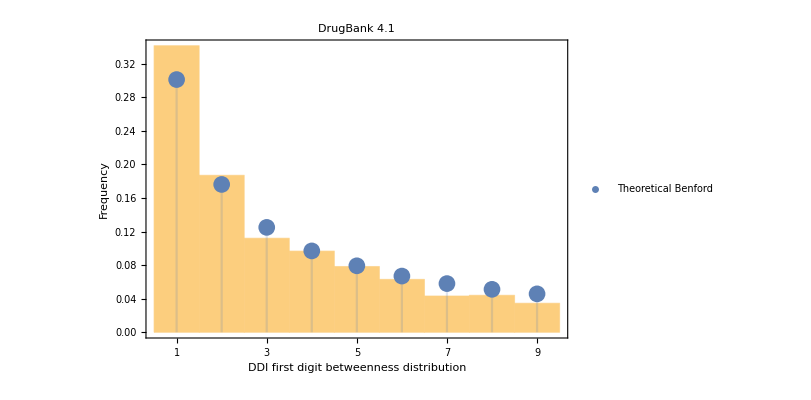

```mathematica
(*Show[Histogram[firstBet,"Sturges", "Probability", Frame ->True, FrameLabel->{Style["DDI betweenness first digit",14],Style["Frequency", 14]}, Ticks->{{1,2,3,4,5,6,7,8,9},{0.00, 0.05, 0.10, 0.15, 0.20, 0.25, 0.30, 0.35}}], DiscretePlot[{Table[PDF[BenfordDistribution[10],x]]}, {x, 1, 9},PlotLegends->Placed[{"Theoretical Benford"}, {0.5,0.9}], PlotMarkers->Style["•", FontSize -> 30]]]*)

Show[Histogram[firstBet,"Sturges", "Probability", Frame ->True, ImageSize->600,AspectRatio->1/1.5,  FrameLabel->{Style["DDI first digit betweenness distribution",16, Black],Style["Frequency", 16, Black]},  FrameStyle->Directive[14,Black],FrameTicks->{{Automatic,Automatic},{{{1,"1"},{2,"2"},{3,"3"}, {4,"4"},{5,"5"},{6,"6"}, {7,"7"},{8,"8"},{9,"9"}},{}}}],DiscretePlot[{Table[PDF[BenfordDistribution[10],x]]}, {x, 1, 9},PlotLegends->Placed[{Style["Theoretical Benford",16]}, {0.5,0.9}],PlotStyle->{AbsolutePointSize[12]}], PlotLabel->Style["DrugBank 4.1",Black,16]]
```

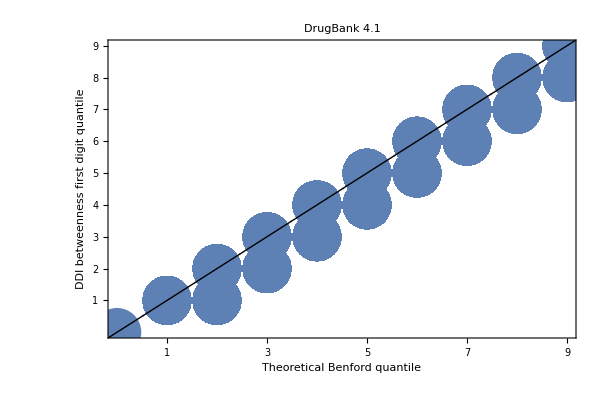

```mathematica
(*Show[QuantilePlot[firstBet,BenfordDistribution[10], PlotMarkers->Style["•", FontSize -> 38]],RotateLabel->True, Frame->True,FrameLabel->{Style["Theoretical Benford quantile",14],Style["DDI betweenness first digit quantile",14]}]*)

Show[QuantilePlot[firstBet,BenfordDistribution[10], ImageSize->600,AspectRatio->1/1.5, PlotMarkers->Style["•", FontSize -> 50]],TicksStyle -> Directive[14,Black], RotateLabel->True, Frame->True, FrameStyle->Directive[14,Black],FrameTicks->{{{1,2,3,4,5,6,7,8,9},None},{{1,2,3,4,5,6,7,8,9},None}},FrameLabel->{Style["Theoretical Benford quantile",Black, 16],Style["DDI betweenness first digit quantile",Black,16]}, PlotLabel->Style["DrugBank 4.1",Black,16]]
```

```mathematica
PearsonChiSquareTest[firstBet,BenfordDistribution[10],"TestConclusion"]
WatsonUSquareTest[firstBet,BenfordDistribution[10],"TestConclusion"]
chisqBet = PearsonChiSquareTest[firstBet,BenfordDistribution[10]]
wuBet = WatsonUSquareTest[firstBet,BenfordDistribution[10]]
```

The null hypothesis that the data is distributed according to the BenfordDistribution[10] is rejected at the 5 percent level based on the Pearson χ^2 test.

WatsonUSquareTest::dscrt: The p-value returned by the WatsonUSquare test may not reflect the true size of the test for discrete test distributions.

WatsonUSquareTest::ties: Ties exist in the data and will be ignored for the WatsonUSquare test, which assumes unique values.

WatsonUSquareTest::dscrt: The p-value returned by the WatsonUSquare test may not reflect the true size of the test for discrete test distributions.

WatsonUSquareTest::ties: Ties exist in the data and will be ignored for the WatsonUSquare test, which assumes unique values.

The null hypothesis that the data is distributed according to the BenfordDistribution[10] is rejected at the 5 percent level based on the Watson U^2 test.

5.69279×10^-9

WatsonUSquareTest::dscrt: The p-value returned by the WatsonUSquare test may not reflect the true size of the test for discrete test distributions.

WatsonUSquareTest::ties: Ties exist in the data and will be ignored for the WatsonUSquare test, which assumes unique values.

8.61959×10^-7

```mathematica
NumberForm[wuBet,16]
```

8.61959187347593×10^-7

```mathematica
numberBfT = Length[firstBet]
bfT =Sort[Tally[firstBet]]


hist =HistogramList[dataDDIdeg,{2}]
```

975

{{1,306},{2,201},{3,127},{4,78},{5,72},{6,54},{7,60},{8,43},{9,34}}

{{},{}}

```mathematica
values = Part[hist,1]
```

{0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60,62,64,66,68,70,72,74,76,78,80,82,84,86,88,90,92,94,96,98,100,102,104,106,108,110,112,114,116,118,120,122,124,126,128,130,132,134,136,138,140,142,144,146,148,150,152,154,156,158,160,162,164,166,168,170,172,174,176,178,180,182,184,186,188,190,192,194,196,198,200,202,204,206,208,210,212,214,216,218,220,222,224,226,228,230,232,234,236,238,240,242,244,246,248,250,252}

```mathematica
{0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5,10.5,11.5,12.5,13.5,14.5,15.5,16.5,17.5,18.5,19.5,20.5,21.5,22.5,23.5,24.5,25.5,26.5,27.5,28.5,29.5,30.5,31.5,32.5,33.5,34.5,35.5,36.5,37.5,38.5,39.5,40.5,41.5,42.5,43.5,44.5,45.5,46.5,47.5,48.5,49.5,50.5,51.5,52.5,53.5,54.5,55.5,56.5,57.5,58.5,59.5,60.5,61.5,62.5,63.5,64.5,65.5,66.5,67.5,68.5,69.5,70.5,71.5,72.5,73.5,74.5,75.5,76.5,77.5,78.5,79.5,80.5,81.5,82.5,83.5,84.5,85.5,86.5,87.5,88.5,89.5,90.5,91.5,92.5,93.5,94.5,95.5,96.5,97.5,98.5,99.5,100.5,101.5,102.5,103.5,104.5,105.5,106.5,107.5,108.5,109.5,110.5,111.5,112.5,113.5,114.5,115.5,116.5,117.5,118.5,119.5,120.5,121.5,122.5,123.5,124.5,125.5,126.5,127.5,128.5,129.5,130.5,131.5,132.5,133.5,134.5,135.5,136.5,137.5,138.5,139.5,140.5,141.5,142.5,143.5,144.5,145.5,146.5,147.5,148.5,149.5,150.5,151.5,152.5,153.5,154.5,155.5,156.5,157.5,158.5,159.5,160.5,161.5,162.5,163.5,164.5,165.5,166.5,167.5,168.5,169.5,170.5,171.5,172.5,173.5,174.5,175.5,176.5,177.5,178.5,179.5,180.5,181.5,182.5,183.5,184.5,185.5,186.5,187.5,188.5,189.5,190.5,191.5,192.5,193.5,194.5,195.5,196.5,197.5,198.5,199.5,200.5,201.5,202.5,203.5,204.5,205.5,206.5,207.5,208.5,209.5,210.5,211.5,212.5,213.5,214.5,215.5,216.5,217.5,218.5,219.5,220.5,221.5,222.5,223.5,224.5,225.5,226.5,227.5,228.5,229.5,230.5,231.5,232.5,233.5,234.5,235.5,236.5,237.5,238.5,239.5,240.5,241.5,242.5,243.5,244.5,245.5,246.5,247.5,248.5,249.5,250.5}
```

{0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5,10.5,11.5,12.5,13.5,14.5,15.5,16.5,17.5,18.5,19.5,20.5,21.5,22.5,23.5,24.5,25.5,26.5,27.5,28.5,29.5,30.5,31.5,32.5,33.5,34.5,35.5,36.5,37.5,38.5,39.5,40.5,41.5,42.5,43.5,44.5,45.5,46.5,47.5,48.5,49.5,50.5,51.5,52.5,53.5,54.5,55.5,56.5,57.5,58.5,59.5,60.5,61.5,62.5,63.5,64.5,65.5,66.5,67.5,68.5,69.5,70.5,71.5,72.5,73.5,74.5,75.5,76.5,77.5,78.5,79.5,80.5,81.5,82.5,83.5,84.5,85.5,86.5,87.5,88.5,89.5,90.5,91.5,92.5,93.5,94.5,95.5,96.5,97.5,98.5,99.5,100.5,101.5,102.5,103.5,104.5,105.5,106.5,107.5,108.5,109.5,110.5,111.5,112.5,113.5,114.5,115.5,116.5,117.5,118.5,119.5,120.5,121.5,122.5,123.5,124.5,125.5,126.5,127.5,128.5,129.5,130.5,131.5,132.5,133.5,134.5,135.5,136.5,137.5,138.5,139.5,140.5,141.5,142.5,143.5,144.5,145.5,146.5,147.5,148.5,149.5,150.5,151.5,152.5,153.5,154.5,155.5,156.5,157.5,158.5,159.5,160.5,161.5,162.5,163.5,164.5,165.5,166.5,167.5,168.5,169.5,170.5,171.5,172.5,173.5,174.5,175.5,176.5,177.5,178.5,179.5,180.5,181.5,182.5,183.5,184.5,185.5,186.5,187.5,188.5,189.5,190.5,191.5,192.5,193.5,194.5,195.5,196.5,197.5,198.5,199.5,200.5,201.5,202.5,203.5,204.5,205.5,206.5,207.5,208.5,209.5,210.5,211.5,212.5,213.5,214.5,215.5,216.5,217.5,218.5,219.5,220.5,221.5,222.5,223.5,224.5,225.5,226.5,227.5,228.5,229.5,230.5,231.5,232.5,233.5,234.5,235.5,236.5,237.5,238.5,239.5,240.5,241.5,242.5,243.5,244.5,245.5,246.5,247.5,248.5,249.5,250.5}

```mathematica
frec =Part[hist, 2]
```

{136,149,121,76,84,73,46,44,34,36,42,25,17,22,27,16,10,18,12,18,6,9,8,8,12,4,5,1,6,5,9,3,6,3,2,3,7,4,4,6,3,0,4,3,1,1,4,0,3,5,1,0,0,1,0,1,1,3,1,1,0,1,0,1,2,0,2,0,0,0,0,1,0,2,0,1,0,0,1,0,1,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}

```mathematica
valuesclear =  Delete[values, 1]
```

{2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60,62,64,66,68,70,72,74,76,78,80,82,84,86,88,90,92,94,96,98,100,102,104,106,108,110,112,114,116,118,120,122,124,126,128,130,132,134,136,138,140,142,144,146,148,150,152,154,156,158,160,162,164,166,168,170,172,174,176,178,180,182,184,186,188,190,192,194,196,198,200,202,204,206,208,210,212,214,216,218,220,222,224,226,228,230,232,234,236,238,240,242,244,246,248,250,252}

```mathematica
degreePairs = Transpose[{valuesclear,frec}]
```

{{2,136},{4,149},{6,121},{8,76},{10,84},{12,73},{14,46},{16,44},{18,34},{20,36},{22,42},{24,25},{26,17},{28,22},{30,27},{32,16},{34,10},{36,18},{38,12},{40,18},{42,6},{44,9},{46,8},{48,8},{50,12},{52,4},{54,5},{56,1},{58,6},{60,5},{62,9},{64,3},{66,6},{68,3},{70,2},{72,3},{74,7},{76,4},{78,4},{80,6},{82,3},{84,0},{86,4},{88,3},{90,1},{92,1},{94,4},{96,0},{98,3},{100,5},{102,1},{104,0},{106,0},{108,1},{110,0},{112,1},{114,1},{116,3},{118,1},{120,1},{122,0},{124,1},{126,0},{128,1},{130,2},{132,0},{134,2},{136,0},{138,0},{140,0},{142,0},{144,1},{146,0},{148,2},{150,0},{152,1},{154,0},{156,0},{158,1},{160,0},{162,1},{164,0},{166,0},{168,0},{170,0},{172,0},{174,0},{176,1},{178,0},{180,0},{182,1},{184,0},{186,0},{188,0},{190,0},{192,0},{194,0},{196,0},{198,0},{200,2},{202,0},{204,0},{206,0},{208,0},{210,0},{212,0},{214,0},{216,0},{218,0},{220,0},{222,0},{224,0},{226,0},{228,0},{230,0},{232,0},{234,0},{236,0},{238,0},{240,0},{242,0},{244,0},{246,0},{248,0},{250,0},{252,1}}

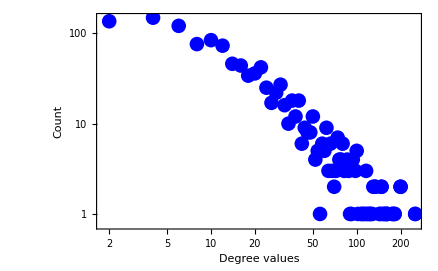

```mathematica
ListLogLogPlot[degreePairs, PlotMarkers->{●,15},PlotStyle->Blue, RotateLabel->True, Frame->True,FrameLabel->{Style["Degree values",16],Style["Count",16]}]
```

```mathematica
histBet =HistogramList[dataDDIbet,{200}]
```

{{0,200,400,600,800,1000,1200,1400,1600,1800,2000,2200,2400,2600,2800,3000,3200,3400,3600,3800,4000,4200,4400,4600,4800,5000,5200,5400,5600,5800,6000,6200,6400,6600,6800,7000,7200,7400,7600,7800,8000,8200,8400,8600,8800,9000,9200,9400,9600,9800,10000,10200,10400,10600,10800,11000,11200,11400,11600,11800,12000,12200,12400,12600,12800,13000,13200,13400,13600,13800,14000,14200,14400,14600,14800,15000,15200,15400,15600,15800,16000,16200,16400,16600,16800,17000,17200,17400,17600,17800,18000,18200,18400,18600,18800,19000,19200,19400,19600,19800,20000,20200,20400,20600,20800,21000,21200,21400,21600,21800,22000,22200,22400,22600,22800,23000,23200,23400,23600,23800,24000,24200,24400,24600,24800,25000,25200,25400,25600,25800,26000,26200,26400,26600,26800,27000,27200,27400,27600,27800,28000,28200,28400,28600,28800,29000,29200,29400,29600,29800,30000,30200,30400,30600,30800,31000,31200,31400,31600,31800,32000,32200,32400,32600,32800,33000,33200,33400,33600,33800,34000,34200,34400,34600,34800,35000,35200,35400,35600,35800,36000,36200,36400,36600,36800,37000,37200,37400,37600,37800,38000,38200,38400,38600,38800,39000,39200,39400,39600,39800,40000,40200,40400,40600,40800,41000,41200,41400,41600,41800,42000,42200,42400,42600,42800,43000,43200,43400,43600,43800,44000,44200,44400,44600,44800,45000,45200,45400,45600,45800,46000,46200,46400,46600,46800,47000,47200,47400,47600},{691,105,47,50,24,23,27,21,14,12,9,17,12,11,12,7,5,3,2,3,4,2,3,1,1,4,1,1,2,3,1,1,0,3,2,0,1,5,2,2,0,2,1,0,3,0,0,2,1,0,0,1,0,0,0,1,0,2,0,0,0,0,0,1,0,0,2,0,0,0,0,0,0,1,0,1,0,1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
valuesBet = Part[histBet,1]
```

{0,200,400,600,800,1000,1200,1400,1600,1800,2000,2200,2400,2600,2800,3000,3200,3400,3600,3800,4000,4200,4400,4600,4800,5000,5200,5400,5600,5800,6000,6200,6400,6600,6800,7000,7200,7400,7600,7800,8000,8200,8400,8600,8800,9000,9200,9400,9600,9800,10000,10200,10400,10600,10800,11000,11200,11400,11600,11800,12000,12200,12400,12600,12800,13000,13200,13400,13600,13800,14000,14200,14400,14600,14800,15000,15200,15400,15600,15800,16000,16200,16400,16600,16800,17000,17200,17400,17600,17800,18000,18200,18400,18600,18800,19000,19200,19400,19600,19800,20000,20200,20400,20600,20800,21000,21200,21400,21600,21800,22000,22200,22400,22600,22800,23000,23200,23400,23600,23800,24000,24200,24400,24600,24800,25000,25200,25400,25600,25800,26000,26200,26400,26600,26800,27000,27200,27400,27600,27800,28000,28200,28400,28600,28800,29000,29200,29400,29600,29800,30000,30200,30400,30600,30800,31000,31200,31400,31600,31800,32000,32200,32400,32600,32800,33000,33200,33400,33600,33800,34000,34200,34400,34600,34800,35000,35200,35400,35600,35800,36000,36200,36400,36600,36800,37000,37200,37400,37600,37800,38000,38200,38400,38600,38800,39000,39200,39400,39600,39800,40000,40200,40400,40600,40800,41000,41200,41400,41600,41800,42000,42200,42400,42600,42800,43000,43200,43400,43600,43800,44000,44200,44400,44600,44800,45000,45200,45400,45600,45800,46000,46200,46400,46600,46800,47000,47200,47400,47600}

```mathematica
frecBet =Part[histBet, 2]
```

{691,105,47,50,24,23,27,21,14,12,9,17,12,11,12,7,5,3,2,3,4,2,3,1,1,4,1,1,2,3,1,1,0,3,2,0,1,5,2,2,0,2,1,0,3,0,0,2,1,0,0,1,0,0,0,1,0,2,0,0,0,0,0,1,0,0,2,0,0,0,0,0,0,1,0,1,0,1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}

```mathematica
valuesclearBet =  Delete[valuesBet, 1]
```

{200,400,600,800,1000,1200,1400,1600,1800,2000,2200,2400,2600,2800,3000,3200,3400,3600,3800,4000,4200,4400,4600,4800,5000,5200,5400,5600,5800,6000,6200,6400,6600,6800,7000,7200,7400,7600,7800,8000,8200,8400,8600,8800,9000,9200,9400,9600,9800,10000,10200,10400,10600,10800,11000,11200,11400,11600,11800,12000,12200,12400,12600,12800,13000,13200,13400,13600,13800,14000,14200,14400,14600,14800,15000,15200,15400,15600,15800,16000,16200,16400,16600,16800,17000,17200,17400,17600,17800,18000,18200,18400,18600,18800,19000,19200,19400,19600,19800,20000,20200,20400,20600,20800,21000,21200,21400,21600,21800,22000,22200,22400,22600,22800,23000,23200,23400,23600,23800,24000,24200,24400,24600,24800,25000,25200,25400,25600,25800,26000,26200,26400,26600,26800,27000,27200,27400,27600,27800,28000,28200,28400,28600,28800,29000,29200,29400,29600,29800,30000,30200,30400,30600,30800,31000,31200,31400,31600,31800,32000,32200,32400,32600,32800,33000,33200,33400,33600,33800,34000,34200,34400,34600,34800,35000,35200,35400,35600,35800,36000,36200,36400,36600,36800,37000,37200,37400,37600,37800,38000,38200,38400,38600,38800,39000,39200,39400,39600,39800,40000,40200,40400,40600,40800,41000,41200,41400,41600,41800,42000,42200,42400,42600,42800,43000,43200,43400,43600,43800,44000,44200,44400,44600,44800,45000,45200,45400,45600,45800,46000,46200,46400,46600,46800,47000,47200,47400,47600}

```mathematica
degreePairsBet = Transpose[{valuesclearBet,frecBet}]
```

{{200,691},{400,105},{600,47},{800,50},{1000,24},{1200,23},{1400,27},{1600,21},{1800,14},{2000,12},{2200,9},{2400,17},{2600,12},{2800,11},{3000,12},{3200,7},{3400,5},{3600,3},{3800,2},{4000,3},{4200,4},{4400,2},{4600,3},{4800,1},{5000,1},{5200,4},{5400,1},{5600,1},{5800,2},{6000,3},{6200,1},{6400,1},{6600,0},{6800,3},{7000,2},{7200,0},{7400,1},{7600,5},{7800,2},{8000,2},{8200,0},{8400,2},{8600,1},{8800,0},{9000,3},{9200,0},{9400,0},{9600,2},{9800,1},{10000,0},{10200,0},{10400,1},{10600,0},{10800,0},{11000,0},{11200,1},{11400,0},{11600,2},{11800,0},{12000,0},{12200,0},{12400,0},{12600,0},{12800,1},{13000,0},{13200,0},{13400,2},{13600,0},{13800,0},{14000,0},{14200,0},{14400,0},{14600,0},{14800,1},{15000,0},{15200,1},{15400,0},{15600,1},{15800,0},{16000,0},{16200,0},{16400,1},{16600,0},{16800,1},{17000,0},{17200,0},{17400,0},{17600,0},{17800,0},{18000,0},{18200,0},{18400,0},{18600,0},{18800,0},{19000,0},{19200,1},{19400,0},{19600,0},{19800,0},{20000,0},{20200,0},{20400,0},{20600,0},{20800,0},{21000,0},{21200,0},{21400,1},{21600,1},{21800,0},{22000,0},{22200,1},{22400,0},{22600,0},{22800,0},{23000,0},{23200,0},{23400,0},{23600,0},{23800,0},{24000,0},{24200,0},{24400,0},{24600,0},{24800,0},{25000,0},{25200,0},{25400,0},{25600,0},{25800,0},{26000,0},{26200,0},{26400,0},{26600,0},{26800,0},{27000,0},{27200,0},{27400,0},{27600,0},{27800,1},{28000,0},{28200,0},{28400,0},{28600,0},{28800,0},{29000,0},{29200,0},{29400,0},{29600,0},{29800,0},{30000,0},{30200,0},{30400,0},{30600,1},{30800,0},{31000,0},{31200,0},{31400,0},{31600,0},{31800,0},{32000,0},{32200,0},{32400,0},{32600,0},{32800,0},{33000,0},{33200,0},{33400,1},{33600,0},{33800,0},{34000,0},{34200,1},{34400,0},{34600,0},{34800,0},{35000,1},{35200,0},{35400,0},{35600,0},{35800,0},{36000,0},{36200,0},{36400,0},{36600,0},{36800,0},{37000,0},{37200,1},{37400,0},{37600,1},{37800,0},{38000,0},{38200,0},{38400,0},{38600,0},{38800,0},{39000,0},{39200,0},{39400,0},{39600,0},{39800,0},{40000,0},{40200,0},{40400,0},{40600,0},{40800,0},{41000,0},{41200,0},{41400,0},{41600,0},{41800,0},{42000,0},{42200,0},{42400,0},{42600,0},{42800,0},{43000,0},{43200,0},{43400,0},{43600,0},{43800,0},{44000,0},{44200,0},{44400,0},{44600,0},{44800,0},{45000,0},{45200,0},{45400,0},{45600,0},{45800,0},{46000,0},{46200,0},{46400,0},{46600,0},{46800,0},{47000,0},{47200,0},{47400,0},{47600,1}}

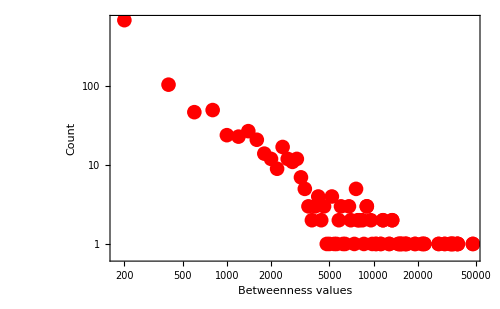

```mathematica
ListLogLogPlot[degreePairsBet, PlotMarkers->{●,15},PlotStyle->Red, RotateLabel->True, Frame->True,FrameLabel->{Style["Betweenness values",16],Style["Count",16]}]
```

```mathematica
dataDDIclo=First[Transpose[Import["C:\Hyperion\4.1\ddi-closeness41.csv"]]]
```

{0.300578,0.414493,0.386888,0.282784,0.392005,0.363529,0.282784,0.315767,0.335955,0.27472,0.368747,0.297101,0.42206,0.391341,0.416284,0.22887,0.414791,0.30615,0.416734,0.320494,0.296949,0.288933,0.344464,0.347362,0.264536,0.304056,0.305422,0.371114,0.33334,0.370164,0.333243,0.42206,0.320316,0.296949,0.281339,0.298251,0.354065,0.282992,0.322641,0.274199,0.241795,0.319255,0.307126,0.296949,0.263391,0.358012,0.263391,0.241896,0.319431,0.257122,0.280724,0.280724,0.342119,0.350203,0.373151,0.343543,0.363414,0.410228,0.368277,0.454232,0.361596,0.387277,0.414493,0.381903,0.354934,0.371353,0.333532,0.34978,0.330859,0.392804,0.364101,0.345597,0.314564,0.30819,0.357238,0.394143,0.382789,0.412717,0.363186,0.397395,0.367808,0.380145,0.371353,0.33286,0.334207,0.368982,0.364561,0.282923,0.358345,0.296188,0.309676,0.349146,0.23573,0.373875,0.3344,0.344464,0.370164,0.355262,0.353415,0.4139,0.360244,0.235394,0.264415,0.303099,0.303099,0.303099,0.363758,0.326283,0.305826,0.394547,0.283756,0.459285,0.346011,0.396305,0.338018,0.30951,0.401536,0.255983,0.255983,0.255983,0.281339,0.300656,0.28313,0.259663,0.351161,0.344978,0.282923,0.328229,0.281339,0.281888,0.281339,0.465013,0.304056,0.349462,0.282784,0.332095,0.366177,0.281339,0.35768,0.332095,0.303657,0.399869,0.370282,0.305745,0.381777,0.297484,0.299798,0.281339,0.398353,0.381022,0.324999,0.281339,0.329351,0.373875,0.299177,0.373392,0.358456,0.387666,0.384699,0.290239,0.405053,0.393205,0.419761,0.396985,0.332095,0.396985,0.353523,0.281339,0.400284,0.392138,0.373754,0.357901,0.302941,0.281888,0.411396,0.462039,0.398903,0.281339,0.281339,0.352016,0.396713,0.281339,0.310758,0.348935,0.358345,0.282025,0.350522,0.285085,0.394951,0.340407,0.327114,0.290458,0.382662,0.375698,0.281339,0.367341,0.292368,0.281339,0.316979,0.37243,0.419,0.367808,0.397531,0.281339,0.296872,0.373754,0.348304,0.378899,0.407768,0.341614,0.376677,0.389889,0.438884,0.349885,0.358679,0.348094,0.347885,0.350628,0.234107,0.305988,0.263391,0.251145,0.33576,0.293854,0.347154,0.44755,0.427049,0.328509,0.441398,0.362162,0.422214,0.427681,0.398079,0.421291,0.421444,0.467835,0.366293,0.417186,0.415238,0.401675,0.317066,0.420524,0.371592,0.417035,0.368042,0.409501,0.366177,0.345287,0.369927,0.370401,0.375698,0.35879,0.407912,0.441061,0.346945,0.374723,0.406334,0.413751,0.410957,0.396169,0.446513,0.378403,0.479478,0.422677,0.408056,0.379895,0.388709,0.376554,0.421598,0.409211,0.337722,0.388579,0.389626,0.453164,0.332477,0.341009,0.388579,0.421291,0.419304,0.402935,0.373151,0.378279,0.419761,0.376677,0.317066,0.396169,0.384188,0.424384,0.335857,0.380771,0.371831,0.400284,0.33615,0.376432,0.42911,0.376923,0.337229,0.464826,0.41794,0.375698,0.352661,0.469355,0.458739,0.412865,0.413455,0.432805,0.395898,0.339308,0.370045,0.341513,0.396713,0.411249,0.433616,0.339009,0.414493,0.386759,0.449814,0.436564,0.415536,0.333243,0.44548,0.410228,0.356137,0.402795,0.416134,0.455844,0.393606,0.419304,0.40084,0.425477,0.416434,0.366293,0.366293,0.366293,0.366293,0.409066,0.373875,0.404628,0.371472,0.363072,0.363758,0.337032,0.328042,0.339607,0.32005,0.32005,0.367574,0.392271,0.399869,0.389626,0.355808,0.317066,0.266549,0.379272,0.266549,0.282853,0.422986,0.408344,0.456745,0.422986,0.420677,0.402935,0.422522,0.400146,0.296949,0.356467,0.261899,0.335857,0.354065,0.348409,0.319962,0.322551,0.284174,0.360131,0.418697,0.381651,0.41316,0.382535,0.29941,0.230237,0.338513,0.301754,0.373151,0.311093,0.391209,0.273291,0.334885,0.291704,0.326652,0.312523,0.324361,0.297254,0.371831,0.350735,0.273291,0.361257,0.273356,0.279908,0.290458,0.397122,0.377785,0.434595,0.33537,0.369336,0.374723,0.432481,0.33411,0.302623,0.387147,0.425947,0.41794,0.355699,0.391739,0.415686,0.407624,0.390548,0.382156,0.424228,0.353523,0.352123,0.431673,0.426262,0.371711,0.343339,0.423451,0.417487,0.342119,0.340106,0.359348,0.375576,0.363643,0.425321,0.387018,0.413751,0.373392,0.391209,0.381525,0.373875,0.416584,0.340106,0.355589,0.356907,0.371472,0.352661,0.357901,0.430068,0.422677,0.426734,0.376554,0.38027,0.342119,0.423141,0.396441,0.379895,0.44634,0.367691,0.368512,0.367691,0.380897,0.404203,0.374359,0.330009,0.350416,0.324634,0.324634,0.341614,0.367574,0.295205,0.327763,0.301204,0.352338,0.397531,0.355808,0.417336,0.353091,0.357238,0.376187,0.344567,0.376554,0.307616,0.314649,0.395491,0.317327,0.364561,0.294228,0.312946,0.353632,0.382535,0.350097,0.352768,0.354825,0.348409,0.348409,0.346529,0.316458,0.335468,0.336053,0.33576,0.348409,0.338513,0.335662,0.335273,0.338315,0.33664,0.316198,0.319962,0.325365,0.328136,0.328136,0.319962,0.32005,0.343747,0.343645,0.330859,0.414493,0.382156,0.402094,0.355699,0.348935,0.370638,0.367341,0.376554,0.395762,0.377415,0.439552,0.421598,0.359907,0.335468,0.406763,0.420831,0.385212,0.356797,0.454947,0.388971,0.353199,0.393874,0.408633,0.362844,0.356467,0.356797,0.413603,0.403639,0.399455,0.360918,0.379148,0.376309,0.349674,0.371592,0.378279,0.388709,0.375454,0.356137,0.262971,0.393472,0.379895,0.390416,0.381903,0.384443,0.367925,0.335468,0.417035,0.382789,0.423451,0.400979,0.382789,0.383042,0.342221,0.379646,0.387147,0.398628,0.395762,0.373633,0.40662,0.370995,0.399041,0.360581,0.362617,0.336836,0.378279,0.382156,0.323816,0.371353,0.381399,0.365598,0.388057,0.400423,0.38002,0.37195,0.379397,0.393338,0.405053,0.345907,0.386113,0.384699,0.401815,0.326652,0.37303,0.368394,0.369809,0.318551,0.352016,0.306474,0.30615,0.387018,0.355043,0.331049,0.350735,0.350735,0.349357,0.26178,0.352016,0.352016,0.355262,0.340507,0.337919,0.335955,0.388709,0.347154,0.363643,0.333724,0.321922,0.333147,0.322281,0.335662,0.352123,0.334303,0.329821,0.331618,0.404486,0.319079,0.370876,0.293854,0.370401,0.387537,0.360693,0.327949,0.331238,0.319343,0.316805,0.319696,0.331143,0.319255,0.380395,0.331238,0.342221,0.387018,0.331143,0.322461,0.270478,0.301754,0.335468,0.333147,0.398216,0.328882,0.396033,0.319343,0.333147,0.319873,0.329539,0.331143,0.331238,0.331238,0.319343,0.390284,0.38002,0.316805,0.328882,0.333628,0.316718,0.319255,0.316718,0.319343,0.331238,0.373633,0.342119,0.374845,0.319343,0.337131,0.319343,0.316805,0.37279,0.327114,0.319255,0.328882,0.34904,0.347049,0.342221,0.339906,0.3182,0.379521,0.3768,0.356907,0.357127,0.37052,0.345081,0.340206,0.352768,0.359571,0.34904,0.352553,0.323001,0.384443,0.380521,0.382915,0.33576,0.381651,0.346529,0.364906,0.331333,0.374966,0.376187,0.371353,0.246434,0.327392,0.292368,0.33782,0.339208,0.350203,0.365483,0.298868,0.299643,0.342322,0.2832,0.328322,0.301204,0.328415,0.329821,0.343339,0.396577,0.344567,0.344567,0.327856,0.369809,0.368512,0.360019,0.344567,0.335662,0.352338,0.347049,0.298174,0.364331,0.364101,0.334303,0.29596,0.391341,0.314393,0.259081,0.382535,0.388318,0.335955,0.359124,0.354499,0.359013,0.310508,0.394681,0.360581,0.339009,0.377908,0.37303,0.356137,0.35374,0.354282,0.310258,0.279232,0.353091,0.331809,0.375942,0.37279,0.349674,0.338117,0.319608,0.340006,0.37207,0.362958,0.368747,0.363529,0.37267,0.344464,0.322371,0.359013,0.343952,0.350097,0.350097,0.350097,0.362389,0.362958,0.367574,0.343441,0.319255,0.331809,0.331809,0.331238,0.327207,0.335176,0.332381,0.33219,0.370757,0.349674,0.338612,0.319255,0.304296,0.329727,0.318815,0.341917,0.317676,0.304296,0.304296,0.319255,0.30778,0.317938,0.304296,0.344156,0.319255,0.304296,0.319255,0.31371,0.303976,0.317938,0.300969,0.319255,0.289512,0.304296,0.32767,0.310258,0.348094,0.329915,0.336444,0.353307,0.323725,0.318288,0.289222,0.293779,0.318815,0.27544,0.275374,0.355589,0.289222,0.27749,0.296112,0.37207,0.332286,0.329821,0.322281,0.300578,0.314564,0.373392,0.33615,0.38203,0.327392,0.327392,0.323092,0.328789,0.322281,0.338513,0.386759,0.316198,0.378527,0.353199,0.316198,0.352661,0.333821,0.333821,0.352231,0.353956,0.334594,0.302941,0.345494,0.254462,0.341715,0.317763,0.308519,0.333628,0.328415,0.296949,0.308355,0.300578,0.296036,0.336444,0.377661,0.273874,0.329257,0.288429,0.344567,0.353523,0.28313,0.295129,0.30302,0.281134,0.308602,0.347676,0.297178,0.321385,0.312017,0.303179,0.3457,0.291704,0.344567,0.344567,0.309179,0.294453,0.351374,0.365598,0.266918,0.327114,0.275966,0.317414,0.348094,0.288789,0.288429,0.329539,0.292738,0.24124,0.325273,0.347467,0.351909,0.319696,0.306881,0.320939,0.374845,0.357459,0.312354,0.292738,0.259081,0.312354,0.311428,0.289295,0.289295,0.289295,0.354608,0.341614,0.341513,0.341513,0.323272,0.341009,0.342018,0.339208,0.323272,0.312017,0.341311,0.292738,0.329821,0.341513,0.328322,0.326283,0.318376,0.350522,0.323272,0.321653,0.321206,0.338117,0.341816,0.363758,0.302941,0.306069,0.348304,0.292738,0.292738,0.29528,0.329821,0.329445,0.352768,0.292738,0.292738,0.29528,0.292738,0.292738,0.300734,0.29756,0.29756,0.312354,0.29756,0.325548,0.29756,0.29756,0.329351,0.325548,0.377538,0.29756,0.296264,0.290093,0.299954,0.290093,0.308849,0.290093,0.268655,0.268655,0.293929,0.312692,0.312692,0.301991,0.32656,0.312692,0.334982,0.344464,0.282853,0.34978,0.301204,0.34978,0.311093,0.305583,0.344054,0.301204,0.361596,0.327392,0.325273,0.301204,0.327578,0.314222,0.374359,0.325273,0.351054,0.327392,0.332095,0.305583,0.301204,0.353848,0.301204,0.309593,0.302386,0.28052,0.325732,0.333724,0.287425,0.280656,0.305745,0.353523,0.355808,0.349462,0.35374,0.254462,0.358456,0.25943,0.301204,0.329633,0.330386,0.292442,0.289512,0.280112,0.29002,0.289078,0.280112,0.289078,0.289078,0.289078,0.280112,0.289078,0.289078,0.246434,0.259663,0.26618,0.286712,0.324725,0.333917,0.285861,0.309759,0.296264,0.296264,0.306963,0.354065,0.344567,0.327299,0.280248,0.218736,0.280248,0.280248,0.287782,0.327207,0.325365,0.304457,0.304457,0.304457,0.304457,0.303179,0.287997,0.287997,0.224645,0.254462,0.334691,0.337919,0.327763,0.329351,0.349146,0.268655,0.294003,0.313966,0.302544,0.314393,0.218985,0.000857633,0.000857633,0.254462,0.284804,0.284664,0.291483,0.284664,0.287854,0.284664,0.284664,0.284664,0.284804,0.30819,0.298251,0.314393,0.314393,0.329915,0.314393,0.283478,0.288789,0.283617,0.254462,0.298097,0.27957,0.228915,0.26113,0.271622,0.242149,0.292072,0.263391,0.283061,0.26853,0.254462,0.276098,0.2162,0.297178,0.31568,0.232319,0.228915,0.27284,0.286712,0.246539,0.250764,0.294003,0.00114351,0.00171527,0.00114351,0.271494,0.287854,0.287568,0.28086,0.333821,0.333821,0.319079,0.254462,0.254462,0.254462,0.254462,0.314136,0.251145,0.291116,0.302149,0.297254,0.320139,0.256609,0.254686,0.295129,0.310758,0.27143,0.27623,0.262374,0.262374,0.262374,0.266364,0.27623,0.297254,0.276428,0.276428,0.231297}

```mathematica
histClo =HistogramList[dataDDIclo,{0.02}]
```

{{0.,0.02,0.04,0.06,0.08,0.1,0.12,0.14,0.16,0.18,0.2,0.22,0.24,0.26,0.28,0.3,0.32,0.34,0.36,0.38,0.4,0.42,0.44,0.46,0.48},{5,0,0,0,0,0,0,0,0,0,3,10,31,45,154,154,189,188,154,106,70,38,14,6}}

```mathematica
valuesClo = Part[histClo,1]
```

{0.,0.02,0.04,0.06,0.08,0.1,0.12,0.14,0.16,0.18,0.2,0.22,0.24,0.26,0.28,0.3,0.32,0.34,0.36,0.38,0.4,0.42,0.44,0.46,0.48}

```mathematica
frecClo =Part[histClo, 2]
```

{5,0,0,0,0,0,0,0,0,0,3,10,31,45,154,154,189,188,154,106,70,38,14,6}

```mathematica
valuesclearClo =  Delete[valuesClo, 1]
```

{0.02,0.04,0.06,0.08,0.1,0.12,0.14,0.16,0.18,0.2,0.22,0.24,0.26,0.28,0.3,0.32,0.34,0.36,0.38,0.4,0.42,0.44,0.46,0.48}

```mathematica
cloPairs = Transpose[{valuesclearClo,frecClo}]
```

{{0.02,5},{0.04,0},{0.06,0},{0.08,0},{0.1,0},{0.12,0},{0.14,0},{0.16,0},{0.18,0},{0.2,0},{0.22,3},{0.24,10},{0.26,31},{0.28,45},{0.3,154},{0.32,154},{0.34,189},{0.36,188},{0.38,154},{0.4,106},{0.42,70},{0.44,38},{0.46,14},{0.48,6}}

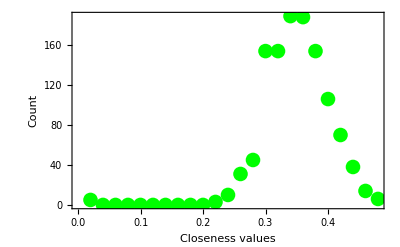

```mathematica
ListPlot[cloPairs, PlotMarkers->{●,15},PlotStyle->Green, RotateLabel->True, Frame->True,FrameLabel->{Style["Closeness values",16],Style["Count",16]}]
```

```mathematica
dataDDIeig=First[Transpose[Import["C:\Hyperion\4.1\ddi-eigenvector41.csv"]]]
```

{0.00104567,0.0370358,0.021487,0.00057406,0.0243608,0.00776841,0.00057406,0.00150593,0.00769038,0.000352545,0.0177185,0.00322317,0.0566481,0.0276723,0.0486933,0.0000575946,0.0473309,0.00118894,0.0379334,0.00712482,0.00322215,0.000548621,0.00382187,0.00525617,0.000139302,0.00106164,0.00341503,0.0508405,0.00916328,0.0483753,0.00845205,0.069097,0.0052355,0.00322215,0.000435265,0.000708707,0.00386882,0.000576387,0.00278112,0.000310152,0.0000424929,0.00237815,0.00122635,0.00322215,0.000176453,0.0098771,0.000176453,0.0000796898,0.00445904,0.0000779893,0.000520261,0.000520261,0.00332472,0.00758974,0.0225026,0.0026688,0.0168714,0.058159,0.0182685,0.10499,0.0049618,0.0258906,0.0348466,0.0151623,0.033686,0.00712648,0.00926211,0.00408661,0.00984586,0.0265982,0.016325,0.0135645,0.00714565,0.0031007,0.0108668,0.0347904,0.0270301,0.0504778,0.0135366,0.0423888,0.0182159,0.0248105,0.0200832,0.00946043,0.00996116,0.0145855,0.0166773,0.000584359,0.00754691,0.000774496,0.00153531,0.00592132,0.000085238,0.0163037,0.00715498,0.0086381,0.0152716,0.0110305,0.0124984,0.0375954,0.00981762,0.0000554069,0.000205045,0.00276569,0.00276569,0.00276569,0.0212895,0.00150044,0.00109151,0.0166039,0.000452209,0.095885,0.00459005,0.0194828,0.00245674,0.00132042,0.0340969,0.0000682912,0.0000682912,0.0000682912,0.000435265,0.00106517,0.000623745,0.000167315,0.00936505,0.00371298,0.000584359,0.00241608,0.000435265,0.000606726,0.000435265,0.1031,0.00116508,0.00959717,0.00057406,0.00370287,0.00916202,0.000435265,0.00775994,0.00370287,0.00203918,0.043539,0.00859433,0.0010553,0.0404924,0.00116967,0.00103036,0.000435265,0.0268751,0.0384349,0.00188533,0.000435265,0.0137349,0.00992873,0.00107352,0.0302301,0.00874036,0.0423053,0.0192912,0.000599973,0.0202323,0.0464802,0.0693391,0.0266087,0.00370287,0.0266087,0.00581691,0.000435265,0.0274062,0.0250943,0.016209,0.0106741,0.000696929,0.000606726,0.03422,0.131567,0.0322184,0.000435265,0.000435265,0.00821247,0.0239772,0.000435265,0.00115435,0.00848655,0.00911777,0.000441438,0.00935373,0.000449258,0.0357256,0.0080203,0.00227728,0.000477979,0.0177229,0.0161489,0.000435265,0.0105534,0.000578633,0.000435265,0.00188258,0.0160632,0.043822,0.015447,0.0460315,0.000435265,0.000559613,0.0103487,0.00582823,0.0300587,0.0580368,0.00259994,0.0133485,0.0188047,0.0933513,0.0036015,0.00807269,0.00370631,0.0117765,0.00837351,0.0000202761,0.00113493,0.000176453,0.000117307,0.00656551,0.000677727,0.00564943,0.131656,0.0826283,0.0034524,0.110271,0.0174888,0.0824054,0.0867963,0.054831,0.0467694,0.0460132,0.0966154,0.0192734,0.0370408,0.0252863,0.0361689,0.00184202,0.0559715,0.0104895,0.0402488,0.0224637,0.0278632,0.00920398,0.00837734,0.0208823,0.015831,0.0107108,0.00913685,0.0274148,0.112142,0.00648549,0.0237041,0.0451814,0.0254031,0.0267018,0.0319405,0.0956617,0.0112086,0.193359,0.0184554,0.0257786,0.00979843,0.0179834,0.0222676,0.08232,0.0444637,0.00802234,0.0420536,0.0464385,0.126778,0.00233907,0.00441564,0.0111861,0.070425,0.0801748,0.0173851,0.0151932,0.0110643,0.0470221,0.0183834,0.00184202,0.0168376,0.0122044,0.0470896,0.00331585,0.00521882,0.0222877,0.0575725,0.00502397,0.0232228,0.0871414,0.00692758,0.00373499,0.164764,0.0533894,0.0107108,0.00515935,0.12595,0.128343,0.0254424,0.0428876,0.0973007,0.0502998,0.00781358,0.0154223,0.00465429,0.0531798,0.0358294,0.0883881,0.00422695,0.0739787,0.0191644,0.110274,0.0653642,0.0583069,0.00378011,0.118485,0.0744358,0.00991012,0.0531924,0.0712485,0.0875223,0.0392701,0.0603942,0.0419191,0.0608814,0.031367,0.0192734,0.0192734,0.0192734,0.0192734,0.0363479,0.0224319,0.0534862,0.014202,0.0194119,0.0127855,0.00529993,0.00249486,0.00528123,0.00185601,0.00185601,0.021235,0.0163063,0.0381839,0.0290428,0.00956563,0.00184202,0.000149094,0.0330822,0.000149094,0.00063826,0.0918156,0.081422,0.163428,0.0891974,0.0951604,0.0778403,0.0881686,0.0735811,0.00322215,0.0165034,0.00101883,0.0233439,0.00505378,0.00513957,0.00268651,0.00276856,0.000822354,0.0152381,0.0968955,0.0532212,0.0806884,0.0536229,0.00155116,0.000027712,0.0066936,0.00116183,0.0153782,0.00365034,0.0633915,0.00029557,0.0147714,0.000773613,0.00467281,0.00242218,0.00329306,0.00139781,0.0141199,0.00908818,0.00029557,0.0100601,0.000303216,0.00042784,0.000546999,0.0226546,0.0212492,0.0772196,0.0149695,0.0240237,0.043424,0.0766793,0.00707157,0.00137956,0.0628285,0.0845331,0.0650039,0.0120501,0.077603,0.0638696,0.0480991,0.034704,0.0200159,0.0699372,0.00978575,0.03708,0.103037,0.0871495,0.0328588,0.010428,0.0812728,0.0706687,0.0196431,0.0194948,0.0311256,0.0448508,0.0260779,0.0868846,0.0624965,0.029958,0.014646,0.0631959,0.0273046,0.0367006,0.0711262,0.0194948,0.0286629,0.0266258,0.0135535,0.0257924,0.0232282,0.075689,0.0823783,0.0817774,0.0235538,0.0536583,0.0196431,0.0771421,0.0312777,0.0529674,0.0822024,0.0207633,0.0217919,0.0207633,0.0279325,0.0278587,0.0244068,0.00317539,0.00657141,0.00307801,0.00280961,0.00363701,0.00697189,0.000779616,0.00639803,0.00184075,0.0207584,0.0506369,0.0193175,0.0572166,0.0210201,0.0222057,0.0335927,0.0373801,0.0365649,0.00960495,0.00222151,0.0544113,0.0030915,0.0154919,0.00641794,0.00709024,0.0242293,0.0298088,0.0113472,0.0135056,0.0227227,0.0285046,0.0285046,0.0137986,0.00741845,0.0205418,0.0209791,0.0122212,0.0285046,0.00846135,0.0208335,0.0202439,0.00816966,0.00715777,0.00590435,0.00910935,0.00876825,0.0112864,0.0112864,0.00910935,0.00911511,0.0127169,0.01422,0.00811778,0.0554509,0.0297815,0.0664583,0.0170843,0.0140185,0.0304062,0.0167285,0.0289918,0.0363402,0.0296473,0.0811648,0.0581888,0.0278993,0.012934,0.0583932,0.075363,0.0199049,0.021256,0.119546,0.0297457,0.0122163,0.0431342,0.0499491,0.0254016,0.0205727,0.0162206,0.0470875,0.0395154,0.0430583,0.028659,0.0397741,0.0240734,0.00597029,0.0312647,0.0407046,0.0430607,0.0185373,0.0144798,0.000194163,0.0443425,0.0374167,0.0197405,0.029856,0.0145885,0.0159379,0.0042852,0.0942351,0.0323871,0.0808107,0.053068,0.0323871,0.0273089,0.011675,0.0213485,0.0318024,0.0428999,0.0502065,0.0261551,0.0671467,0.0219749,0.0530525,0.0150726,0.0163493,0.0069109,0.0237215,0.0308723,0.00469843,0.0274973,0.0266793,0.0278388,0.0387532,0.039471,0.0410569,0.0344164,0.0444766,0.0357546,0.0469712,0.0156004,0.0396446,0.0453053,0.0432337,0.00383117,0.01837,0.0109038,0.0312175,0.00578347,0.00901111,0.00341513,0.00207507,0.034269,0.00507137,0.00502516,0.00519326,0.00519953,0.00511322,0.0000906052,0.013352,0.013352,0.00882252,0.00377455,0.00328309,0.00336056,0.0230513,0.0104254,0.0134893,0.0221106,0.0163565,0.0207175,0.016502,0.025591,0.0201831,0.0166925,0.0207511,0.0200498,0.0512881,0.00611868,0.0148614,0.000677727,0.0242339,0.0189209,0.00801979,0.00281005,0.00879038,0.00775086,0.0048626,0.00728194,0.00807914,0.00703962,0.0282149,0.00879038,0.00882392,0.0286704,0.00618423,0.0070599,0.0017724,0.00361316,0.00958507,0.00809942,0.0625681,0.00590212,0.0366331,0.00775086,0.00809942,0.00728426,0.00389531,0.00807914,0.00879038,0.00879038,0.00775086,0.0592957,0.0280601,0.0048626,0.00590212,0.00654611,0.00399842,0.00509838,0.00399842,0.00775086,0.00879038,0.0398128,0.00945996,0.0190863,0.00775086,0.00906634,0.00775086,0.0048626,0.0225686,0.00795585,0.00703962,0.00590212,0.0201509,0.00837542,0.00979874,0.00725064,0.00323961,0.0274505,0.0206839,0.0148472,0.0143594,0.0088119,0.00773366,0.0186515,0.0182265,0.0181358,0.0176854,0.0183553,0.00591471,0.0431136,0.037685,0.0376498,0.0137629,0.0357447,0.014094,0.0128305,0.0122855,0.0331061,0.0322046,0.0297314,0.000145564,0.00814844,0.00166941,0.00852789,0.00960086,0.00970186,0.0218864,0.00142531,0.00289812,0.00653695,0.000480307,0.00866789,0.00184075,0.00519122,0.00227569,0.00378791,0.035663,0.0162907,0.0162907,0.0133361,0.0210361,0.0163187,0.0222052,0.0162907,0.0147338,0.0159013,0.0137317,0.00145145,0.0123521,0.0228253,0.00858525,0.00349687,0.0409332,0.00461344,0.000313807,0.0259713,0.035227,0.00852896,0.019393,0.0167469,0.0180785,0.00795987,0.0335096,0.0207238,0.0146241,0.0346655,0.0306673,0.0135595,0.0148465,0.0210047,0.00333359,0.00267184,0.0137942,0.00700395,0.00951447,0.0142948,0.00831558,0.00394282,0.00493744,0.00849154,0.00938632,0.0115327,0.0140727,0.0187603,0.0181269,0.0067782,0.00344761,0.0125242,0.00480109,0.00872449,0.00872449,0.00872449,0.0115095,0.0115327,0.0161483,0.0109316,0.00328998,0.00700395,0.00700395,0.00693469,0.00375841,0.00715196,0.00341453,0.00318166,0.0219502,0.00790965,0.00598081,0.00353504,0.00238189,0.00386145,0.00280059,0.00943939,0.00258111,0.00238189,0.00238189,0.00353504,0.00193167,0.00274342,0.00238189,0.00540387,0.00353504,0.00238189,0.00353504,0.00266007,0.00198333,0.00274342,0.0018052,0.00353504,0.00157013,0.00238189,0.00352689,0.00387562,0.0134801,0.00292886,0.00802104,0.0119799,0.0050272,0.00241649,0.00195572,0.00204303,0.00601122,0.000944542,0.000897004,0.0123696,0.00195572,0.000547302,0.00183688,0.0164235,0.00665591,0.00288132,0.00262229,0.00104567,0.00204067,0.0122711,0.0085758,0.0119788,0.00662344,0.00662344,0.00643622,0.00845752,0.00596935,0.00949953,0.0129284,0.00590435,0.0104363,0.0138098,0.00590435,0.00875991,0.00656064,0.00656064,0.0106334,0.00971012,0.00716388,0.000984266,0.00768972,0.0000591358,0.00330904,0.00132222,0.00351788,0.00364811,0.00690615,0.00322215,0.0030532,0.00104567,0.00268898,0.011094,0.0234414,0.000418776,0.0066404,0.000854799,0.0045556,0.00493338,0.000972066,0.00143236,0.0012074,0.000555373,0.00184738,0.00532111,0.000783164,0.00325626,0.00274487,0.00195473,0.00484716,0.000991992,0.0045556,0.0045556,0.00193344,0.000991813,0.0118426,0.0117596,0.000276777,0.00199806,0.000950783,0.00380584,0.00855046,0.000726001,0.000702723,0.00893897,0.000661752,0.0000431755,0.0025972,0.00412068,0.00444888,0.00295556,0.00216273,0.00367938,0.0133363,0.0177,0.00217595,0.000661752,0.000313807,0.00217595,0.00281472,0.000859307,0.000859307,0.000859307,0.0153093,0.00869427,0.00253319,0.00253319,0.00365894,0.00384302,0.00502281,0.00309931,0.00365894,0.00166364,0.00251926,0.000661752,0.00227569,0.00253319,0.00217041,0.00235855,0.00197054,0.00293202,0.00365894,0.00210321,0.00179057,0.00358136,0.00261878,0.0105273,0.000920441,0.00102737,0.00356423,0.000661752,0.000661752,0.00081139,0.00227569,0.00216975,0.00693655,0.000661752,0.000661752,0.000872159,0.000661752,0.000661752,0.00106125,0.00124944,0.00124944,0.00178467,0.00124944,0.00518721,0.00124944,0.00124944,0.00626776,0.00518721,0.0213348,0.00124944,0.00103952,0.000783203,0.00175485,0.000783203,0.00131843,0.000783203,0.00366613,0.00366613,0.00518526,0.00127792,0.00127792,0.00085727,0.00390103,0.00127792,0.00410905,0.00600608,0.00063826,0.00823878,0.00184075,0.00823878,0.00261161,0.00209944,0.00430625,0.00184075,0.011389,0.00354951,0.0025972,0.00184075,0.00268204,0.00328221,0.0185872,0.0025972,0.00623702,0.00354951,0.00354985,0.00209944,0.00184075,0.0114443,0.00184075,0.0093867,0.00664026,0.000597152,0.00281256,0.00313341,0.000782943,0.000352819,0.00476009,0.00776785,0.00822823,0.0059897,0.0066826,0.0000591358,0.00695772,0.000092791,0.000863868,0.00614606,0.00641133,0.000671718,0.000656288,0.000476928,0.00130273,0.000536063,0.000476928,0.000536063,0.000536063,0.000536063,0.000476928,0.000536063,0.000536063,0.000145564,0.000167315,0.000422831,0.000567391,0.00428667,0.00665969,0.00111123,0.00170876,0.00103952,0.00103952,0.00321654,0.0115563,0.00711789,0.00425364,0.000223223,3.98921×10^-6,0.000336015,0.000336015,0.00095556,0.0043079,0.00286297,0.000652838,0.000652838,0.000652838,0.000652838,0.00093822,0.000361537,0.000361537,0.0000232787,0.0000591358,0.00892694,0.00718379,0.00639803,0.00737009,0.00996774,0.000325466,0.00168351,0.0028,0.00345757,0.00171321,6.30421×10^-6,2.19468×10^-22,2.19468×10^-22,0.0000591358,0.00288826,0.00217703,0.00243571,0.00217703,0.00355602,0.00217703,0.00217703,0.00217703,0.00288826,0.00266866,0.00282276,0.00171321,0.00171321,0.00460284,0.00171321,0.000223504,0.000443272,0.000328581,0.0000591358,0.000555147,0.000539525,0.0000139927,0.000604373,0.000261663,0.00013012,0.00144146,0.000176453,0.00208752,0.000288546,0.0000591358,0.000397928,7.1093×10^-6,0.00158224,0.00235047,0.0000175856,0.0000139927,0.000790138,0.00116618,0.0000479139,0.000138989,0.00176431,2.61242×10^-21,3.69451×10^-21,2.61242×10^-21,0.000274808,0.000513194,0.000497755,0.000345533,0.00454318,0.00454318,0.00225017,0.0000591358,0.0000591358,0.0000591358,0.0000591358,0.002293,0.000245878,0.000640134,0.00157908,0.00288963,0.00318438,0.000242313,0.0000594002,0.00107899,0.00120623,0.000328203,0.00055155,0.000258689,0.000258689,0.000258689,0.000138795,0.000224658,0.00288963,0.000957956,0.000957956,0.0000154383}

```mathematica
histEig =HistogramList[dataDDIeig,{0.003}]
```

{{0.,0.003,0.006,0.009,0.012,0.015,0.018,0.021,0.024,0.027,0.03,0.033,0.036,0.039,0.042,0.045,0.048,0.051,0.054,0.057,0.06,0.063,0.066,0.069,0.072,0.075,0.078,0.081,0.084,0.087,0.09,0.093,0.096,0.099,0.102,0.105,0.108,0.111,0.114,0.117,0.12,0.123,0.126,0.129,0.132,0.135,0.138,0.141,0.144,0.147,0.15,0.153,0.156,0.159,0.162,0.165,0.168,0.171,0.174,0.177,0.18,0.183,0.186,0.189,0.192,0.195},{373,151,125,73,52,46,53,35,26,30,17,19,18,12,17,12,9,11,5,8,5,5,2,7,3,7,3,9,3,6,1,5,3,0,3,0,2,1,0,2,0,1,2,2,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,1}}

```mathematica
valuesEig = Part[histEig,1]
```

{0.,0.003,0.006,0.009,0.012,0.015,0.018,0.021,0.024,0.027,0.03,0.033,0.036,0.039,0.042,0.045,0.048,0.051,0.054,0.057,0.06,0.063,0.066,0.069,0.072,0.075,0.078,0.081,0.084,0.087,0.09,0.093,0.096,0.099,0.102,0.105,0.108,0.111,0.114,0.117,0.12,0.123,0.126,0.129,0.132,0.135,0.138,0.141,0.144,0.147,0.15,0.153,0.156,0.159,0.162,0.165,0.168,0.171,0.174,0.177,0.18,0.183,0.186,0.189,0.192,0.195}

```mathematica
frecEig =Part[histEig, 2]
```

{373,151,125,73,52,46,53,35,26,30,17,19,18,12,17,12,9,11,5,8,5,5,2,7,3,7,3,9,3,6,1,5,3,0,3,0,2,1,0,2,0,1,2,2,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,1}

```mathematica
valuesclearEig =  Delete[valuesEig, 1]
```

{0.003,0.006,0.009,0.012,0.015,0.018,0.021,0.024,0.027,0.03,0.033,0.036,0.039,0.042,0.045,0.048,0.051,0.054,0.057,0.06,0.063,0.066,0.069,0.072,0.075,0.078,0.081,0.084,0.087,0.09,0.093,0.096,0.099,0.102,0.105,0.108,0.111,0.114,0.117,0.12,0.123,0.126,0.129,0.132,0.135,0.138,0.141,0.144,0.147,0.15,0.153,0.156,0.159,0.162,0.165,0.168,0.171,0.174,0.177,0.18,0.183,0.186,0.189,0.192,0.195}

```mathematica
eigPairs = Transpose[{valuesclearEig,frecEig}]
```

{{0.003,373},{0.006,151},{0.009,125},{0.012,73},{0.015,52},{0.018,46},{0.021,53},{0.024,35},{0.027,26},{0.03,30},{0.033,17},{0.036,19},{0.039,18},{0.042,12},{0.045,17},{0.048,12},{0.051,9},{0.054,11},{0.057,5},{0.06,8},{0.063,5},{0.066,5},{0.069,2},{0.072,7},{0.075,3},{0.078,7},{0.081,3},{0.084,9},{0.087,3},{0.09,6},{0.093,1},{0.096,5},{0.099,3},{0.102,0},{0.105,3},{0.108,0},{0.111,2},{0.114,1},{0.117,0},{0.12,2},{0.123,0},{0.126,1},{0.129,2},{0.132,2},{0.135,0},{0.138,0},{0.141,0},{0.144,0},{0.147,0},{0.15,0},{0.153,0},{0.156,0},{0.159,0},{0.162,0},{0.165,2},{0.168,0},{0.171,0},{0.174,0},{0.177,0},{0.18,0},{0.183,0},{0.186,0},{0.189,0},{0.192,0},{0.195,1}}

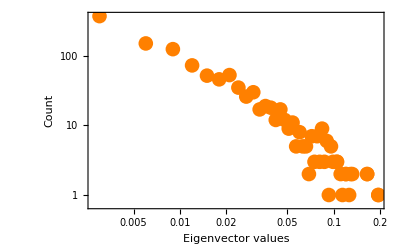

```mathematica
ListLogLogPlot[eigPairs, PlotMarkers->{●,15},PlotStyle->Orange, RotateLabel->True, Frame->True,FrameLabel->{Style["Eigenvector values",16],Style["Count",16]}]
```

```mathematica
dataDDIpag=First[Transpose[Import["C:\Hyperion\4.1\ddi-pagerank41.csv"]]]
```

{0.000217812,0.00759348,0.00269328,0.000260795,0.00732009,0.00231653,0.000260795,0.000407294,0.00046594,0.000235164,0.000658375,0.000430803,0.00296842,0.00142822,0.00287923,0.00020176,0.00270332,0.000252349,0.0020312,0.000667025,0.000259302,0.000377292,0.00127546,0.000747457,0.000383107,0.000211862,0.000369852,0.00387168,0.00056511,0.00358793,0.000532191,0.00208514,0.000423594,0.000259302,0.000192763,0.00054217,0.000736934,0.000921849,0.000889331,0.000453983,0.000193226,0.000532907,0.000416539,0.000259302,0.000187009,0.00158129,0.000187009,0.000176811,0.00119099,0.000450052,0.000292552,0.000292552,0.000686809,0.000766225,0.000580243,0.000637095,0.00144545,0.00186926,0.00155356,0.00318961,0.000668284,0.00157327,0.00211224,0.000552562,0.00164133,0.000714107,0.00042757,0.000634631,0.000628788,0.00173175,0.00139185,0.000848208,0.000727364,0.00129765,0.00108416,0.00180646,0.00217218,0.00169147,0.000981958,0.00214012,0.00163769,0.0015632,0.00144905,0.00074551,0.000806503,0.00102044,0.00132068,0.000339283,0.000401773,0.000221426,0.000268558,0.000394477,0.000236316,0.00180537,0.000329472,0.000798717,0.00133524,0.000777992,0.00118331,0.00240736,0.000529097,0.00018108,0.000221728,0.000427422,0.000427422,0.000427422,0.000536262,0.000362699,0.000379415,0.00123853,0.000250193,0.00752364,0.000629422,0.00116032,0.000540205,0.000339507,0.00123841,0.000206112,0.000206112,0.000206112,0.000192763,0.00029847,0.000329579,0.00019607,0.00111226,0.00069324,0.000339283,0.0002958,0.000192763,0.000242911,0.000192763,0.00617571,0.000290889,0.00176722,0.000260795,0.000407723,0.000543151,0.000192763,0.00057789,0.000407723,0.000357069,0.00126003,0.000429598,0.000608536,0.00114163,0.000326688,0.000276114,0.000192763,0.00145994,0.00100547,0.000225005,0.000192763,0.000465205,0.000987966,0.000231241,0.000695782,0.000592423,0.00124914,0.00070941,0.000344464,0.00369553,0.00134022,0.00179297,0.00146814,0.000407723,0.00146814,0.000625523,0.000192763,0.00163556,0.00181136,0.000520199,0.000349511,0.000236384,0.000242911,0.00192306,0.0054137,0.000816823,0.000192763,0.000192763,0.000671072,0.000775658,0.000192763,0.000233109,0.00110851,0.000428846,0.000276633,0.000376847,0.000290881,0.00162937,0.000987839,0.000227768,0.000357412,0.000648963,0.000681879,0.000192763,0.000383851,0.000283593,0.000192763,0.000259957,0.000884582,0.00188612,0.00074061,0.00110528,0.000192763,0.00039565,0.000532787,0.000549586,0.000705997,0.00173605,0.00055618,0.00124565,0.00360748,0.00301378,0.000540799,0.00141605,0.000536199,0.00102973,0.00200429,0.00021434,0.000504014,0.000187009,0.000172236,0.00113165,0.000167781,0.000439806,0.00424974,0.0027003,0.000268788,0.00362962,0.000545074,0.00269744,0.00303463,0.00156684,0.00165917,0.00166444,0.0054796,0.0010388,0.00138459,0.00179079,0.0015628,0.00016354,0.00163873,0.000513752,0.00365225,0.00136102,0.00120444,0.000374017,0.000428422,0.000659433,0.000779709,0.000701866,0.000594867,0.00116863,0.00383945,0.000226025,0.000586295,0.00228451,0.00152991,0.00154045,0.000951739,0.00375632,0.000740721,0.00875077,0.00100718,0.00126212,0.00115537,0.000701053,0.000851227,0.0023522,0.00126004,0.000337586,0.00119631,0.00136476,0.00371208,0.00025014,0.000305091,0.00333876,0.00224494,0.00279459,0.00100013,0.000454482,0.000703091,0.00232375,0.000564406,0.00016354,0.000785515,0.000924502,0.00213313,0.000441571,0.000559751,0.00109444,0.00205078,0.000231411,0.00105295,0.00341002,0.000605505,0.000239967,0.00695255,0.00323784,0.000701866,0.000407815,0.00590445,0.0057598,0.00174659,0.00136837,0.0033977,0.00150426,0.000590533,0.000678628,0.000337358,0.00126009,0.00130884,0.00239258,0.000232447,0.0023858,0.000538081,0.00443262,0.00280072,0.00144266,0.000817752,0.00375423,0.00223841,0.000419763,0.00147608,0.00205383,0.00461235,0.00129487,0.00206248,0.00160239,0.00194562,0.00123724,0.0010388,0.0010388,0.0010388,0.0010388,0.00188274,0.000737527,0.00241217,0.000681938,0.000742511,0.000387287,0.000273402,0.000243833,0.000552284,0.000261657,0.000261657,0.000453513,0.00107202,0.000943528,0.0011966,0.000458616,0.00016354,0.000275055,0.00120435,0.000275055,0.000167012,0.00305851,0.0024399,0.00561002,0.00315331,0.0033396,0.00241083,0.00360613,0.00273199,0.000259302,0.000357767,0.000188796,0.000954807,0.000370062,0.000418739,0.000315068,0.000309819,0.000162072,0.000482942,0.0030577,0.0020363,0.00394798,0.00223325,0.000419567,0.00030709,0.00029499,0.000853415,0.00268858,0.000248618,0.00281052,0.000235387,0.000728315,0.000355751,0.000853737,0.000541169,0.000497976,0.000213653,0.000972933,0.00101815,0.000235387,0.00130423,0.000312962,0.00045595,0.000365441,0.00121887,0.000779668,0.00296148,0.000682577,0.001057,0.000970849,0.00459407,0.000376652,0.000157788,0.0020865,0.00241287,0.00186197,0.000469605,0.00226918,0.00156067,0.0025408,0.00082365,0.000741018,0.00587933,0.000495158,0.0015246,0.00913515,0.00244216,0.000840287,0.00043012,0.0022823,0.00204426,0.00107254,0.000951539,0.00129429,0.00111701,0.000711662,0.00294959,0.00213231,0.00196043,0.00107762,0.00280288,0.000863332,0.000912688,0.00238723,0.000951539,0.000821425,0.000698221,0.000549055,0.000733781,0.000864305,0.00445938,0.00229014,0.00238915,0.000639537,0.00204083,0.00107254,0.00224198,0.00360464,0.0023663,0.0050459,0.000759511,0.000788566,0.000759511,0.0012672,0.00264869,0.00082125,0.00139014,0.00140132,0.000516321,0.00143587,0.00115503,0.00131107,0.000534048,0.000188138,0.000167781,0.00104477,0.00168039,0.00100825,0.00214854,0.00108839,0.00111196,0.00129038,0.00189584,0.00155032,0.000691541,0.000200109,0.00258456,0.000290348,0.00092734,0.000635113,0.000674818,0.00137036,0.000975558,0.000814599,0.000919422,0.00102942,0.00129524,0.00129524,0.000647963,0.000711853,0.000875351,0.000956374,0.00080239,0.00129524,0.000656887,0.000905679,0.000845818,0.00062656,0.000276001,0.00026059,0.000509039,0.000501475,0.000579837,0.000579837,0.000509039,0.000491232,0.000599905,0.000686458,0.00027561,0.00163024,0.00080583,0.00159686,0.000354367,0.000608253,0.000822497,0.000434603,0.000854041,0.00113045,0.00066574,0.00352781,0.00257828,0.00082508,0.00039838,0.00162901,0.00219149,0.00253216,0.000564705,0.00377767,0.00110677,0.000511972,0.000986465,0.00144865,0.000474991,0.000416863,0.000563499,0.00144452,0.001045,0.00135257,0.000559213,0.00122569,0.000848102,0.000263942,0.000668256,0.00111005,0.0011914,0.000544432,0.00229513,0.000163972,0.00109582,0.000898413,0.00129635,0.000728794,0.000781437,0.000736695,0.000227504,0.0028238,0.000786313,0.00265327,0.0013901,0.000786313,0.000923435,0.000379551,0.000496262,0.000866027,0.00104487,0.00120925,0.000677586,0.00163919,0.000576282,0.00124304,0.000448378,0.000511529,0.000288045,0.000704649,0.000889432,0.000221928,0.000680742,0.00136719,0.000803239,0.00110674,0.00122339,0.00167344,0.00070119,0.00136835,0.00117451,0.00165841,0.000447327,0.000900856,0.00111876,0.000973454,0.000763415,0.00108853,0.000515607,0.000909384,0.000326838,0.000610043,0.000366203,0.000299598,0.000768259,0.000820481,0.000966021,0.00200772,0.00192993,0.00182165,0.000182027,0.000614499,0.000614499,0.000431127,0.000539944,0.000460762,0.000457951,0.000782831,0.000483555,0.000909018,0.000712237,0.000575983,0.00063332,0.000626677,0.000901243,0.000721596,0.000614843,0.000746767,0.000605059,0.00172435,0.000434584,0.000539146,0.000167781,0.000670946,0.00189327,0.000520565,0.000244658,0.000420208,0.000382408,0.000278691,0.000394559,0.000387289,0.000349489,0.000747455,0.000420208,0.000441355,0.000929698,0.000306469,0.000435294,0.000200663,0.000239909,0.000498545,0.000473094,0.00410602,0.000316491,0.000883999,0.000382408,0.000473094,0.000553866,0.000446342,0.000387289,0.000420208,0.000420208,0.000382408,0.00404633,0.000701696,0.000278691,0.000316491,0.00030693,0.00024277,0.000521589,0.00024277,0.000382408,0.000420208,0.00235976,0.000412545,0.000564676,0.000382408,0.000462199,0.000382408,0.000278691,0.00055378,0.000378804,0.000349489,0.000316491,0.00117022,0.000389396,0.000568275,0.000749414,0.000500542,0.000665012,0.000930975,0.000751161,0.000482004,0.000445663,0.00148192,0.000598288,0.00132122,0.00154006,0.00104572,0.00158874,0.000652559,0.00138722,0.000871973,0.000950305,0.000941972,0.000809902,0.000305687,0.000388095,0.000480408,0.000743999,0.000705739,0.000673007,0.000179229,0.000775773,0.00058468,0.0005599,0.000449363,0.000529177,0.000792842,0.000242962,0.000263579,0.000536644,0.000207428,0.000538542,0.000167781,0.000345386,0.000291305,0.000519968,0.00290772,0.000873856,0.000873856,0.000702096,0.000977657,0.0007971,0.0010133,0.000873856,0.000844276,0.000591345,0.000609114,0.000920281,0.00103152,0.000548805,0.000246017,0.000252493,0.0011198,0.000440219,0.000287207,0.000588702,0.000811358,0.000384659,0.000418508,0.000482527,0.000388735,0.000422833,0.00134871,0.000482646,0.000358979,0.000780364,0.000736001,0.000542836,0.000428015,0.000755308,0.000260469,0.000215273,0.000496007,0.000385678,0.000642055,0.000424116,0.000355067,0.000271669,0.000251199,0.000375698,0.00103777,0.000864295,0.000764878,0.000841428,0.000516013,0.000290446,0.000238201,0.000317368,0.000475695,0.000740624,0.000740624,0.000740624,0.000800838,0.000864295,0.00137927,0.00042177,0.000191375,0.000385678,0.000385678,0.000346118,0.00028323,0.000358336,0.000339502,0.000459188,0.00049898,0.000290162,0.00137186,0.00051467,0.000312896,0.000544676,0.000519045,0.000646725,0.000481897,0.000312896,0.000312896,0.00051467,0.000449228,0.000354824,0.000312896,0.000538517,0.00051467,0.000312896,0.00051467,0.000916564,0.000472115,0.000354824,0.000235188,0.00051467,0.000407301,0.000312896,0.000740581,0.000604937,0.000389635,0.000375561,0.000672884,0.00213545,0.00090485,0.000984408,0.000488035,0.000615755,0.000303782,0.000332035,0.000286203,0.00225728,0.000488035,0.000311591,0.000482848,0.000866304,0.00070568,0.000329729,0.000285852,0.000217812,0.000231111,0.000409714,0.000422198,0.00108352,0.000300936,0.000300936,0.000339086,0.000722047,0.000303381,0.000359912,0.000693397,0.00026059,0.000854641,0.000649422,0.00026059,0.000484478,0.000694122,0.000694122,0.000403553,0.00036292,0.000574998,0.000562058,0.000307033,0.000206001,0.00335731,0.000300763,0.0003391,0.00030492,0.000387651,0.000259302,0.000257759,0.000217812,0.000186701,0.000573841,0.00116659,0.000166672,0.000282521,0.000201559,0.00034774,0.000347623,0.000161326,0.000158599,0.000368072,0.000320527,0.000325627,0.000654175,0.00138298,0.00101873,0.000938093,0.000823617,0.00038537,0.000236457,0.00034774,0.00034774,0.000243046,0.000478722,0.000626374,0.000404529,0.000172337,0.000319664,0.000157863,0.000422603,0.000372152,0.000521048,0.000457591,0.000443335,0.00017373,0.000180908,0.000264061,0.000878066,0.0009151,0.00023121,0.000359565,0.000187279,0.000468888,0.000504975,0.000205415,0.00017373,0.000287207,0.000205415,0.000246545,0.000165758,0.000165758,0.000165758,0.00120301,0.000475257,0.000600882,0.000600882,0.000265415,0.000244744,0.000231067,0.00050196,0.000265415,0.000551911,0.000550267,0.00017373,0.000291305,0.000600882,0.000512208,0.000245394,0.000465411,0.000691746,0.000265415,0.000203674,0.000473162,0.000201124,0.000548019,0.000328684,0.000231155,0.000353629,0.000711564,0.00017373,0.00017373,0.000214378,0.000291305,0.000462822,0.000823157,0.00017373,0.00017373,0.000207385,0.00017373,0.00017373,0.000251183,0.000167317,0.000167317,0.000203589,0.000167317,0.000389778,0.000167317,0.000167317,0.000293144,0.000389778,0.000500935,0.000167317,0.000166334,0.000297188,0.000446981,0.000297188,0.00033346,0.000297188,0.000331087,0.000331087,0.000423422,0.000207249,0.000207249,0.000209493,0.000236752,0.000207249,0.000339582,0.000306121,0.000167012,0.000227384,0.000167781,0.000227384,0.000259535,0.000225206,0.000413222,0.000167781,0.000346994,0.000257447,0.000264061,0.000167781,0.000626682,0.000197725,0.000619354,0.000264061,0.000260459,0.000257447,0.000197918,0.000225206,0.000167781,0.000327237,0.000167781,0.000510971,0.000427433,0.000484601,0.000530003,0.0006569,0.000625603,0.000432194,0.000541173,0.000745924,0.000769094,0.000631218,0.00070798,0.000206001,0.00034404,0.000179104,0.000544421,0.000305707,0.000341172,0.000162088,0.000562067,0.000323294,0.000971174,0.00040076,0.000323294,0.00040076,0.00040076,0.00040076,0.000323294,0.00040076,0.00040076,0.000179229,0.00019607,0.000341903,0.000396436,0.000294309,0.000231758,0.000278399,0.000218201,0.000166334,0.000166334,0.000237132,0.00046692,0.000282878,0.000188338,0.000458834,0.000258556,0.000167395,0.000167395,0.000160577,0.000390478,0.00026808,0.000208828,0.000208828,0.000208828,0.000208828,0.000248171,0.000170462,0.000170462,0.000191992,0.000206001,0.000250509,0.000332829,0.000188138,0.000220929,0.000250092,0.00016167,0.000156773,0.000305746,0.00031918,0.000163889,0.00031255,0.000856898,0.000856898,0.000206001,0.000232251,0.000199332,0.000256757,0.000199332,0.000260512,0.000199332,0.000199332,0.000199332,0.000232251,0.000185753,0.000185154,0.000163889,0.000163889,0.000224631,0.000163889,0.000365883,0.000350191,0.000387835,0.000206001,0.000454263,0.000434157,0.000226652,0.000243614,0.000172155,0.00018729,0.000158479,0.000187009,0.000184942,0.000168915,0.000206001,0.000540454,0.000282176,0.000313145,0.000159832,0.000208243,0.000226652,0.000243011,0.00044816,0.000217277,0.000280544,0.000324925,0.000680274,0.00121015,0.000680274,0.000169391,0.000260105,0.00016739,0.000590833,0.000190898,0.000190898,0.000159709,0.000206001,0.000206001,0.000206001,0.000206001,0.000159723,0.000181934,0.000161238,0.000157993,0.000189276,0.000247439,0.000173605,0.000201494,0.000159288,0.000246405,0.00016557,0.000164519,0.000185959,0.000185959,0.000185959,0.000196566,0.000328712,0.000189276,0.000159644,0.000159644,0.000221249}

```mathematica
histPag =HistogramList[dataDDIpag,{0.0001}]
```

{{0.0001,0.0002,0.0003,0.0004,0.0005,0.0006,0.0007,0.0008,0.0009,0.001,0.0011,0.0012,0.0013,0.0014,0.0015,0.0016,0.0017,0.0018,0.0019,0.002,0.0021,0.0022,0.0023,0.0024,0.0025,0.0026,0.0027,0.0028,0.0029,0.003,0.0031,0.0032,0.0033,0.0034,0.0035,0.0036,0.0037,0.0038,0.0039,0.004,0.0041,0.0042,0.0043,0.0044,0.0045,0.0046,0.0047,0.0048,0.0049,0.005,0.0051,0.0052,0.0053,0.0054,0.0055,0.0056,0.0057,0.0058,0.0059,0.006,0.0061,0.0062,0.0063,0.0064,0.0065,0.0066,0.0067,0.0068,0.0069,0.007,0.0071,0.0072,0.0073,0.0074,0.0075,0.0076,0.0077,0.0078,0.0079,0.008,0.0081,0.0082,0.0083,0.0084,0.0085,0.0086,0.0087,0.0088,0.0089,0.009,0.0091,0.0092},{128,186,137,113,94,68,67,48,38,33,25,28,23,14,15,15,7,10,4,11,8,10,9,6,4,5,4,5,4,4,2,1,4,1,2,6,4,2,1,1,1,1,0,2,1,1,0,0,0,1,0,0,0,2,0,1,1,1,1,0,1,0,0,0,0,0,0,0,1,0,0,0,1,0,2,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1}}

```mathematica
valuesPag = Part[histPag,1]
```

{0.0001,0.0002,0.0003,0.0004,0.0005,0.0006,0.0007,0.0008,0.0009,0.001,0.0011,0.0012,0.0013,0.0014,0.0015,0.0016,0.0017,0.0018,0.0019,0.002,0.0021,0.0022,0.0023,0.0024,0.0025,0.0026,0.0027,0.0028,0.0029,0.003,0.0031,0.0032,0.0033,0.0034,0.0035,0.0036,0.0037,0.0038,0.0039,0.004,0.0041,0.0042,0.0043,0.0044,0.0045,0.0046,0.0047,0.0048,0.0049,0.005,0.0051,0.0052,0.0053,0.0054,0.0055,0.0056,0.0057,0.0058,0.0059,0.006,0.0061,0.0062,0.0063,0.0064,0.0065,0.0066,0.0067,0.0068,0.0069,0.007,0.0071,0.0072,0.0073,0.0074,0.0075,0.0076,0.0077,0.0078,0.0079,0.008,0.0081,0.0082,0.0083,0.0084,0.0085,0.0086,0.0087,0.0088,0.0089,0.009,0.0091,0.0092}

```mathematica
frecPag=Part[histPag, 2]
```

{128,186,137,113,94,68,67,48,38,33,25,28,23,14,15,15,7,10,4,11,8,10,9,6,4,5,4,5,4,4,2,1,4,1,2,6,4,2,1,1,1,1,0,2,1,1,0,0,0,1,0,0,0,2,0,1,1,1,1,0,1,0,0,0,0,0,0,0,1,0,0,0,1,0,2,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1}

```mathematica
valuesclearPag=  Delete[valuesPag, 1]
```

{0.0002,0.0003,0.0004,0.0005,0.0006,0.0007,0.0008,0.0009,0.001,0.0011,0.0012,0.0013,0.0014,0.0015,0.0016,0.0017,0.0018,0.0019,0.002,0.0021,0.0022,0.0023,0.0024,0.0025,0.0026,0.0027,0.0028,0.0029,0.003,0.0031,0.0032,0.0033,0.0034,0.0035,0.0036,0.0037,0.0038,0.0039,0.004,0.0041,0.0042,0.0043,0.0044,0.0045,0.0046,0.0047,0.0048,0.0049,0.005,0.0051,0.0052,0.0053,0.0054,0.0055,0.0056,0.0057,0.0058,0.0059,0.006,0.0061,0.0062,0.0063,0.0064,0.0065,0.0066,0.0067,0.0068,0.0069,0.007,0.0071,0.0072,0.0073,0.0074,0.0075,0.0076,0.0077,0.0078,0.0079,0.008,0.0081,0.0082,0.0083,0.0084,0.0085,0.0086,0.0087,0.0088,0.0089,0.009,0.0091,0.0092}

```mathematica
pagPairs = Transpose[{valuesclearPag,frecPag}]
```

{{0.0002,128},{0.0003,186},{0.0004,137},{0.0005,113},{0.0006,94},{0.0007,68},{0.0008,67},{0.0009,48},{0.001,38},{0.0011,33},{0.0012,25},{0.0013,28},{0.0014,23},{0.0015,14},{0.0016,15},{0.0017,15},{0.0018,7},{0.0019,10},{0.002,4},{0.0021,11},{0.0022,8},{0.0023,10},{0.0024,9},{0.0025,6},{0.0026,4},{0.0027,5},{0.0028,4},{0.0029,5},{0.003,4},{0.0031,4},{0.0032,2},{0.0033,1},{0.0034,4},{0.0035,1},{0.0036,2},{0.0037,6},{0.0038,4},{0.0039,2},{0.004,1},{0.0041,1},{0.0042,1},{0.0043,1},{0.0044,0},{0.0045,2},{0.0046,1},{0.0047,1},{0.0048,0},{0.0049,0},{0.005,0},{0.0051,1},{0.0052,0},{0.0053,0},{0.0054,0},{0.0055,2},{0.0056,0},{0.0057,1},{0.0058,1},{0.0059,1},{0.006,1},{0.0061,0},{0.0062,1},{0.0063,0},{0.0064,0},{0.0065,0},{0.0066,0},{0.0067,0},{0.0068,0},{0.0069,0},{0.007,1},{0.0071,0},{0.0072,0},{0.0073,0},{0.0074,1},{0.0075,0},{0.0076,2},{0.0077,0},{0.0078,0},{0.0079,0},{0.008,0},{0.0081,0},{0.0082,0},{0.0083,0},{0.0084,0},{0.0085,0},{0.0086,0},{0.0087,0},{0.0088,1},{0.0089,0},{0.009,0},{0.0091,0},{0.0092,1}}

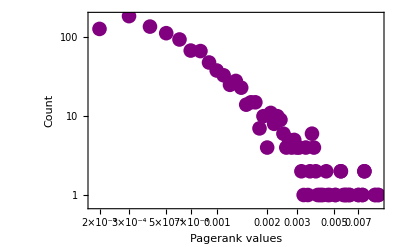

```mathematica
ListLogLogPlot[pagPairs, PlotMarkers->{●,15},PlotStyle->Purple, RotateLabel->True, Frame->True,FrameLabel->{Style["Pagerank values",16],Style["Count",16]}]
```

```mathematica
FindFit[cloPairs,a PDF[NormalDistribution[μ,σ],x],{a,μ,σ},x]
```

{a→23.4371,μ→0.348436,σ→0.0481659}

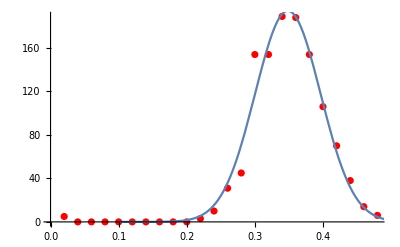

```mathematica
Show[ListPlot[cloPairs,PlotStyle->Red],Plot[23.43713160100763 PDF[NormalDistribution[0.3484360716312709,0.048165888725609805],x],{x,0.1,0.8}]]
```